# The superfluid boson singlet state of the gauge-covariant spinor field on the 3+1 manifold of the Lorentz super-loop

## PROJECT spacetimes, folder Revision_HS_CJT_and_Kohn-Sham. The notebook superfluid.nb, prepared for Patrick Lee Nash, Ph.D.

This notebook is the Wolfram Language companion of the manuscript of the solution in the same folder, written so that a first-year graduate student in physics can follow every step. It states the problem and the conventions, defines every object that a computation needs, writes out the equations that can be executed, and executes them: the algebra of the manifold M31 and of the Lorentz super-loop, the spinor field and the gauge group GEE with its covariant derivatives, the field equations and their analytic solutions, the condensation of the spinor field into the superfluid boson singlet state by the methods of Hubbard and Stratonovich (HS), of Kohn and Sham (KS) and of Cornwall, Jackiw and Tomboulis (CJT), the effective Lagrangians and the Mexican hat, the breaking of the symmetry and the masses of the gauge bosons, the surviving symmetry with its massless photon, and the dynamics. Every time integration in this notebook is done by the method IDA of the function NDSolve; no fixed-step integrator (such as the fourth-order Runge-Kutta method) is used anywhere.

How to use it. Open the notebook in Wolfram (version 15 or later; it was evaluated with Wolfram 15.0.1) and choose Evaluation > Evaluate Notebook. The cells are evaluated in order. Nothing outside this notebook is read: every definition and every program is inside it. Every check prints one line that begins with PASS or FAIL, and the last chapter lists all checks.

How to read it. A text cell explains, in words and formulas, what the next input cell does and why. Inside the code, comments (* like this *) explain each step, and every symbol of the code that stands for an object of the physics has a comment with its printed name and its meaning the first time it is defined. A symbol of the printed text with the suffix LL is taken unchanged from the earlier work of the project on the super-loop; a symbol with the suffix SF is introduced by this solution.

The checks and their counterparts. Every computation of this notebook is also done by a program in Rust and by a program in Python, in the folders rust/ and python/ of the folder of the solution; users without a Wolfram license can follow the solution with those programs. Every check of this notebook carries the identifier of the same check in the Rust program with the prefix W (for example WA-3 is the check A-3 of the Rust program sf_part1 and of the Python program sf_part1.py), and the line that it prints names both counterparts. The notebook computes its values itself, by methods of the Wolfram Language (exact arithmetic where the Rust program computes in floating point, symbolic derivatives where it differentiates automatically, the solvers of the Wolfram Language where it uses its own); the numbers agree with those of the two programs within the tolerances stated in each check.

## 0. The register of the checks

The next cell defines the functions that record and print a check. check[id, text, dev, tol, rust, python] records a numerical check: it passes when the measured deviation dev is at most the tolerance tol; rust and python are the identifiers of the same check in the Rust and in the Python program. checkTrue[id, text, ok, detail, rust, python] records a check that is decided by facts (a count, an exact identity), with a short detail. Both append an association to the list SFNB`Test`$Results, the register of all checks of this notebook, and print one line. The function sci writes a number with four significant digits in the form 2.857e-8, as the reports of the Rust and the Python programs do.

```mathematica
(* the register of the checks of this notebook: one association per check, in the order of evaluation *)
SFNB`Test`$Results = {};
(* sci[x]: the number x with four significant digits, written as mantissa e exponent (for example 2.857e-8) *)
sci[x_?NumericQ] := Module[{y = N[x], e, m},
   If[y == 0, Return["0", Module]];
   e = Floor[Log10[Abs[y]]]; m = Round[y/10.^e, 0.001];
   If[Abs[m] >= 10, m = m/10; e = e + 1];
   ToString[NumberForm[m, {4, 3}]] <> "e" <> ToString[e]];
(* checkHook[]: called after every check; it does nothing here (a dry run of the code without the front end
   uses it to print the computing time of each check) *)
checkHook[] := Null;
(* check[id, text, dev, tol, rust, python]: a numerical check, passed when dev <= tol *)
check[id_String, text_String, dev_?NumericQ, tol_?NumericQ, rust_String, python_String] := Module[{ok = TrueQ[N[dev] <= tol]},
   AppendTo[SFNB`Test`$Results, <|"id" -> id, "pass" -> ok, "deviation" -> N[dev], "tolerance" -> N[tol],
      "text" -> text, "rust" -> rust, "python" -> python|>];
   Print[If[ok, "PASS ", "FAIL "], id, "  deviation ", sci[dev], " (tolerance ", sci[tol], "): ", text,
     "   [the same check: Rust ", rust, ", Python ", python, "]"];
   checkHook[]; ok];
(* checkTrue[id, text, ok, detail, rust, python]: a check decided by facts; detail states them *)
checkTrue[id_String, text_String, ok_, detail_String, rust_String, python_String] := Module[{pass = TrueQ[ok]},
   AppendTo[SFNB`Test`$Results, <|"id" -> id, "pass" -> pass, "deviation" -> Missing["NotNumerical"], "tolerance" -> Missing["NotNumerical"],
      "text" -> text <> " [" <> detail <> "]", "rust" -> rust, "python" -> python|>];
   Print[If[pass, "PASS ", "FAIL "], id, "  ", text, " [", detail, "]   [the same check: Rust ", rust, ", Python ", python, "]"];
   checkHook[]; pass];
```

## Part I. The manifold M31, the spinor field, GEE, the field equations and four analytic solutions

Part I treats items 1 to 5 of the problem (Sections 1 to 7 of the manuscript): the manifold M31 of the Lorentz super-loop, the spinor fields on it and the Dirac field, the gauge group GEE and its covariant derivatives, the Lagrangian with its field equations, and analytic solutions of four simple cases. Its checks are those of the Python program sf_part1.py, which repeats a part of the checks of the Rust program sf_part1; the random test values of this notebook come from the generator of the Wolfram Language with the seed 20261121, so they differ from those of the two programs, as theirs differ from each other.

## I.1 Conventions, units and the common objects

Units. Planck's constant and the speed of light are 1; energies, masses and momenta are measured in units of the momentum cutoff Λ_LL==1, lengths and times in units of 1/Λ_LL. The mass of the spinor field is m_LL==0.2.

Indices. p,p' run over the four coordinates of M31 (0 is the time), j,j',j'' over the three space coordinates, ι,ι',ι'' over the three directions of isospin (an internal direction, not a direction in space), and c,c' over the eight components of the spinor field. The letter i is always the imaginary unit. The Minkowski metric is η_(p p')^LL==diag(1,-1,-1,-1).

Matrices. σ_0^LL is the 2×2 unit matrix and σ_1^LL,σ_2^LL,σ_3^LL are the Pauli matrices; acting on isospin they are written τ_ι^LL. E_LL==i σ_2^LL. The Dirac matrices are those of the chiral basis, γ_LL^0 with the blocks σ_0^LL off the diagonal and γ_LL^j with the blocks σ_j^LL and -σ_j^LL; γ_LL^ch==i γ_LL^0 γ_LL^1 γ_LL^2 γ_LL^3==diag(-1,-1,1,1), C_LL==i γ_LL^2 γ_LL^0, α_LL^j==γ_LL^0 γ_LL^j and β_LL==γ_LL^0. The spinor field Ψ_LL has eight components: the Dirac index d (four values) and the isospin index s (up, down); a 4×4 Dirac matrix A acts on it as A⊗1_2 and an isospin matrix t as 1_4⊗t. The isospin generators are T_LL^ι==1_4⊗τ_ι^LL/2, the matrices of the three spin-zero pair fields are K_LL^ι==C_LL γ_LL^ch⊗E_LL τ_ι^LL, and the free Dirac Hamiltonian at the momentum (q⃗)_LL is h_LL((q⃗)_LL)==∑_j α_LL^j q_LL^j+β_LL m_LL.

The author's conventions (the Standard Model). The covariant derivative of the Higgs doublet is D_μ^SM Φ^SM==(∂_μ +ig ∑_(a==1)^3 τ^a/2 W_μ^a+i g' Y^SM B_μ)Φ^SM with Y^SM==1/2 and Q^SM==T^(3,SM)+Y^SM; the fields of definite mass are W_μ^±==(W_μ^1∓i W_μ^2)/√2, Z_μ==cos θ_W W_μ^3-sin θ_W B_μ and the photon A_μ==sin θ_W W_μ^3+cos θ_W B_μ, with e==g sin θ_W; with ⟨Φ^SM⟩==(0,v)/√2 the masses are M_W==gv/2 and M_Z==√(g^2+g^(′2)) v/2, and the photon is massless. All GEE covariant derivatives of the solution use the same sign, +i in front of every coupling.

The next cell defines these matrices, the bi-quaternions and bi-octonions of Section I.2, the Lorentz matrices, the spinor matrices and the operators of the Fock space of one point. They are the same objects as those of the Rust library sfcore and of the Python module sfcommon.py, written here with the functions of the Wolfram Language.

```mathematica
(* the mass of the spinor field, m_LL, in units of the cutoff Lambda_LL = 1 *)
mLL = 1/5;
(* sig[[p + 1]] is sigma^LL_p (p = 0, 1, 2, 3): sigma_0 is the 2 x 2 unit matrix, sigma_1, sigma_2, sigma_3 the Pauli matrices *)
sig = {IdentityMatrix[2], PauliMatrix[1], PauliMatrix[2], PauliMatrix[3]};
(* sigbar[[p + 1]] is sigma-bar_p: sigma_0 and -sigma_j, the blocks of the Dirac matrices below the diagonal *)
sigbar = {sig[[1]], -sig[[2]], -sig[[3]], -sig[[4]]};
(* eLL is E_LL = i sigma_2 = {{0, 1}, {-1, 0}} *)
eLL = {{0, 1}, {-1, 0}};
(* etaLL is the Minkowski metric eta^LL = diag(1, -1, -1, -1) *)
etaLL = DiagonalMatrix[{1, -1, -1, -1}];
(* levi[a, b, c] is the Levi-Civita symbol epsilon^LL of the indices 1, 2, 3 *)
levi[a_, b_, c_] := Signature[{a, b, c}];
(* gam[p] is the Dirac matrix gamma^p_LL of the chiral basis: {{0, sigma_p}, {sigmabar_p, 0}} *)
gam[p_Integer] := ArrayFlatten[{{0, sig[[p + 1]]}, {sigbar[[p + 1]], 0}}];
(* gch is the chirality matrix gamma^ch_LL = i gamma^0 gamma^1 gamma^2 gamma^3 *)
gch = I gam[0] . gam[1] . gam[2] . gam[3];
(* cLL is the charge-conjugation matrix C_LL = i gamma^2 gamma^0 *)
cLL = I gam[2] . gam[0];
(* betaLL = gamma^0_LL and alphaLL[j] = gamma^0 gamma^j, the matrices of the Dirac Hamiltonian *)
betaLL = gam[0];
alphaLL[j_Integer] := gam[0] . gam[j];
(* d8[a] = a (x) 1_2 acts on the Dirac index of the eight components (component 2 d + s, d = 0..3, s = 0 up, 1 down) *)
d8[a_] := KroneckerProduct[a, IdentityMatrix[2]];
(* i8[t] = 1_4 (x) t acts on the isospin index *)
i8[t_] := KroneckerProduct[IdentityMatrix[4], t];
(* tLL[iota] is the isospin generator T^iota_LL = 1_4 (x) tau_iota/2 *)
tLL[iota_Integer] := i8[sig[[iota + 1]]/2];
(* kLL[iota] is the pair matrix K^iota_LL = C_LL gamma^ch_LL (x) E_LL tau_iota of the scalar spin-zero pairs *)
kLL[iota_Integer] := KroneckerProduct[cLL . gch, eLL . sig[[iota + 1]]];
(* hLL[q, m] is the free Dirac Hamiltonian h_LL(q) = sum_j alpha^j q_j + beta m on the eight components *)
hLL[q_List, m_] := d8[betaLL m + Sum[alphaLL[j] q[[j]], {j, 3}]];

(* ---- bi-quaternions: a bi-quaternion b = xi_0 e_0 + xi_1 e_1 + xi_2 e_2 + xi_3 e_3 is the list {xi_0, xi_1, xi_2, xi_3} ---- *)
(* qMul is the product of bi-quaternions by the rules (2.1) of the quaternion units *)
qMul[{a0_, a1_, a2_, a3_}, {b0_, b1_, b2_, b3_}] := {a0 b0 - a1 b1 - a2 b2 - a3 b3, a0 b1 + a1 b0 + a2 b3 - a3 b2,
   a0 b2 - a1 b3 + a2 b0 + a3 b1, a0 b3 + a1 b2 - a2 b1 + a3 b0};
(* qBar is the conjugation (the signs of xi_1, xi_2, xi_3 change); qDag the Hermitian conjugation *)
qBar[{a0_, a1_, a2_, a3_}] := {a0, -a1, -a2, -a3};
qDag[x_List] := Conjugate[qBar[x]];
(* qNorm is the complex norm N_LL(b) = sum_p xi_p^2 *)
qNorm[x_List] := Total[x^2];
(* mLLmat[b] is the matrix M_LL(b) = xi_0 sigma_0 - i sum_j xi_j sigma_j of (2.2), and biqOf its inverse map *)
mLLmat[b_List] := b[[1]] sig[[1]] - I (b[[2]] sig[[2]] + b[[3]] sig[[3]] + b[[4]] sig[[4]]);
biqOf[m_] := Join[{Tr[m]/2}, Table[I/2 Tr[sig[[j + 1]] . m], {j, 3}]];

(* ---- bi-octonions: x = a + b e_4 is the pair {a, b} of bi-quaternions ---- *)
(* oMul is the Cayley-Dickson product (2.3): (a + b e4)(c + d e4) = (a c - dbar b) + (d a + b cbar) e4 *)
oMul[{a_, b_}, {c_, d_}] := {qMul[a, c] - qMul[qBar[d], b], qMul[d, a] + qMul[b, qBar[c]]};
(* oUnit[p] is the unit e_p (p = 0..7; e_{4+j} = e_j e_4) *)
oUnit[p_Integer] := If[p < 4, {UnitVector[4, p + 1], {0, 0, 0, 0}}, {{0, 0, 0, 0}, UnitVector[4, p - 3]}];
(* oBar is the conjugation of bi-octonions, oNorm the complex norm N_LL(x) = N_LL(a) + N_LL(b) *)
oBar[{a_, b_}] := {qBar[a], -b};
oNorm[{a_, b_}] := qNorm[a] + qNorm[b];
(* oMax is the largest modulus of the sixteen coefficients: the size of a difference *)
oMax[x_] := Max[Abs[Flatten[x]]];

(* ---- Lorentz transformations and spinor matrices ---- *)
(* expTraceless[x] is exp(X) of a traceless 2 x 2 matrix: cosh(s) 1 + sinh(s)/s X with s^2 = -det X *)
expTraceless[x_] := Module[{s = Sqrt[-Det[x]]}, If[Abs[s] < 10^-8, IdentityMatrix[2] + x + x . x/2,
    Cosh[s] IdentityMatrix[2] + Sinh[s]/s x]];
(* lorentzGenerator[rot, boost] is the matrix M_LL(u) of the Lorentz generator with the rotation parameters rot and the
   rapidities boost: sum_j (boost_j/2 - i rot_j/2) sigma_j *)
lorentzGenerator[rot_List, boost_List] := Sum[(boost[[j]]/2 - I rot[[j]]/2) sig[[j + 1]], {j, 3}];
(* lorentzMatrix[mg] is L_LL(g)_pp' = (1/2) Re tr(sigma_p M sigma_p' M^dag) of (2.10), mg = M_LL(g) *)
lorentzMatrix[mg_] := Table[Re[Tr[sig[[p + 1]] . mg . sig[[q + 1]] . ConjugateTranspose[mg]]]/2, {p, 0, 3}, {q, 0, 3}];
(* sSpin[mg] is the spinor matrix S_LL(g) = diag((M^dag)^-1, M) of (3.7) *)
sSpin[mg_] := ArrayFlatten[{{Inverse[ConjugateTranspose[mg]], 0}, {0, mg}}];
(* sGen[mu] is s_LL(u) = diag(-M(u)^dag, M(u)), the action of a Lorentz generator on the Dirac index *)
sGen[mu_] := ArrayFlatten[{{-ConjugateTranspose[mu], 0}, {0, mu}}];
(* randUnitBiq[] is the matrix of a random unit bi-quaternion: exp of a random Lorentz generator *)
randUnitBiq[amp_ : 1.5] := expTraceless[lorentzGenerator[amp RandomReal[{-1, 1}, 3], amp RandomReal[{-1, 1}, 3]]];

(* ---- the Fock space of one point: 2^n states, the occupation of mode k is the bit k of the state number ---- *)
(* fockOps[n] are the annihilation operators c_0 .. c_(n-1) as sparse matrices, with the sign (-1)^(number of occupied
   modes below k) of the ordering of Jordan and Wigner *)
fockOps[n_Integer] := Table[SparseArray[Flatten[Table[If[BitGet[b, k] == 1,
       {BitXor[b, 2^k] + 1, b + 1} -> (-1)^DigitCount[BitAnd[b, 2^k - 1], 2, 1], Nothing], {b, 0, 2^n - 1}]], {2^n, 2^n}],
   {k, 0, n - 1}];
(* the seed of the random test values of this notebook *)
SeedRandom[20261121];
Print["the common objects are defined; m_LL = ", mLL];
```

the common objects are defined; m_LL = 1/5

The first check of the conventions: the mass matrix of the gauge fields of the Standard Model, computed from the covariant derivative (1.1) with +ig, has the eigenvalues 0 (the photon), M_W^2 (twice) and M_Z^2, with the eigenvectors A_μ and Z_μ of the text. The kinetic term (D_μ⟨Φ^SM⟩)^†D^μ⟨Φ^SM⟩ of the constant vacuum is the quadratic form 1/2 ∑_ab M_ab V_μ^a V^(b,μ) of the four fields (W^1,W^2,W^3,B); the cell computes M exactly, with symbolic couplings, and diagonalizes it. The Rust program sf_part1 checks the same statement with numbers through the four eigenvectors, and the Python program sf_part1.py through the eigenvalues computed by LAPACK (check SM-1 of both); the same computation for the superfluid is the mass matrix (14.3) of Part IV.

```mathematica
(* gSM, gpSM: the couplings g and g' of SU(2)_L and U(1)_Y; vSM: the vacuum value v (all positive symbols) *)
Clear[gSM, gpSM, vSM];
(* phiSM: the vacuum <Phi^SM> = (0, v)/sqrt2 of the Higgs doublet *)
phiSM = {0, vSM/Sqrt[2]};
(* xSM[a]: the vector X_a with D_mu <Phi> = sum_a V^a_mu X_a for the fields V = (W^1, W^2, W^3, B):
   i g tau_a/2 <Phi> for a = 1, 2, 3 and i g' Y <Phi> (Y = 1/2) for B *)
xSM = Join[Table[(I gSM/2) sig[[a + 1]] . phiSM, {a, 3}], {(I gpSM/2) phiSM}];
(* the mass matrix M_ab = 2 Re(X_a^dag X_b): (D <Phi>)^dag (D <Phi>) = (1/2) sum_ab M_ab V^a V^b *)
mSM = Table[2 ComplexExpand[Re[Conjugate[xSM[[a]]] . xSM[[b]]]], {a, 4}, {b, 4}];
(* the predicted eigenvalues: 0, M_W^2 = (g v/2)^2 twice, M_Z^2 = (g^2 + g'^2) v^2/4; they are the eigenvalues exactly when
   the characteristic polynomial det(M - lam 1) equals the product of the factors (lam - eigenvalue) *)
evSMpred = {0, (gSM vSM/2)^2, (gSM vSM/2)^2, (gSM^2 + gpSM^2) vSM^2/4};
charSM = Expand[CharacteristicPolynomial[mSM, lam] - Product[lam - ev, {ev, evSMpred}]];
(* the photon A = sin(thetaW) W^3 + cos(thetaW) B with tan(thetaW) = g'/g is the null vector *)
photonSM = {0, 0, gpSM, gSM}/Sqrt[gSM^2 + gpSM^2];
Print["the mass matrix of (W1, W2, W3, B): ", MatrixForm[mSM]];
checkTrue["WSM-1", "Standard Model with +i g: the eigenvalues of the mass matrix are 0, M_W^2 (twice), M_Z^2, and the photon sin(thetaW) W^3 + cos(thetaW) B is massless",
  charSM === 0 && Simplify[mSM . photonSM] === {0, 0, 0, 0}, "exact, with symbolic g, g', v",
  "SM-1", "SM-1"];
```

the mass matrix of (W1, W2, W3, B): ((gSM^2 vSM^2)/4 | 0 | 0 | 0
0 | (gSM^2 vSM^2)/4 | 0 | 0
0 | 0 | (gSM^2 vSM^2)/4 | -1/4 gpSM gSM vSM^2
0 | 0 | -1/4 gpSM gSM vSM^2 | (gpSM^2 vSM^2)/4)

PASS WSM-1  Standard Model with +i g: the eigenvalues of the mass matrix are 0, M_W^2 (twice), M_Z^2, and the photon sin(thetaW) W^3 + cos(thetaW) B is massless [exact, with symbolic g, g', v]   [the same check: Rust SM-1, Python SM-1]

## I.2 The manifold M31 of the Lorentz super-loop (item 1)

Bi-quaternions. A bi-quaternion is b==∑_(p==0)^3 ξ_p^LL(b) e_p with four complex coefficients and the units e_0==1,e_1,e_2,e_3, multiplied by the rules of the quaternions, e_j^2==-1, e_1 e_2==-e_2 e_1==e_3 and cyclically. The conjugation b̄ changes the signs of the coefficients of e_1,e_2,e_3, the complex conjugation b^* conjugates every coefficient, and b^†==(b̄)^*. The complex norm N_LL(b)==∑_p ξ_p^LL(b)^2 satisfies b b̄==N_LL(b) e_0 and N_LL(b b')==N_LL(b)N_LL(b'). The matrix M_LL(b)==ξ_0^LL σ_0^LL-i ∑_j ξ_j^LL σ_j^LL is multiplicative, has the determinant N_LL(b), satisfies M_LL(b^†)==M_LL(b)^†, and every complex 2×2 matrix is the matrix of exactly one bi-quaternion; the unit bi-quaternions (N_LL==1) are therefore the group SL(2,ℂ).

Bi-octonions and the super-loop. A bi-octonion is x==a+b e_4 with two bi-quaternions, multiplied by the rule of Cayley and Dickson

(a+b e_4)(c+d e_4)==(ac-d̄ b)+(da+b c̄) e_4,

with the eight units e_0,…,e_3,e_4 and e_(4+j)==e_j e_4. The norm is multiplicative, N_LL(xy)==N_LL(x)N_LL(y), and x x̄==N_LL(x)e_0. The product is not associative ((e_1 e_2)e_4-e_1(e_2 e_4)==2 e_7), but it is alternative, (xx)y==x(xy), and satisfies the three Moufang identities (zxz)y==z(x(zy)), y(zxz)==((yz)x)z and (zx)(yz)==(z(xy))z. The unit bi-octonions form the Lorentz super-loop 𝕃_LL, a Moufang loop of real dimension 14 that contains SL(2,ℂ).

The next cell checks these rules exactly: bi-octonions with small integer (Gaussian integer) coefficients are multiplied in exact arithmetic, so every identity must hold with the deviation exactly 0. Of the 343 ordered triples of imaginary units, 168 have a nonzero associator: a triple with two equal members has none (alternativity), and of the 210 triples of distinct units a triple has none exactly when its third unit is plus or minus the product of the first two, which leaves 210 - 42 = 168.

```mathematica
(* A-2: the rules of the eight units: e_p^2 = -1, e_p e_q = -e_q e_p (p != q, both >= 1), e_j e_4 = e_(4+j) *)
dA2 = Max[Join[
    Table[oMax[oMul[oUnit[p], oUnit[p]] + oUnit[0]], {p, 1, 7}],
    Flatten[Table[If[p != q, oMax[oMul[oUnit[p], oUnit[q]] + oMul[oUnit[q], oUnit[p]]], 0], {p, 1, 7}, {q, 1, 7}]],
    Table[oMax[oMul[oUnit[j], oUnit[4]] - oUnit[4 + j]], {j, 1, 3}]]];
check["WA-2", "bi-octonion units: e_p^2 = -1, e_p e_q = -e_q e_p, e_j e_4 = e_(4+j) (exact)", dA2, 0, "A-2", "A-2"];
(* rintBio[] is a random bi-octonion with Gaussian-integer coefficients between -3 and 3 *)
rintBio[] := {RandomInteger[{-3, 3}, 4] + I RandomInteger[{-3, 3}, 4], RandomInteger[{-3, 3}, 4] + I RandomInteger[{-3, 3}, 4]};
(* A-3 to A-6 on 200 random triples (x, y, z), in exact arithmetic *)
{dA3, dA4, dA5, dA6} = {0, 0, 0, 0};
Do[Module[{x = rintBio[], y = rintBio[], z = rintBio[], zxz},
   dA3 = Max[dA3, Abs[oNorm[oMul[x, y]] - oNorm[x] oNorm[y]]];
   dA4 = Max[dA4, oMax[oMul[x, oBar[x]] - oNorm[x] oUnit[0]]];
   dA5 = Max[dA5, oMax[oMul[oMul[x, x], y] - oMul[x, oMul[x, y]]], oMax[oMul[oMul[y, x], x] - oMul[y, oMul[x, x]]]];
   zxz = oMul[oMul[z, x], z];
   dA6 = Max[dA6, oMax[oMul[zxz, y] - oMul[z, oMul[x, oMul[z, y]]]], oMax[oMul[y, zxz] - oMul[oMul[oMul[y, z], x], z]],
     oMax[oMul[oMul[z, x], oMul[y, z]] - oMul[oMul[z, oMul[x, y]], z]]]], {200}];
check["WA-3", "N(xy) = N(x) N(y), 200 random Gaussian-integer bi-octonions (exact)", dA3, 0, "A-3", "A-3"];
check["WA-4", "x xbar = N(x) e_0 (exact)", dA4, 0, "A-4", "A-4"];
check["WA-5", "alternativity (xx)y = x(xy), (yx)x = y(xx) (exact)", dA5, 0, "A-5", "A-5"];
check["WA-6", "the three Moufang identities (exact)", dA6, 0, "A-6", "A-6"];
(* A-7: the associators of the 343 ordered triples of imaginary units, and (e1 e2) e4 - e1 (e2 e4) = 2 e7 *)
nonzeroAssociators = Count[Flatten[Table[oMax[oMul[oMul[oUnit[p], oUnit[q]], oUnit[r]] - oMul[oUnit[p], oMul[oUnit[q], oUnit[r]]]],
      {p, 1, 7}, {q, 1, 7}, {r, 1, 7}]], v_ /; v > 0];
a124 = oMul[oMul[oUnit[1], oUnit[2]], oUnit[4]] - oMul[oUnit[1], oMul[oUnit[2], oUnit[4]]];
checkTrue["WA-7", "168 of the 343 triples of imaginary units have a nonzero associator; (e1 e2) e4 - e1 (e2 e4) = 2 e7",
  nonzeroAssociators == 168 && oMax[a124 - 2 oUnit[7]] == 0, ToString[nonzeroAssociators] <> " nonzero", "A-7", "A-7"];
```

PASS WA-2  deviation 0 (tolerance 0): bi-octonion units: e_p^2 = -1, e_p e_q = -e_q e_p, e_j e_4 = e_(4+j) (exact)   [the same check: Rust A-2, Python A-2]

PASS WA-3  deviation 0 (tolerance 0): N(xy) = N(x) N(y), 200 random Gaussian-integer bi-octonions (exact)   [the same check: Rust A-3, Python A-3]

PASS WA-4  deviation 0 (tolerance 0): x xbar = N(x) e_0 (exact)   [the same check: Rust A-4, Python A-4]

PASS WA-5  deviation 0 (tolerance 0): alternativity (xx)y = x(xy), (yx)x = y(xx) (exact)   [the same check: Rust A-5, Python A-5]

PASS WA-6  deviation 0 (tolerance 0): the three Moufang identities (exact)   [the same check: Rust A-6, Python A-6]

PASS WA-7  168 of the 343 triples of imaginary units have a nonzero associator; (e1 e2) e4 - e1 (e2 e4) = 2 e7 [168 nonzero]   [the same check: Rust A-7, Python A-7]

The manifold M31 and its Lorentz group. M31 is the real vector space of the Hermitian bi-quaternions x==x_LL^0 e_0+i ∑_j x_LL^j e_j; their matrices M_LL(x)==∑_p x_LL^p σ_p^LL are the Hermitian 2×2 matrices, and the norm N_LL(x)==(x_LL^0)^2-∑_j (x_LL^j)^2 is the Minkowski interval. A unit bi-quaternion g acts by x↦gx g^†; this keeps M31 and the interval, so it is a Lorentz transformation, with the real matrix

L_LL(g)_(p p')==1/2 Re tr(σ_p^LL M_LL(g) σ_p'^LL M_LL(g)^†),

which is proper and orthochronous (L^T ηL==η, det L==1, L_00≥1) and multiplicative, with L_LL(-g)==L_LL(g): SL(2,ℂ) is the double cover of the proper orthochronous Lorentz group. The next cell checks the properties of M_LL exactly (with Gaussian-integer coefficients) and those of L_LL with 200 random unit bi-quaternions in floating point. A spinor charge of the super-loop is a bi-octonion b e_4; by the product rule the super-loop acts on it as (b e_4)g==(b ḡ)e_4 and g(b e_4)==(bg)e_4, and the isospin v acts as (v((b e_4)e_4))(ē)_4==(vb)e_4; the last check of the cell verifies these three rules exactly.

```mathematica
(* A-8: M(bb') = M(b) M(b'), det M(b) = N(b), M(b^dag) = M(b)^dag, and the inverse map, 200 random Gaussian-integer pairs *)
rintBiq[] := RandomInteger[{-3, 3}, 4] + I RandomInteger[{-3, 3}, 4];
dA8 = Max[Table[Module[{a = rintBiq[], b = rintBiq[]},
     Max[Abs[Flatten[mLLmat[qMul[a, b]] - mLLmat[a] . mLLmat[b]]], Abs[Det[mLLmat[a]] - qNorm[a]],
       Abs[Flatten[mLLmat[qDag[a]] - ConjugateTranspose[mLLmat[a]]]], Abs[biqOf[mLLmat[a]] - a]]], {200}]];
check["WA-8", "M(bb') = M(b)M(b'), det M = N, M(b^dag) = M(b)^dag, inverse map (exact)", dA8, 0, "A-8", "A-8"];
(* A-10b, c, d: the Lorentz matrices of 200 random unit bi-quaternions (floating point) *)
{dA10b, dA10d, l00ok} = {0., 0., True};
Do[Module[{mg = randUnitBiq[], mh = randUnitBiq[], lg, lh},
   lg = lorentzMatrix[mg]; lh = lorentzMatrix[mh];
   dA10b = Max[dA10b, Max[Abs[Transpose[lg] . etaLL . lg - etaLL]], Abs[Det[lg] - 1]];
   dA10d = Max[dA10d, Max[Abs[lorentzMatrix[mg . mh] - lg . lh]], Max[Abs[lorentzMatrix[-mg] - lg]]];
   l00ok = l00ok && lg[[1, 1]] >= 1 - 10^-12], {200}];
check["WA-10b", "L^T eta L = eta and det L = 1 (200 random unit g)", dA10b, 10^-10, "A-10b", "A-10b"];
checkTrue["WA-10c", "L_00 >= 1: orthochronous", l00ok, "200 random unit g", "A-10c", "A-10c"];
check["WA-10d", "L(gh) = L(g) L(h) and L(-g) = L(g) (200 random pairs)", dA10d, 10^-10, "A-10d", "A-10d"];
(* A-12: the spinor charges b e4 under the multiplications of the super-loop (exact): (b e4) g = (b gbar) e4,
   g (b e4) = (b g) e4, and the isospin (g ((b e4) e4)) e4bar = (g b) e4 *)
z4 = {0, 0, 0, 0};
dA12 = Max[Table[Module[{b = rintBiq[], g = rintBiq[], be4, gq, iso},
     be4 = {z4, b}; gq = {g, z4};
     iso = oMul[oMul[gq, oMul[be4, oUnit[4]]], oBar[oUnit[4]]];
     Max[oMax[oMul[be4, gq] - {z4, qMul[b, qBar[g]]}], oMax[oMul[gq, be4] - {z4, qMul[b, g]}], oMax[iso - {z4, qMul[g, b]}]]], {200}]];
check["WA-12", "spinor charges under the super-loop multiplications (exact)", dA12, 0, "A-12", "A-12"];
```

PASS WA-8  deviation 0 (tolerance 0): M(bb') = M(b)M(b'), det M = N, M(b^dag) = M(b)^dag, inverse map (exact)   [the same check: Rust A-8, Python A-8]

PASS WA-10b  deviation 4.885e-15 (tolerance 1.000e-10): L^T eta L = eta and det L = 1 (200 random unit g)   [the same check: Rust A-10b, Python A-10b]

PASS WA-10c  L_00 >= 1: orthochronous [200 random unit g]   [the same check: Rust A-10c, Python A-10c]

PASS WA-10d  deviation 5.329e-15 (tolerance 1.000e-10): L(gh) = L(g) L(h) and L(-g) = L(g) (200 random pairs)   [the same check: Rust A-10d, Python A-10d]

PASS WA-12  deviation 0 (tolerance 0): spinor charges under the super-loop multiplications (exact)   [the same check: Rust A-12, Python A-12]

## I.3 The spinor field and the Dirac field (item 2); theorem D1

A two-component spinor transforms under the unit bi-quaternion g as χ↦M_LL(g)χ (or, for the other kind, with M_LL(g̃)==(M_LL(g)^†)^-1). The Dirac matrices of a frame f_p are γ_LL^p[f] with the blocks M_LL(f_p) and M_LL((f̄)_p) off the diagonal; the spinor matrix is S_LL(g)==diag(M_LL(g̃),M_LL(g)), and

S_LL(g)^-1 γ_LL^p S_LL(g)==∑_p' L_(p p')γ_LL^p',      S_LL(g)^†γ_LL^0 S_LL(g)==γ_LL^0,      γ_LL^p[f']==S_LL(g) γ_LL^p[f] S_LL(g)^-1

for the transformed frame f'_p==g̃ f_p (g̃)^† (equations (3.8) and (3.9) of the manuscript). The spinor field Ψ_LL is the Dirac isodoublet: eight anticommuting components, made of two spinor charges of the super-loop; it transforms as Ψ_LL↦(S_LL(g)⊗1_2)Ψ_LL, its isospin generators are T_LL^ι, its fermion number is 1, and its mass term m_LL(Ψ̄)_LL Ψ_LL is invariant under all of GEE.

Theorem D1. A single Dirac field with four components, on which SU(2)_v acts by a non-trivial linear representation that commutes with SL(2,ℂ) and keeps the kinetic term, has no Lorentz-invariant bilinear without derivatives (no Dirac, pseudoscalar or Majorana mass) that is invariant under SU(2)_v. The reason: the two left-handed Weyl spinors ψ^- and E_LL(ψ^+)^* of the Dirac field form an isospin doublet (the group of Pauli and GÃ.bcrsey), and the Lorentz-invariant bilinears ξ_f^T E_LL ξ_f' are symmetric in the doublet indices, an isospin triplet, which contains no invariant. This is why the spinor field of the solution is an isodoublet of Dirac fields. The next cell repeats the finite part of the proof as a computation: on the eight operators (ψ_1,…,ψ_4,ψ_1^†,…,ψ_4^†) of one point, a bilinear 𝔫^T 𝔔𝔫 with an antisymmetric 8×8 matrix 𝔔 is invariant under a group exactly when 𝔛^T 𝔔+𝔔𝔛==0 for every generator 𝔛; the dimension of the space of such 𝔔 is 28 minus the rank of these linear conditions. With exact arithmetic: dimension 6 for the Lorentz group, 0 for the Lorentz group together with the Pauli-GÃ.bcrsey SU(2).

```mathematica
(* F-2: the Clifford algebra {gamma^p, gamma^q} = 2 eta^pq, C gamma^p C^dag = -(gamma^p)^T, gamma^ch = diag(-1,-1,1,1), C^T = -C (exact) *)
dF2 = Max[Flatten[{Table[Abs[gam[p] . gam[q] + gam[q] . gam[p] - 2 etaLL[[p + 1, q + 1]] IdentityMatrix[4]], {p, 0, 3}, {q, 0, 3}],
     Table[Abs[cLL . gam[p] . ConjugateTranspose[cLL] + Transpose[gam[p]]], {p, 0, 3}],
     Abs[gch - DiagonalMatrix[{-1, -1, 1, 1}]], Abs[cLL + Transpose[cLL]]}]];
check["WF-2", "Clifford algebra, chirality, charge conjugation (exact)", dF2, 0, "F-2", "F-2"];
(* F-3a, F-3b, F-3d: the spinor matrices of 200 random unit bi-quaternions (floating point) *)
{dF3a, dF3b, dF3d} = {0., 0., 0.};
Do[Module[{mg = randUnitBiq[], s, si, lg, mgt, gf},
   s = sSpin[mg]; si = Inverse[s]; lg = lorentzMatrix[mg]; mgt = Inverse[ConjugateTranspose[mg]];
   Do[dF3a = Max[dF3a, Max[Abs[si . gam[p] . s - Sum[lg[[p + 1, q + 1]] gam[q], {q, 0, 3}]]]];
     (* the Dirac matrices of the frame gtilde f gtilde^dag, built from its blocks, against S gamma^p S^-1 *)
     gf = ArrayFlatten[{{0, mgt . sig[[p + 1]] . ConjugateTranspose[mgt]}, {mg . sigbar[[p + 1]] . ConjugateTranspose[mg], 0}}];
     dF3d = Max[dF3d, Max[Abs[gf - s . gam[p] . si]]], {p, 0, 3}];
   dF3b = Max[dF3b, Max[Abs[ConjugateTranspose[s] . gam[0] . s - gam[0]]]]], {200}];
check["WF-3a", "S^-1 gamma^p S = sum_q L_pq gamma^q (200 random g)", dF3a, 10^-10, "F-3a", "F-3a"];
check["WF-3b", "S^dag gamma^0 S = gamma^0 (200 random g)", dF3b, 10^-10, "F-3b", "F-3b"];
check["WF-3d", "the Dirac matrices of the transformed frame are S gamma^p S^-1 (200 random g)", dF3d, 10^-10, "F-3d", "F-3d"];
(* F-5: theorem D1.  lorGens: the six Lorentz generators on (psi, psi^dag): diag(s(u), conj(s(u))) *)
lorGens = Flatten[Table[Module[{r = {0, 0, 0}, b = {0, 0, 0}, sg},
     If[kind == 0, r[[j]] = 1, b[[j]] = 1];
     sg = sGen[lorentzGenerator[r, b]];
     ArrayFlatten[{{sg, 0}, {0, Conjugate[sg]}}]], {j, 3}, {kind, 0, 1}], 1];
(* pmD1: the map from (psi, psi^dag) to the doublet (xi_1, xi_2) = (psi^-, E conj(psi^+)); amatD1 completes it with the conjugates *)
pmD1 = ConstantArray[0, {4, 8}]; pmD1[[1, 1]] = 1; pmD1[[2, 2]] = 1; pmD1[[3 ;; 4, 7 ;; 8]] = eLL;
sxD1 = ArrayFlatten[{{0, IdentityMatrix[4]}, {IdentityMatrix[4], 0}}];
amatD1 = Join[pmD1, Conjugate[pmD1] . sxD1];
(* pgGens: the three Pauli-Guersey generators, the doublet action (i tau/2) (x) 1_2 on (xi_1, xi_2), carried back *)
pgGens = Table[With[{t = KroneckerProduct[I sig[[iota + 1]]/2, IdentityMatrix[2]]},
    Inverse[amatD1] . ArrayFlatten[{{t, 0}, {0, Conjugate[t]}}] . amatD1], {iota, 3}];
dF5a = Max[Flatten[Table[Abs[x . l - l . x], {x, pgGens}, {l, lorGens}]]];
check["WF-5a", "D1: the Pauli-Guersey generators commute with the Lorentz generators (exact)", dF5a, 0, "F-5a", "F-5a"];
(* the 28 antisymmetric 8 x 8 matrices E_ij - E_ji (i < j), a basis of the bilinears *)
basisD1 = Flatten[Table[If[i < j, Normal[SparseArray[{{i, j} -> 1, {j, i} -> -1}, {8, 8}]], Nothing], {i, 8}, {j, 8}], 1];
(* invDim[gens]: the dimension of the space of antisymmetric Q with X^T Q + Q X = 0 for every generator X *)
invDim[gens_] := Length[basisD1] - MatrixRank[Join @@ Table[Transpose[Table[Flatten[Transpose[x] . b + b . x], {b, basisD1}]], {x, gens}]];
{dimLorentz, dimGEE} = {invDim[lorGens], invDim[Join[lorGens, pgGens]]};
checkTrue["WF-5c", "D1: the Lorentz-invariant bilinears of one point form a space of dimension 6; those invariant also under the Pauli-Guersey SU(2), dimension 0",
  dimLorentz == 6 && dimGEE == 0, "dimensions " <> ToString[dimLorentz] <> ", " <> ToString[dimGEE] <> " (exact ranks)", "F-5c", "F-5c"];
```

PASS WF-2  deviation 0 (tolerance 0): Clifford algebra, chirality, charge conjugation (exact)   [the same check: Rust F-2, Python F-2]

PASS WF-3a  deviation 1.777e-14 (tolerance 1.000e-10): S^-1 gamma^p S = sum_q L_pq gamma^q (200 random g)   [the same check: Rust F-3a, Python F-3a]

PASS WF-3b  deviation 8.951e-16 (tolerance 1.000e-10): S^dag gamma^0 S = gamma^0 (200 random g)   [the same check: Rust F-3b, Python F-3b]

PASS WF-3d  deviation 3.762e-15 (tolerance 1.000e-10): the Dirac matrices of the transformed frame are S gamma^p S^-1 (200 random g)   [the same check: Rust F-3d, Python F-3d]

PASS WF-5a  deviation 0 (tolerance 0): D1: the Pauli-Guersey generators commute with the Lorentz generators (exact)   [the same check: Rust F-5a, Python F-5a]

PASS WF-5c  D1: the Lorentz-invariant bilinears of one point form a space of dimension 6; those invariant also under the Pauli-Guersey SU(2), dimension 0 [dimensions 6, 0 (exact ranks)]   [the same check: Rust F-5c, Python F-5c]

## I.4 The gauge group GEE and its covariant derivatives (item 3)

The gauge group is GEE==SL(2,ℂ)×SU(2)_v×U(1)_LL^F. A local transformation is a unit bi-quaternion g(x), an isospin rotation U_LL(x) and a phase θ_LL^F(x); it acts on the spinor field as Ψ_LL↦e^(i θ_LL^F)S_LL(g)⊗U_LL Ψ_LL. The gauge fields are the Lorentz connection with the spin connection Γ_p^LL, the field of SU(2)_v, W_(SF,p)==∑_ι W_(SF,p)^ι τ_ι^LL/2, and the field B_(SF,p) of U(1)_LL^F, with the couplings g_LL^v and g_LL^F. The covariant derivative of the spinor field is

∇_p^GEE Ψ_LL==(∂_p +Γ_p^LL+i g_LL^v 1_4⊗W_(SF,p)+i g_LL^F B_(SF,p))Ψ_LL,

and it is covariant, ∇_p^(′GEE) (𝒰_LL Ψ_LL)==𝒰_LL∇_p^GEE Ψ_LL, when the gauge fields transform as

Γ_p^(′LL)==S Γ_p^LL S^-1-(∂_p S) S^-1,      W'_(SF,p)==U_LL W_(SF,p)U_LL^†+i/g_LL^v(∂_p U_LL)U_LL^†,      B'_(SF,p)==B_(SF,p)-1/g_LL^F∂_p θ_LL^F.

An isospin vector of fermion number 2 and spin 0, such as the pair field Φ⃗ of the superfluid, has the covariant derivative ∇_p Φ⃗==∂_p Φ⃗-g_LL^v(W⃗)_(SF,p)×Φ⃗+2i g_LL^F B_(SF,p)Φ⃗; the field strengths are W_(SF,p p')==∂_p W_(SF,p')-∂_p' W_(SF,p)+i g_LL^v[W_(SF,p),W_(SF,p')] and B_(SF,p p')==∂_p B_(SF,p')-∂_p' B_(SF,p), and W'_(SF,p p')==U_LL W_(SF,p p')U_LL^†.

The next cell checks these covariance laws with random smooth fields: the isospin rotation U_LL(x)==exp(i/2 ∑_ι a^ι(x)τ_ι^LL), the phase, the gauge fields and the test fields are sums of sines of the four coordinates with random coefficients. The derivatives are computed symbolically by the function D of the Wolfram Language and evaluated at four random points: a third method, next to the automatic differentiation of the Rust program and the differences of eighth order of the Python program. The couplings of the test are g^v==0.83 and g^F==0.47. The last check of the cell is the local SL(2,ℂ) transformation with the frame: with the spinor matrix S(x) of a random field of unit bi-quaternions and the connection Γ'_p==-(∂_p S)S^-1 of the transformed frame, ∑_p γ^p[f'](∂_p +Γ'_p)(Sψ)==S ∑_p γ^p∂_p ψ.

```mathematica
(* the four coordinates x^0 .. x^3 of the test, as symbols *)
Clear[x0, x1, x2, x3];
xs = {x0, x1, x2, x3};
(* gvT, gfT: the couplings of the test *)
{gvT, gfT} = {0.83, 0.47};
(* smooth[off]: a random smooth real function off + a1 sin(k1.x + ph1) + a2 sin(k2.x + ph2) *)
smooth[off_] := Module[{a = {off + 0.5 RandomReal[{-1, 1}], 0.6 RandomReal[{-1, 1}], 0.4 RandomReal[{-1, 1}]},
    k = RandomReal[{-1, 1}, {2, 4}], ph = RandomReal[{-3, 3}, 2]},
   a[[1]] + a[[2]] Sin[k[[1]] . xs + ph[[1]]] + a[[3]] Sin[k[[2]] . xs + ph[[2]]]];
(* the isospin rotation U = exp((i/2) a . tau) = cos(r/2) 1 + i sin(r/2) (a . tau)/r, r = |a|, and its adjoint *)
aT = Table[smooth[1.2], {3}];
rT = Sqrt[aT . aT];
uT = Cos[rT/2] IdentityMatrix[2] + I Sin[rT/2] Sum[aT[[i]] sig[[i + 1]], {i, 3}]/rT;
uTdag = Cos[rT/2] IdentityMatrix[2] - I Sin[rT/2] Sum[aT[[i]] sig[[i + 1]], {i, 3}]/rT;
(* the phase theta^F of U(1)^F *)
thT = smooth[0.3];
(* the gauge fields: wT[p] = sum_i W^i_p tau_i/2 (real components), bT[p] = B_p, p = 0..3 *)
wComp = Table[smooth[0.], {4}, {3}];
bComp = Table[smooth[0.], {4}];
wT[p_] := Sum[wComp[[p + 1, i]] sig[[i + 1]]/2, {i, 3}];
bT[p_] := bComp[[p + 1]];
(* dd[f, p]: the derivative with respect to x^p *)
dd[f_, p_] := D[f, xs[[p + 1]]];
(* the transformed gauge fields (4.5) *)
wTp[p_] := uT . wT[p] . uTdag + I/gvT dd[uT, p] . uTdag;
bTp[p_] := bT[p] - dd[thT, p]/gfT;
(* the test spinor (eight components, two plane waves) and its transform e^(i theta) (1_4 (x) U) psi *)
kT = RandomReal[{-1, 1}, {2, 4}];
ampT = RandomReal[{-1, 1}, {8, 2}] + I RandomReal[{-1, 1}, {8, 2}];
psiT = ampT[[All, 1]] Exp[I kT[[1]] . xs] + ampT[[All, 2]] Exp[I kT[[2]] . xs];
psiTp = Exp[I thT] KroneckerProduct[IdentityMatrix[4], uT] . psiT;
(* covPsi[w, b, v, p]: nabla_p v = d_p v + i g_v (1_4 (x) W_p) v + i g_F B_p v *)
covPsi[w_, b_, v_, p_] := dd[v, p] + I gvT KroneckerProduct[IdentityMatrix[4], w[p]] . v + I gfT b[p] v;
(* four random points of the test *)
ptsT = Table[Thread[xs -> RandomReal[{-2, 2}, 4]], {4}];
(* C-1: nabla'_p (e^(i theta) U psi) = e^(i theta) U nabla_p psi *)
dC1 = Max[Table[Max[Abs[(covPsi[wTp, bTp, psiTp, p] - Exp[I thT] KroneckerProduct[IdentityMatrix[4], uT] . covPsi[wT, bT, psiT, p]) /. pt]],
    {pt, ptsT}, {p, 0, 3}]];
check["WC-1", "SU(2)_v x U(1)^F covariance of nabla on Psi (symbolic derivatives, 4 points)", dC1, 10^-9, "C-1", "C-1"];
(* C-3: the field strength W'_pq = U W_pq U^dag *)
fieldStrength[w_, p_, q_] := dd[w[q], p] - dd[w[p], q] + I gvT (w[p] . w[q] - w[q] . w[p]);
dC3 = Max[Table[Max[Abs[(fieldStrength[wTp, p, q] - uT . fieldStrength[wT, p, q] . uTdag) /. pt]],
    {pt, ptsT[[1 ;; 2]]}, {p, 0, 3}, {q, p + 1, 3}]];
check["WC-3", "field strength W'_pq = U W_pq U^dag (symbolic second derivatives, 2 points)", dC3, 10^-8, "C-3", "C-3"];
(* C-4: the isotriplet of fermion number 2: Phi' = e^(2 i theta) R(U) Phi, nabla Phi = dPhi - g W x Phi + 2 i g_F B Phi *)
phiAmp = RandomReal[{-1, 1}, {3, 2}] + I RandomReal[{-1, 1}, {3, 2}];
phiT = phiAmp[[All, 1]] Exp[I kT[[1]] . xs] + phiAmp[[All, 2]] Exp[I kT[[2]] . xs];
(* rotT: the rotation matrix R_ab = (1/2) tr(tau_a U tau_b U^dag) of the isospin rotation *)
rotT = Table[Tr[sig[[a + 1]] . uT . sig[[b + 1]] . uTdag]/2, {a, 3}, {b, 3}];
phiTp = Exp[2 I thT] rotT . phiT;
(* wVec[w, p]: the three components W^i_p = tr(tau_i W_p) *)
wVec[w_, p_] := Table[Tr[sig[[i + 1]] . w[p]], {i, 3}];
covPhi[w_, b_, v_, p_] := dd[v, p] - gvT Cross[wVec[w, p], v] + 2 I gfT b[p] v;
dC4 = Max[Table[Max[Abs[(covPhi[wTp, bTp, phiTp, p] - Exp[2 I thT] rotT . covPhi[wT, bT, phiT, p]) /. pt]], {pt, ptsT}, {p, 0, 3}]];
check["WC-4", "isotriplet: nabla Phi = dPhi - g W x Phi + 2 i g_F B Phi is covariant (symbolic derivatives)", dC4, 10^-9, "C-4", "C-4"];
(* C-8: local SL(2,C) with the frame.  The field of unit bi-quaternions M(x) = exp(c . sigma) with c_j = -(i/2) r_j + (1/2) b_j
   (r_j, b_j real functions); its adjoint M^dag = exp(cbar . sigma) with the complex-conjugate coefficients *)
rotF = Table[smooth[0.7], {3}]; boostF = Table[smooth[0.4], {3}];
cF = -I/2 rotF + 1/2 boostF; cFbar = I/2 rotF + 1/2 boostF;
(* expSig[c] = exp(c . sigma) = cosh(s) 1 + sinh(s)/s (c . sigma), s^2 = c . c (even in s, so no branch of the root matters) *)
expSig[c_] := With[{s = Sqrt[c . c]}, Cosh[s] IdentityMatrix[2] + Sinh[s]/s Sum[c[[j]] sig[[j + 1]], {j, 3}]];
mF = expSig[cF]; mFdag = expSig[cFbar];
(* inv2[m]: the inverse of a 2 x 2 matrix of determinant 1, the adjugate *)
inv2[m_] := {{m[[2, 2]], -m[[1, 2]]}, {-m[[2, 1]], m[[1, 1]]}};
mFt = inv2[mFdag];          (* M(gtilde) = (M^dag)^-1 *)
mFtdag = inv2[mF];          (* its adjoint, (M^-1)^dag ... written as the adjoint of M^-1: ((M^dag)^-1)^dag = M^-1 *)
sF = ArrayFlatten[{{mFt, 0}, {0, mF}}];
sFinv = ArrayFlatten[{{mFdag, 0}, {0, inv2[mF]}}];
(* the four Dirac components of isospin up of the test spinor *)
psi4 = psiT[[1 ;; 8 ;; 2]];
spsi = sF . psi4;
lhsC8 = Sum[ArrayFlatten[{{0, mFt . sig[[p + 1]] . mFtdag}, {mF . sigbar[[p + 1]] . mFdag, 0}}] .
     (dd[spsi, p] - dd[sF, p] . sFinv . spsi), {p, 0, 3}];
rhsC8 = sF . Sum[gam[p] . dd[psi4, p], {p, 0, 3}];
dC8 = Max[Table[Max[Abs[(lhsC8 - rhsC8) /. pt]], {pt, ptsT}]];
check["WC-8", "local SL(2,C): gamma^p[f'] (d_p + Gamma'_p)(S psi) = S gamma^p d_p psi (symbolic derivatives)", dC8, 10^-9, "C-8", "C-8"];
```

PASS WC-1  deviation 5.551e-16 (tolerance 1.000e-9): SU(2)_v x U(1)^F covariance of nabla on Psi (symbolic derivatives, 4 points)   [the same check: Rust C-1, Python C-1]

PASS WC-3  deviation 1.178e-16 (tolerance 1.000e-8): field strength W'_pq = U W_pq U^dag (symbolic second derivatives, 2 points)   [the same check: Rust C-3, Python C-3]

PASS WC-4  deviation 5.881e-16 (tolerance 1.000e-9): isotriplet: nabla Phi = dPhi - g W x Phi + 2 i g_F B Phi is covariant (symbolic derivatives)   [the same check: Rust C-4, Python C-4]

PASS WC-8  deviation 1.256e-15 (tolerance 1.000e-9): local SL(2,C): gamma^p[f'] (d_p + Gamma'_p)(S psi) = S gamma^p d_p psi (symbolic derivatives)   [the same check: Rust C-8, Python C-8]

## I.5 The Lagrangian and the field equations (item 4)

The Lagrangian density of the solution is ℒ_SF==ℒ_SF^Ψ+ℒ_SF^self+ℒ_SF^YM, with the Dirac part ℒ_SF^Ψ==(Ψ̄)_LL(i ∑_p γ_LL^p∇_p^GEE -m_LL)Ψ_LL, the Yang-Mills part ℒ_SF^YM==-1/4 ∑_ι ∑_(p p') W_(SF,p p')^ι W_SF^(ι,p p')-1/4 ∑_(p p') B_(SF,p p')B_SF^(p p'), and the self-interaction ℒ_SF^self==-V_SF^(n), a normal-ordered GEE-invariant contact interaction. Its first two steps are

V_SF^(0)==1/2 G_SF^S:((Ψ̄)_LL Ψ_LL)^2:+1/2 G_SF^V ∑_p η_pp^LL:(j_SF^(F,p))^2:,      V_SF^(1)==V_SF^(0)-1/4 G_LL ∑_ι :(Π_LL^ι)^†Π_LL^ι:,

with the fermion-number current j_SF^(F,p)==(Ψ̄)_LL γ_LL^p Ψ_LL and the pair operators Π_LL^ι==Ψ_LL^T K_LL^ι Ψ_LL of one point. V_SF^(0) is formed after the author's Kohn-Sham ansatz, whose interaction energy density of uniform matter is 1/2 G_V n^2+1/2 G_S n_S^2; V_SF^(1) adds the attraction in the spin-zero pair channel. Varying the action with respect to (Ψ̄)_LL gives the field equation of the spinor field,

i ∑_p γ_LL^p∇_p^GEE Ψ_LL-m_LL Ψ_LL==G_SF^S((Ψ̄)_LL Ψ_LL)Ψ_LL+G_SF^V ∑_p j_(SF,p)^F γ_LL^p Ψ_LL-1/2 G_LL ∑_ι γ_LL^0(K_LL^ι)^†Ψ_LL^* Π_LL^ι,

and varying with respect to the gauge fields gives the Yang-Mills equations with the currents of the spinor field as sources, ∑_p ∂_p W_SF^(ι,p p')-g_LL^v ∑_(ι' ι'') ϵ_(ι ι' ι'')^LL ∑_p W_(SF,p)^ι' W_SF^(ι'',p p')==g_LL^v j_SF^(ι,p') and ∑_p ∂_p B_SF^(p p')==g_LL^F j_SF^(F,p').

The right side of the field equation of the spinor field is the commutator of the field with the Hamiltonian of the contact terms. The next cell checks this exactly, as an identity of operators on the Fock space of the eight components of one point (2^8==256 states), for each contact term: with the Hamiltonians H_S==1/2 G^S:(Ψ^†βΨ)^2:, H_V==1/2 G^V(:(Ψ^†Ψ)^2:-∑_j:(Ψ^†α^j Ψ)^2:) and H_P==-1/4G ∑_ι Π^(ι†)Π^ι, the commutators [Ψ_e,H] equal G^S(Ψ̄ Ψ)(γ^0 Ψ)_e, the vector term, and -1/2G ∑_ι (K^(ι†)Ψ^*)_e Π^ι. The couplings of the test are G^S==-8, G^V==4/5 and G==45/2, exact numbers, so every deviation must be exactly 0. The last check of the cell derives the Yang-Mills equations with a source symbolically, with the function EulerEquations of the package VariationalMethods of the Wolfram Language, and compares all twelve equations with the form above.

```mathematica
(* the annihilation operators c_e (e = 1..8) of the eight components and their adjoints, 256 x 256 sparse matrices *)
cOps = fockOps[8];
cdOps = ConjugateTranspose /@ cOps;
(* bilinear[a]: sum_ij a_ij c_i^dag c_j *)
bilinear[a_] := Sum[If[a[[i, j]] =!= 0, a[[i, j]] cdOps[[i]] . cOps[[j]], 0], {i, 8}, {j, 8}];
(* quartic[a, b]: the normal-ordered product sum_ijkl a_ij b_kl c_i^dag c_k^dag c_l c_j *)
quartic[a_, b_] := Sum[If[a[[i, j]] =!= 0 && b[[k, l]] =!= 0, a[[i, j]] b[[k, l]] cdOps[[i]] . cdOps[[k]] . cOps[[l]] . cOps[[j]], 0],
   {i, 8}, {j, 8}, {k, 8}, {l, 8}];
(* gScal, gVec, gPair: the exact couplings of the test *)
{gScal, gVec, gPair} = {-8, 4/5, 45/2};
beta8 = d8[betaLL]; alpha8 = Table[d8[alphaLL[j]], {j, 3}];
hS = gScal/2 quartic[beta8, beta8];
hV = gVec/2 (quartic[IdentityMatrix[8], IdentityMatrix[8]] - Sum[quartic[alpha8[[j]], alpha8[[j]]], {j, 3}]);
(* the pair operators Pi^iota = sum_ij K_ij c_i c_j and the pairing Hamiltonian -(G/4) sum Pi^dag Pi *)
piOps = Table[With[{k = kLL[iota]}, Sum[If[k[[i, j]] =!= 0, k[[i, j]] cOps[[i]] . cOps[[j]], 0], {i, 8}, {j, 8}]], {iota, 3}];
hP = -gPair/4 Sum[ConjugateTranspose[piOps[[k]]] . piOps[[k]], {k, 3}];
nBeta = bilinear[beta8]; nOne = bilinear[IdentityMatrix[8]]; nAlpha = Table[bilinear[alpha8[[j]]], {j, 3}];
(* lin[v] = sum_b v_b c_b *)
lin[v_] := Sum[v[[b]] cOps[[b]], {b, 8}];
{dE2, dE3, dE4} = {0, 0, 0};
Do[
  dE2 = Max[dE2, Max[Abs[Normal[cOps[[e]] . hS - hS . cOps[[e]] - gScal nBeta . lin[beta8[[e]]]]]]];
  dE3 = Max[dE3, Max[Abs[Normal[cOps[[e]] . hV - hV . cOps[[e]] - gVec (nOne . cOps[[e]] - Sum[nAlpha[[j]] . lin[alpha8[[j, e]]], {j, 3}])]]]];
  dE4 = Max[dE4, Max[Abs[Normal[cOps[[e]] . hP - hP . cOps[[e]] + gPair/2 Sum[Sum[Conjugate[kLL[k][[a, e]]] cdOps[[a]], {a, 8}] . piOps[[k]], {k, 3}]]]]],
  {e, 8}];
check["WE-2", "scalar contact term: [Psi_e, H_S] = G^S (Psi-bar Psi)(gamma^0 Psi)_e (exact, 256 states)", dE2, 0, "E-2", "E-2"];
check["WE-3", "vector contact term (exact, 256 states)", dE3, 0, "E-3", "E-3"];
check["WE-4", "pairing term: [Psi_e, H_P] = -(G/2) sum (K^dag Psi^*)_e Pi (exact, 256 states)", dE4, 0, "E-4", "E-4"];
(* E-14: the Euler-Lagrange equations of L = -(1/4) W^a_pq W^(a,pq) - g W^a_p j^(a,p), derived symbolically *)
Needs["VariationalMethods`"];
Clear[gYM];
etaD = {1, -1, -1, -1};
wF = Table[ToExpression["wf" <> ToString[a] <> ToString[p]][x0, x1, x2, x3], {a, 3}, {p, 0, 3}];
jF = Table[ToExpression["jf" <> ToString[a] <> ToString[p]][x0, x1, x2, x3], {a, 3}, {p, 0, 3}];
fYM = Table[D[wF[[a, q]], xs[[p]]] - D[wF[[a, p]], xs[[q]]] - gYM Sum[levi[a, b, c] wF[[b, p]] wF[[c, q]], {b, 3}, {c, 3}],
   {a, 3}, {p, 4}, {q, 4}];
lYM = -1/4 Sum[etaD[[p]] etaD[[q]] fYM[[a, p, q]]^2, {a, 3}, {p, 4}, {q, 4}] - gYM Sum[wF[[a, p]] jF[[a, p]], {a, 3}, {p, 4}];
eqsYM = EulerEquations[lYM, Flatten[wF], xs];
(* the claimed form: sum_p d_p F^(a,p p') - g sum eps_abc W^b_p F^(c,p p') - g J^(a,p') must equal lhs - rhs *)
fUp[c_, p_, pp_] := etaD[[p]] etaD[[pp]] fYM[[c, p, pp]];
claimedYM = Flatten[Table[Sum[D[fUp[a, p, pp], xs[[p]]], {p, 4}] - gYM Sum[levi[a, b, c] wF[[b, p]] fUp[c, p, pp], {b, 3}, {c, 3}, {p, 4}] -
      gYM jF[[a, pp]], {a, 3}, {pp, 4}]];
(* EulerEquations writes each equation as lhs == rhs; lhs - rhs is compared with the claimed form (an equation is the same
   equation when lhs - rhs equals the claimed form or its negative; the sign that occurred is reported) *)
lhsYM = eqsYM[[All, 1]] - eqsYM[[All, 2]];
signYM = Table[Which[Expand[lhsYM[[k]] - claimedYM[[k]]] === 0, 1, Expand[lhsYM[[k]] + claimedYM[[k]]] === 0, -1, True, 0], {k, Length[lhsYM]}];
checkTrue["WE-14", "symbolic Euler-Lagrange equations of the Yang-Mills Lagrangian with the source: d_p W^(a,p p') - g eps_abc W^b_p W^(c,p p') = g j^(a,p') (12 components)",
  Length[eqsYM] == 12 && FreeQ[signYM, 0], ToString[Count[signYM, Except[0]]] <> " of 12 equations identical (EulerEquations; signs " <> ToString[signYM] <> ")",
  "E-14", "E-14"];
```

PASS WE-2  deviation 0 (tolerance 0): scalar contact term: [Psi_e, H_S] = G^S (Psi-bar Psi)(gamma^0 Psi)_e (exact, 256 states)   [the same check: Rust E-2, Python E-2]

PASS WE-3  deviation 0 (tolerance 0): vector contact term (exact, 256 states)   [the same check: Rust E-3, Python E-3]

PASS WE-4  deviation 0 (tolerance 0): pairing term: [Psi_e, H_P] = -(G/2) sum (K^dag Psi^*)_e Pi (exact, 256 states)   [the same check: Rust E-4, Python E-4]

PASS WE-14  symbolic Euler-Lagrange equations of the Yang-Mills Lagrangian with the source: d_p W^(a,p p') - g eps_abc W^b_p W^(c,p p') = g j^(a,p') (12 components) [12 of 12 equations identical (EulerEquations; signs {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1})]   [the same check: Rust E-14, Python E-14]

## I.6 Four analytic solutions (item 5)

Section 7 of the manuscript solves four simple cases exactly and checks the solutions numerically.

AS1: plane waves in constant gauge fields. In constant gauge fields the field equation without self-interaction has plane-wave solutions χ e^(-iωt+i q⃗·x⃗), where (ω,χ) is an eigenpair of the Hermitian matrix h_pw(q⃗)==β_LL m_LL+g^F B_0+g^v W_0+∑_j α_LL^j(q_j+g^F B_j+g^v W_j). For the spin-isospin locked field W_(SF,j)^ι==w δ_ιj the eight frequencies at the momentum q along x^3 are ±ω with the four branches ω^2==m^2+(q±gw/2)^2 and ω^2==m^2+q^2+5/4 g^2 w^2±gw(q^2+g^2 w^2)^(1/2).

AS2: Landau levels. In a constant magnetic field B along x^3 the frequencies are (m^2+q_3^2+2neB)^(1/2), n==0,1,2,…; the program discretizes x^1 on a lattice with the Wilson term (spacings 0.1, 0.05, 0.025) and compares the seven lowest positive frequencies, and their Richardson extrapolation 2E(0.025)-E(0.05), with the Landau levels.

AS3: the uniform superfluid of the spin-zero pairing. For a uniform unitary pair field the 16 eigenvalues of the matrix of Bogoliubov and de Gennes are ±[(ε±μ)^2+Δ^2]^(1/2), each four times; the mean-field energy is stationary where 1==(G/π^2)I_1((m^2+Δ^2)^(1/2)) with I_1(M)==1/2((1+M^2)^(1/2)-M^2 arcsinh(1/M)), and at G==22.5 the gap is Δ==0.2094933033.

AS4: the kink of the pair field. For the pair field Δ(x)==Δ_∞ tanh(x/ℓ) (Δ_∞==0.5, ℓ==4) the reduced problem has the bound states sech^2(x/ℓ) (zero mode, energy ±m) and sech(x/ℓ) tanh(x/ℓ) (energy ±(m^2+E_1^2)^(1/2) with E_1^2==3/16); on the Wilson lattice exactly three bound states lie below the continuum (m^2+Δ_∞^2)^(1/2).

The next cell computes the four cases. The eigenvalues of the Hermitian matrices are computed by the function Eigenvalues of the Wolfram Language (dense matrices of up to 4800 rows); the gap equation is solved by FindRoot with 30 digits; the profiles of AS4 are checked symbolically by FullSimplify.

```mathematica
(* hPW[q, m, gv, gf, w, b]: the plane-wave matrix of AS1 for the constant fields w[[p+1, i]] = W^i_p and b[[p+1]] = B_p *)
hPW[q_, m_, gv_, gf_, w_, b_] := Module[{gauge},
   gauge[p_] := gf b[[p + 1]] IdentityMatrix[8] + Sum[gv w[[p + 1, i]] tLL[i], {i, 3}];
   d8[betaLL] m + gauge[0] + Sum[d8[alphaLL[j]] . (q[[j]] IdentityMatrix[8] + gauge[j]), {j, 3}]];
(* AS1-3: the spin-isospin locked field W^i_j = w delta_ij, w = 0.9, g_v = 0.83, at 61 momenta along x^3 *)
Module[{w = 0.9, gv = 0.83, wl, gw, m = N[mLL], d = 0.},
  wl = {{0, 0, 0}, {w, 0, 0}, {0, w, 0}, {0, 0, w}};
  gw = gv w;
  Do[Module[{ev = Sort[Re[Eigenvalues[N[hPW[{0, 0, q}, m, gv, 0, wl, {0, 0, 0, 0}]]]]], w2, want},
     w2 = {m^2 + (q + gw/2)^2, m^2 + (q - gw/2)^2, m^2 + q^2 + 1.25 gw^2 + gw Sqrt[q^2 + gw^2], m^2 + q^2 + 1.25 gw^2 - gw Sqrt[q^2 + gw^2]};
     want = Sort[Join[Sqrt[w2], -Sqrt[w2]]];
     d = Max[d, Max[Abs[ev - want]]]], {q, Subdivide[-1.5, 1.5, 60]}];
  check["WAS1-3", "spin-isospin locked field: four analytic branches (61 momenta)", d, 10^-12, "AS1-3", "AS1-3"]];
(* AS2: Landau levels on the Wilson lattice in x^1: eB = 0.5, q2 = 0, q3 = 0.3 *)
Module[{eb = 0.5, q2 = 0., q3 = 0.3, m = N[mLL], lev, want, vals},
  lev[n_] := Sqrt[m^2 + q3^2 + 2 n eb];
  want = {lev[0], lev[1], lev[1], lev[2], lev[2], lev[3], lev[3]};
  vals = Map[Function[na, Module[{n = na[[1]], a = na[[2]], x, h, ev},
      x = Table[-0.5 a (n - 1) + a s, {s, 0, n - 1}];
      h = SparseArray[{}, {4 n, 4 n}, 0. I];
      Do[h[[4 s + 1 ;; 4 s + 4, 4 s + 1 ;; 4 s + 4]] = alphaLL[2] (q2 - eb x[[s + 1]]) + alphaLL[3] q3 + betaLL (m + 1/a);
        If[s + 1 < n,
          With[{hop = alphaLL[1] (-0.5 I/a) - betaLL (0.5/a)},
            h[[4 s + 1 ;; 4 s + 4, 4 s + 5 ;; 4 s + 8]] = hop;
            h[[4 s + 5 ;; 4 s + 8, 4 s + 1 ;; 4 s + 4]] = ConjugateTranspose[hop]]], {s, 0, n - 1}];
      ev = Re[Eigenvalues[Normal[h]]];
      Sort[Select[ev, 0 < # <= 0.5 (lev[3] + lev[4]) &]]]], {{200, 0.1}, {400, 0.05}, {800, 0.025}}];
  check["WAS2-2", "Landau levels, Wilson lattice spacing 0.025 (largest relative deviation of the seven levels)",
    Max[Abs[vals[[3]] - want]/want], 10^-2, "AS2-2", "AS2-2"];
  check["WAS2-4", "Landau levels, Richardson extrapolation 2 E(0.025) - E(0.05)",
    Max[Abs[2 vals[[3]] - vals[[2]] - want]/want], 10^-3, "AS2-4", "AS2-4"]];
(* AS3-1: the BdG spectrum of 50 random unitary pair fields *)
Module[{d = 0., m = N[mLL]},
  Do[Module[{q = RandomReal[{-1, 1}, 3], mu = 0.5 RandomReal[{-1, 1}], dl = 0.5 (RandomReal[{-1, 1}] + 1), nv, dv, h, hm, pm, bd, eps, ep, em, want},
     nv = Normalize[RandomVariate[NormalDistribution[], 3]];
     dv = Exp[I RandomReal[{-3, 3}]] dl nv;
     h = hLL[q, m] - mu IdentityMatrix[8]; hm = hLL[-q, m] - mu IdentityMatrix[8];
     pm = Sum[dv[[i]] ConjugateTranspose[kLL[i]], {i, 3}];
     bd = ArrayFlatten[{{h, pm}, {ConjugateTranspose[pm], -Transpose[hm]}}];
     eps = Sqrt[q . q + m^2]; ep = Sqrt[(eps + mu)^2 + dl^2]; em = Sqrt[(eps - mu)^2 + dl^2];
     want = Sort[Flatten[ConstantArray[{ep, -ep, em, -em}, 4]]];
     d = Max[d, Max[Abs[Sort[Re[Eigenvalues[bd]]] - want]]]], {50}];
  check["WAS3-1", "BdG spectrum of unitary pair fields (50 random)", d, 10^-12, "AS3-1", "AS3-1"]];
(* AS3-4: the gap equation at G = 22.5, solved with 30 digits *)
i1[mm_] := (Sqrt[1 + mm^2] - mm^2 ArcSinh[1/mm])/2;
gapAS3 = Delta /. FindRoot[45/2/Pi^2 i1[Sqrt[(1/5)^2 + Delta^2]] == 1, {Delta, 2/10}, WorkingPrecision -> 30];
Print["AS3: G_crit = pi^2/I1(m) = ", N[Pi^2/i1[1/5], 12], "; Delta(G = 22.5) = ", N[gapAS3, 12]];
check["WAS3-4", "the gap at G = 22.5 agrees with the Rust value 0.2094933033", Abs[gapAS3 - 0.2094933033], 10^-9, "AS3-4", "AS3-4"];
(* AS4: the kink, reduced lattice problem, three spacings *)
Module[{dinf = 0.5, ell = 4., m = N[mLL], e1sq, thr, res, w1, ext},
  e1sq = dinf^2 - (dinf - 1/ell)^2;
  thr = Sqrt[m^2 + dinf^2];
  res = Map[Function[na, Module[{n = na[[1]], a = na[[2]], x, h, ev, av, em, e1},
      x = Table[-0.5 a (n - 1) + a s, {s, 0, n - 1}];
      h = SparseArray[{}, {2 n, 2 n}, 0. I];
      Do[h[[2 s + 1 ;; 2 s + 2, 2 s + 1 ;; 2 s + 2]] = sig[[3]] dinf Tanh[x[[s + 1]]/ell] + sig[[4]] (m + 1/a);
        If[s + 1 < n,
          With[{hop = sig[[2]] (-0.5 I/a) - sig[[4]] (0.5/a)},
            h[[2 s + 1 ;; 2 s + 2, 2 s + 3 ;; 2 s + 4]] = hop;
            h[[2 s + 3 ;; 2 s + 4, 2 s + 1 ;; 2 s + 2]] = ConjugateTranspose[hop]]], {s, 0, n - 1}];
      ev = Select[Re[Eigenvalues[Normal[h]]], -thr + 10^-3 < # < thr - 10^-3 &];
      av = Abs[ev];
      em = av[[First[Ordering[Abs[av - m], 1]]]];
      w1 = Sqrt[m^2 + e1sq];
      e1 = Mean[Select[av, Abs[# - w1] < 0.05 &]];
      {Length[ev], em, e1}]], {{600, 0.1}, {1200, 0.05}, {2400, 0.025}}];
  ext = Max[Abs[2 res[[3, 2]] - res[[2, 2]] - m]/m, Abs[2 res[[3, 3]] - res[[2, 3]] - Sqrt[m^2 + e1sq]]/Sqrt[m^2 + e1sq]];
  checkTrue["WAS4-5a", "three bound states below the continuum for each spacing", AllTrue[res[[All, 1]], # == 3 &],
    "counts " <> ToString[res[[All, 1]]], "AS4-5a", "AS4-5a"];
  check["WAS4-5b", "kink bound states, Richardson extrapolation", ext, 10^-3, "AS4-5b", "AS4-5b"]];
(* AS4-3: the analytic profiles, symbolically: (d/dx + Delta) sech^2(x/ell) = 0 and
   (-d^2 + Delta^2 - Delta') sech tanh = E1^2 sech tanh with E1^2 = 3/16 (exact Delta_inf = 1/2, ell = 4) *)
Module[{xx, dl, phi0, phi1, r0, r1},
  dl = 1/2 Tanh[xx/4];
  phi0 = Sech[xx/4]^2;
  phi1 = Sech[xx/4] Tanh[xx/4];
  r0 = FullSimplify[D[phi0, xx] + dl phi0];
  r1 = FullSimplify[-D[phi1, {xx, 2}] + (dl^2 - D[dl, xx]) phi1 - 3/16 phi1];
  checkTrue["WAS4-3", "symbolic: (d/dx + Delta) sech^2(x/ell) = 0 and (-d^2 + Delta^2 - Delta') sech tanh = (3/16) sech tanh",
    r0 === 0 && r1 === 0 && (1/2)^2 - (1/2 - 1/4)^2 == 3/16, "residuals " <> ToString[r0] <> ", " <> ToString[r1], "AS4-3", "AS4-3"]];
```

PASS WAS1-3  deviation 1.776e-15 (tolerance 1.000e-12): spin-isospin locked field: four analytic branches (61 momenta)   [the same check: Rust AS1-3, Python AS1-3]

PASS WAS2-2  deviation 4.828e-3 (tolerance 1.000e-2): Landau levels, Wilson lattice spacing 0.025 (largest relative deviation of the seven levels)   [the same check: Rust AS2-2, Python AS2-2]

PASS WAS2-4  deviation 6.450e-5 (tolerance 1.000e-3): Landau levels, Richardson extrapolation 2 E(0.025) - E(0.05)   [the same check: Rust AS2-4, Python AS2-4]

PASS WAS3-1  deviation 2.665e-15 (tolerance 1.000e-12): BdG spectrum of unitary pair fields (50 random)   [the same check: Rust AS3-1, Python AS3-1]

AS3: G_crit = pi^2/I1(m) = 21.2866097555; Delta(G = 22.5) = 0.20949330327

PASS WAS3-4  deviation 3.005e-11 (tolerance 1.000e-9): the gap at G = 22.5 agrees with the Rust value 0.2094933033   [the same check: Rust AS3-4, Python AS3-4]

PASS WAS4-5a  three bound states below the continuum for each spacing [counts {3, 3, 3}]   [the same check: Rust AS4-5a, Python AS4-5a]

PASS WAS4-5b  deviation 1.116e-5 (tolerance 1.000e-3): kink bound states, Richardson extrapolation   [the same check: Rust AS4-5b, Python AS4-5b]

PASS WAS4-3  symbolic: (d/dx + Delta) sech^2(x/ell) = 0 and (-d^2 + Delta^2 - Delta') sech tanh = (3/16) sech tanh [residuals 0, 0]   [the same check: Rust AS4-3, Python AS4-3]

## Part II. The pairing, the three methods, the ground states and the gauge bosons in the superfluid

Part II treats item 6 of the problem (Sections 8 to 11 of the manuscript): which interaction binds two spinor charges into a pair of spin zero and which gauge boson mediates the pairing; the methods of Hubbard and Stratonovich (HS), Kohn and Sham (KS) and Cornwall, Jackiw and Tomboulis (CJT); the recursion of the potential until all three methods admit a superfluid; the ground states, the first excited states and the gap; and the gauge bosons in the superfluid. The checks of this part are those of the Python program sf_part2.py; like that program, the notebook compares its own results with the values of the Rust program sf_part2, which the next (closed) cell holds: they were copied from the data files of the Rust program by wolfram/tools/make_data_cells.py, whose comment at the top of the cell names the files and their SHA-256 checksums. The notebook reads no file.

```mathematica
(* The values of the Rust programs that Part 2 of the notebook uses or compares with its own results, written by
   wolfram/tools/make_data_cells.py from the data files of the folder data/ (do not edit):
     data/part2_values.csv   SHA-256 257a36acc7f9f96c78b31fa5d53141b30ed61b2be7d9ce7303ac8986e2b0977e
     data/part2_pair_channels.csv   SHA-256 029d1c2b2644f42e3bbce79769c9fc0154f44fb0459d1c069699fca0dc323da0
*)
rustPart2 = <|
   "p2_ch_scalar_K1" -> 1.000000000000*^0,
   "p2_ch_scalar_K2" -> 1.000000000000*^0,
   "p2_ch_scalar_K3" -> 1.000000000000*^0,
   "p2_ch_scalar_Kp1" -> -1.000000000000*^0,
   "p2_ch_scalar_Kp2" -> -1.000000000000*^0,
   "p2_ch_scalar_Kp3" -> -1.000000000000*^0,
   "p2_ch_vector_K1" -> 4.000000000000*^0,
   "p2_ch_vector_K2" -> 4.000000000000*^0,
   "p2_ch_vector_K3" -> 4.000000000000*^0,
   "p2_ch_vector_Kp1" -> 4.000000000000*^0,
   "p2_ch_vector_Kp2" -> 4.000000000000*^0,
   "p2_ch_vector_Kp3" -> 4.000000000000*^0,
   "p2_ch_pairing_K1" -> -4.000000000000*^0,
   "p2_ch_pairing_K2" -> -4.000000000000*^0,
   "p2_ch_pairing_K3" -> -4.000000000000*^0,
   "p2_ch_pairing_Kp1" -> 0.000000000000*^0,
   "p2_ch_pairing_Kp2" -> 0.000000000000*^0,
   "p2_ch_pairing_Kp3" -> 0.000000000000*^0,
   "p2_ch_W1_K1" -> -1.000000000000*^0,
   "p2_ch_W1_K2" -> 1.000000000000*^0,
   "p2_ch_W1_K3" -> 1.000000000000*^0,
   "p2_ch_W1_Kp1" -> -1.000000000000*^0,
   "p2_ch_W1_Kp2" -> 1.000000000000*^0,
   "p2_ch_W1_Kp3" -> 1.000000000000*^0,
   "p2_ch_W2_K1" -> 1.000000000000*^0,
   "p2_ch_W2_K2" -> -1.000000000000*^0,
   "p2_ch_W2_K3" -> 1.000000000000*^0,
   "p2_ch_W2_Kp1" -> 1.000000000000*^0,
   "p2_ch_W2_Kp2" -> -1.000000000000*^0,
   "p2_ch_W2_Kp3" -> 1.000000000000*^0,
   "p2_ch_W3_K1" -> 1.000000000000*^0,
   "p2_ch_W3_K2" -> 1.000000000000*^0,
   "p2_ch_W3_K3" -> -1.000000000000*^0,
   "p2_ch_W3_Kp1" -> 1.000000000000*^0,
   "p2_ch_W3_Kp2" -> 1.000000000000*^0,
   "p2_ch_W3_Kp3" -> -1.000000000000*^0,
   "p2_ch_B_K1" -> 4.000000000000*^0,
   "p2_ch_B_K2" -> 4.000000000000*^0,
   "p2_ch_B_K3" -> 4.000000000000*^0,
   "p2_ch_B_Kp1" -> 4.000000000000*^0,
   "p2_ch_B_Kp2" -> 4.000000000000*^0,
   "p2_ch_B_Kp3" -> 4.000000000000*^0,
   "p2_Gcrit" -> 2.128660975555*^1,
   "p2_chiS" -> 8.316014730342*^-2,
   "p2_V2_GS" -> 2.800000000000*^0,
   "p2_V2_G" -> 2.520000000000*^1,
   "p2_gS_V0_HS_1_1" -> -8.000000000000*^0,
   "p2_gP_V0_HS_1_1" -> -0.000000000000*^0,
   "p2_lamS_V0_HS_1_1" -> 6.652811784274*^-1,
   "p2_lamP_V0_HS_1_1" -> Indeterminate,
   "p2_E_V0_HS_1_1" -> 6.542761565739*^-18,
   "p2_D_V0_HS_1_1" -> 0.000000000000*^0,
   "p2_M_V0_HS_1_1" -> 1.999999999980*^-1,
   "p2_gap_V0_HS_1_1" -> 1.999999999980*^-1,
   "p2_gS_V0_HS_0_1" -> 0.000000000000*^0,
   "p2_gP_V0_HS_0_1" -> 2.000000000000*^0,
   "p2_lamS_V0_HS_0_1" -> Indeterminate,
   "p2_lamP_V0_HS_0_1" -> 9.395577891301*^-2,
   "p2_E_V0_HS_0_1" -> 3.619539354466*^-18,
   "p2_D_V0_HS_0_1" -> 0.000000000000*^0,
   "p2_M_V0_HS_0_1" -> 2.000000000000*^-1,
   "p2_gap_V0_HS_0_1" -> 2.000000000000*^-1,
   "p2_gS_V0_HS_0_0" -> 0.000000000000*^0,
   "p2_gP_V0_HS_0_0" -> 1.200000000000*^0,
   "p2_lamS_V0_HS_0_0" -> Indeterminate,
   "p2_lamP_V0_HS_0_0" -> 5.637346734781*^-2,
   "p2_E_V0_HS_0_0" -> 5.257585994194*^-18,
   "p2_D_V0_HS_0_0" -> 0.000000000000*^0,
   "p2_M_V0_HS_0_0" -> 2.000000000000*^-1,
   "p2_gap_V0_HS_0_0" -> 2.000000000000*^-1,
   "p2_gS_V0_KS" -> -7.400000000000*^0,
   "p2_gP_V0_KS" -> 1.200000000000*^0,
   "p2_lamS_V0_KS" -> 6.153850900453*^-1,
   "p2_lamP_V0_KS" -> 5.637346734781*^-2,
   "p2_E_V0_KS" -> 3.380741682429*^-18,
   "p2_D_V0_KS" -> 2.795872521835*^-19,
   "p2_M_V0_KS" -> 1.999999999986*^-1,
   "p2_gap_V0_KS" -> 1.999999999986*^-1,
   "p2_gS_V0_CJT" -> -7.400000000000*^0,
   "p2_gP_V0_CJT" -> 1.200000000000*^0,
   "p2_lamS_V0_CJT" -> 6.153850900453*^-1,
   "p2_lamP_V0_CJT" -> 5.637346734781*^-2,
   "p2_E_V0_CJT" -> 3.889119165865*^-18,
   "p2_D_V0_CJT" -> 1.112562363200*^-19,
   "p2_M_V0_CJT" -> 1.999999999985*^-1,
   "p2_gap_V0_CJT" -> 1.999999999985*^-1,
   "p2_gS_V1_HS_1_1" -> -8.000000000000*^0,
   "p2_gP_V1_HS_1_1" -> 2.250000000000*^1,
   "p2_lamS_V1_HS_1_1" -> 6.652811784274*^-1,
   "p2_lamP_V1_HS_1_1" -> 1.057002512771*^0,
   "p2_E_V1_HS_1_1" -> -6.710359079689*^-5,
   "p2_D_V1_HS_1_1" -> 2.330773154052*^-1,
   "p2_M_V1_HS_1_1" -> 1.719372244794*^-1,
   "p2_gap_V1_HS_1_1" -> 2.896332924893*^-1,
   "p2_gS_V1_HS_0_1" -> 0.000000000000*^0,
   "p2_gP_V1_HS_0_1" -> 2.450000000000*^1,
   "p2_lamS_V1_HS_0_1" -> Indeterminate,
   "p2_lamP_V1_HS_0_1" -> 1.150958291684*^0,
   "p2_E_V1_HS_0_1" -> -3.608029261390*^-4,
   "p2_D_V1_HS_0_1" -> 3.620090014111*^-1,
   "p2_M_V1_HS_0_1" -> 2.000000000000*^-1,
   "p2_gap_V1_HS_0_1" -> 4.135825396492*^-1,
   "p2_gS_V1_HS_0_0" -> 0.000000000000*^0,
   "p2_gP_V1_HS_0_0" -> 2.370000000000*^1,
   "p2_lamS_V1_HS_0_0" -> Indeterminate,
   "p2_lamP_V1_HS_0_0" -> 1.113375980119*^0,
   "p2_E_V1_HS_0_0" -> -2.061619080677*^-4,
   "p2_D_V1_HS_0_0" -> 3.069887934741*^-1,
   "p2_M_V1_HS_0_0" -> 2.000000000000*^-1,
   "p2_gap_V1_HS_0_0" -> 3.663906648902*^-1,
   "p2_gS_V1_KS" -> -1.583750000000*^1,
   "p2_gP_V1_KS" -> 2.370000000000*^1,
   "p2_lamS_V1_KS" -> 1.317048832918*^0,
   "p2_lamP_V1_KS" -> 1.113375980119*^0,
   "p2_E_V1_KS" -> -9.728563060399*^-3,
   "p2_D_V1_KS" -> 1.681936232583*^-12,
   "p2_M_V1_KS" -> -9.308097440145*^-1,
   "p2_gap_V1_KS" -> 9.308097440145*^-1,
   "p2_gS_V1_CJT" -> -1.583750000000*^1,
   "p2_gP_V1_CJT" -> 2.370000000000*^1,
   "p2_lamS_V1_CJT" -> 1.317048832918*^0,
   "p2_lamP_V1_CJT" -> 1.113375980119*^0,
   "p2_E_V1_CJT" -> -9.728563060399*^-3,
   "p2_D_V1_CJT" -> 1.001921160492*^-19,
   "p2_M_V1_CJT" -> -9.308097440145*^-1,
   "p2_gap_V1_CJT" -> 9.308097440145*^-1,
   "p2_gS_V2_HS_1_1" -> 2.800000000000*^0,
   "p2_gP_V2_HS_1_1" -> 2.520000000000*^1,
   "p2_lamS_V2_HS_1_1" -> Indeterminate,
   "p2_lamP_V2_HS_1_1" -> 1.183842814304*^0,
   "p2_E_V2_HS_1_1" -> -5.186344202260*^-4,
   "p2_D_V2_HS_1_1" -> 4.030641405947*^-1,
   "p2_M_V2_HS_1_1" -> 2.066851932473*^-1,
   "p2_gap_V2_HS_1_1" -> 4.529674056055*^-1,
   "p2_gS_V2_HS_0_1" -> 0.000000000000*^0,
   "p2_gP_V2_HS_0_1" -> 2.450000000000*^1,
   "p2_lamS_V2_HS_0_1" -> Indeterminate,
   "p2_lamP_V2_HS_0_1" -> 1.150958291684*^0,
   "p2_E_V2_HS_0_1" -> -3.608029261390*^-4,
   "p2_D_V2_HS_0_1" -> 3.620090014111*^-1,
   "p2_M_V2_HS_0_1" -> 2.000000000000*^-1,
   "p2_gap_V2_HS_0_1" -> 4.135825396492*^-1,
   "p2_gS_V2_HS_0_0" -> 0.000000000000*^0,
   "p2_gP_V2_HS_0_0" -> 2.370000000000*^1,
   "p2_lamS_V2_HS_0_0" -> Indeterminate,
   "p2_lamP_V2_HS_0_0" -> 1.113375980119*^0,
   "p2_E_V2_HS_0_0" -> -2.061619080677*^-4,
   "p2_D_V2_HS_0_0" -> 3.069887934739*^-1,
   "p2_M_V2_HS_0_0" -> 2.000000000000*^-1,
   "p2_gap_V2_HS_0_0" -> 3.663906648900*^-1,
   "p2_gS_V2_KS" -> -7.400000000000*^0,
   "p2_gP_V2_KS" -> 2.370000000000*^1,
   "p2_lamS_V2_KS" -> 6.153850900453*^-1,
   "p2_lamP_V2_KS" -> 1.113375980119*^0,
   "p2_E_V2_KS" -> -2.422384965940*^-4,
   "p2_D_V2_KS" -> 3.284861083722*^-1,
   "p2_M_V2_KS" -> 1.622929324560*^-1,
   "p2_gap_V2_KS" -> 3.663906648902*^-1,
   "p2_gS_V2_CJT" -> -7.400000000000*^0,
   "p2_gP_V2_CJT" -> 2.370000000000*^1,
   "p2_lamS_V2_CJT" -> 6.153850900453*^-1,
   "p2_lamP_V2_CJT" -> 1.113375980119*^0,
   "p2_E_V2_CJT" -> -2.422384965940*^-4,
   "p2_D_V2_CJT" -> 3.284861083724*^-1,
   "p2_M_V2_CJT" -> 1.622929324559*^-1,
   "p2_gap_V2_CJT" -> 3.663906648904*^-1,
   "p2_thr_HS_1_1" -> 9.059348112155*^-1,
   "p2_qgap_HS_1_1" -> 0.000000000000*^0,
   "p2_mode1_HS_1_1" -> 8.061282811941*^-1,
   "p2_mode2_HS_1_1" -> 8.136930916860*^-1,
   "p2_thr_HS_0_1" -> 8.271650793033*^-1,
   "p2_qgap_HS_0_1" -> 1.739355794792*^-8,
   "p2_mode1_HS_0_1" -> 7.250833909953*^-1,
   "p2_thr_HS_0_0" -> 7.327813297868*^-1,
   "p2_qgap_HS_0_0" -> 0.000000000000*^0,
   "p2_mode1_HS_0_0" -> 6.143873839833*^-1,
   "p2_thr_KS" -> 7.327813297868*^-1,
   "p2_qgap_KS" -> 0.000000000000*^0,
   "p2_mode1_KS" -> 6.034759669092*^-1,
   "p2_mode2_KS" -> 6.572847271945*^-1,
   "p2_thr_CJT" -> 7.327813297868*^-1,
   "p2_qgap_CJT" -> 0.000000000000*^0,
   "p2_mode1_CJT" -> 6.034759669092*^-1,
   "p2_mode2_CJT" -> 6.440071546339*^-1,
   "p2_chi11_HS_1_1" -> 5.118624664371*^-3,
   "p2_chiFF_HS_1_1" -> 2.014453921923*^-2,
   "p2_chi11_KS" -> 4.317006162546*^-3,
   "p2_chiFF_KS" -> 2.036224303093*^-2,
   "p2_chi11_CJT" -> 4.577873934380*^-3,
   "p2_chiFF_CJT" -> 2.036224303094*^-2,
   "p2_chi11_CJT_exchange" -> 3.777541783345*^-3,
   "p2_chiFF_CJT_exchange" -> 1.635108248154*^-2,
   "p2_thouless1" -> -3.573178316461*^-2,
   "p2_thouless2" -> -3.573178316461*^-2,
   "p2_thouless3" -> 3.573178316461*^-2,
   "p2_thouless4" -> -1.429271326788*^-1,
   "p2_thouless5" -> -1.786589158485*^-1,
   "p2_thouless6" -> -4.645131811399*^-2,
   "p2_thouless7" -> 5.290206868970*^0,
   "p2_thouless8" -> 5.637346734781*^-2,
   "p2_cjtex_mass_iterations" -> 3.000000000000*^0,
   "p2_cjtex_eigenvalue_1_of_the_mass_matrix" -> 4.002874420816*^-16,
   "p2_cjtex_eigenvalue_2_of_the_mass_matrix" -> 1.850995473839*^-3,
   "p2_cjtex_eigenvalue_3_of_the_mass_matrix" -> 1.850995473839*^-3,
   "p2_cjtex_eigenvalue_4_of_the_mass_matrix" -> 3.311094202513*^-3,
   "p2_cjtex_M_W" -> 4.302319692723*^-2,
   "p2_cjtex_M_photon" -> 1.999946729051*^-8,
   "p2_cjtex_M_Z" -> 5.754210808193*^-2,
   "p2_cjtex_D" -> 2.761755673043*^-1,
   "p2_cjtex_Dirac_mass" -> 1.569681211980*^-1,
   "p2_cjtex_energy" -> -1.324020177525*^-4,
   "p2_cjtex_exchange_energy" -> 9.646786666977*^-5,
   "p2_cjtex_gap" -> 3.176663895477*^-1,
   "p2_cjtex_residual" -> 9.412026713562*^-12,
   "p2_cjtex_exchange_energy_W1" -> 4.013221351311*^-5,
   "p2_cjtex_exchange_energy_W2" -> 4.013221351311*^-5,
   "p2_cjtex_exchange_energy_W3" -> -4.834663821064*^-5,
   "p2_cjtex_exchange_energy_B" -> 6.455007785419*^-5,
   "p2_cjtex_D_with_16_radial_nodes" -> 2.761757232484*^-1,
   "p2_cjtex_energy_with_16_radial_nodes" -> -1.324021657406*^-4,
   "p2_cjtex_D_with_32_radial_nodes" -> 2.761755209693*^-1,
   "p2_cjtex_energy_with_32_radial_nodes" -> -1.324019137654*^-4,
   "p2_ksex_M_W" -> 4.599274964217*^-2,
   "p2_ksex_M_Z" -> 6.421334918663*^-2,
   "p2_ksex_D" -> 2.830993660147*^-1,
   "p2_ksex_Dirac_mass" -> 1.621111050198*^-1,
   "p2_ksex_energy" -> -1.335068099302*^-4,
   "p2_ksex_exchange_energy" -> 9.585491632591*^-5,
   "p2_ksex_gap" -> 3.262288482165*^-1,
   "p2_ksex_Nelder-Mead_steps" -> 6.500000000000*^1,
   "p2_ksex_energy_with_the_masses_of_the_CJT_state" -> -1.322502067841*^-4|>;
rustPairChannels = {
   {"scalar (1/2):(Psi-bar Psi)^2:", "K^1 (scalar 0+)", 1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K^2 (scalar 0+)", 1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K^3 (scalar 0+)", 1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K'^1 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K'^2 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"scalar (1/2):(Psi-bar Psi)^2:", "K'^3 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K^1 (scalar 0+)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K^2 (scalar 0+)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K^3 (scalar 0+)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K'^1 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K'^2 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"vector (1/2):j_p j^p:", "K'^3 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K^1 (scalar 0+)", -4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K^2 (scalar 0+)", -4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K^3 (scalar 0+)", -4.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K'^1 (pseudoscalar 0-)", 0.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K'^2 (pseudoscalar 0-)", 0.00000000000000000*^0},
   {"pairing -(1/4) sum Pi^dag Pi", "K'^3 (pseudoscalar 0-)", 0.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", -1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W1 (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", -1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"boson W2 (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", -1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", 1.00000000000000000*^0},
   {"boson W3 (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", -1.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K^1 (scalar 0+)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K^2 (scalar 0+)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K^3 (scalar 0+)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K'^1 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K'^2 (pseudoscalar 0-)", 4.00000000000000000*^0},
   {"boson B (1/2) sum eta :j^p j_p:", "K'^3 (pseudoscalar 0-)", 4.00000000000000000*^0}};

Print["values of the Rust program sf_part2: ", Length[rustPart2], "; rows of its table of pair channels: ", Length[rustPairChannels]];
```

values of the Rust program sf_part2: 231; rows of its table of pair channels: 42

## II.1 The pair channels and the gauge bosons that mediate the pairing

The spin-zero pairs are the six antisymmetric unitary matrices K_LL^ι (scalar, 0^+) and K_LL^(′ι)==C_LL⊗E_LL τ_ι^LL (pseudoscalar, 0^-). The state of two spinor charges at one point in the channel K is |K⟩∝1/2 ∑_(c c') K_(c c')^*Ψ_(LL,c)^†Ψ_(LL,c')^†|0⟩, normalized, and the pair energy of a contact operator 𝒪 is E_SF^pair[𝒪;K]==⟨K|𝒪|K⟩, per unit coupling; negative means attraction. The operators are the three terms of the potentials and the contact limit of the exchange of the four gauge bosons of GEE, 1/2 ∑_p η_pp^LL:(Ψ^†A_(SF,p)^b Ψ)^2: with the vertex matrices A_(SF,p)^b==(γ_LL^0 γ_LL^p)⊗t_SF^b (t_SF^b==1/2 τ_ι^LL for W_SF^ι and 1_2 for B_SF). The result: the scalar term has +1 in the 0^+ channels and -1 in the 0^- channels, the vector term +4 everywhere, the pairing term -4 in the 0^+ channels, each W_SF^ι attracts (-1) in the two channels with the same index and repels (+1) in the other four, and B_SF repels (+4) everywhere. In every channel

∑_(ι==1)^3 E_SF^pair[W^ι;K]==1/4 E_SF^pair[B;K]==+1,

the isospin Casimir of a triplet pair ((T⃗)_1·(T⃗)_2==+1/4): no gauge boson attracts a spin-zero pair in the symmetric vacuum. After the breaking of the symmetry in the channel K_LL^3, the gauge field W_SF^3 of the unbroken generator stays massless (the photon of the superfluid) and attracts the two charges of the condensed pair, which carry the opposite charges T^3==±1/2. The next cell computes the 42 pair energies exactly on the 256 states of one point (with the operators of Section I.5) and compares them with the table of the Rust program.

```mathematica
(* kPs[iota]: the matrices K'^iota_LL = C_LL (x) E_LL tau_iota of the pseudoscalar spin-zero pairs *)
kPs[iota_Integer] := KroneckerProduct[cLL, eLL . sig[[iota + 1]]];
(* pairState[k]: the normalized state of two charges at one point in the channel k: sum_ab conj(k_ab) c_a^dag c_b^dag |0>;
   the empty state |0> is the first basis state *)
pairState[k_] := Module[{op, w},
   op = Sum[If[k[[a, b]] =!= 0, Conjugate[k[[a, b]]] cdOps[[a]] . cdOps[[b]], 0], {a, 8}, {b, 8}];
   w = op . UnitVector[256, 1];
   w/Norm[w]];
(* the seven contact operators: the three terms of the potentials and the contact limit of the four gauge bosons *)
channelOps = <|"scalar" -> 1/2 quartic[beta8, beta8],
   "vector" -> 1/2 (quartic[IdentityMatrix[8], IdentityMatrix[8]] - Sum[quartic[alpha8[[j]], alpha8[[j]]], {j, 3}]),
   "pairing" -> -1/4 Sum[ConjugateTranspose[piOps[[k]]] . piOps[[k]], {k, 3}]|>;
Do[With[{t = {sig[[2]]/2, sig[[3]]/2, sig[[4]]/2, IdentityMatrix[2]}[[b]], name = {"boson W1", "boson W2", "boson W3", "boson B"}[[b]]},
   channelOps[name] = Sum[1/2 etaLL[[p + 1, p + 1]] quartic[d8[gam[0] . gam[p]] . i8[t], d8[gam[0] . gam[p]] . i8[t]], {p, 0, 3}]], {b, 4}];
(* the six channels and their states *)
channelMats = Join[Table["K^" <> ToString[i] -> kLL[i], {i, 3}], Table["K'^" <> ToString[i] -> kPs[i], {i, 3}]];
channelStates = Association[Map[#[[1]] -> pairState[#[[2]]] &, channelMats]];
pairEnergy = Association[Flatten[Table[{o, c} -> Re[Conjugate[channelStates[c]] . channelOps[o] . channelStates[c]],
     {o, Keys[channelOps]}, {c, Keys[channelStates]}]]];
(* the table of the Rust program: the operator name (first word, or "boson W1" ...) and the channel (first token) *)
rustPairEnergy = Association[Map[{If[StringStartsQ[#[[1]], "boson"], StringRiffle[Take[StringSplit[#[[1]]], 2]], First[StringSplit[#[[1]]]]],
       First[StringSplit[#[[2]]]]} -> #[[3]] &, rustPairChannels]];
check["WP2-0a", "pair-channel energies of 7 operators in 6 channels (exact algebra of one point) = the table of the Rust program",
  Max[Table[Abs[pairEnergy[k] - rustPairEnergy[k]], {k, Keys[pairEnergy]}]], 10^-12, "P2-0e", "YP2-0a"];
check["WP2-0b", "the three W together = 1/4 of B in every channel",
  Max[Table[Abs[pairEnergy[{"boson W1", c}] + pairEnergy[{"boson W2", c}] + pairEnergy[{"boson W3", c}] - 1/4 pairEnergy[{"boson B", c}]],
    {c, Keys[channelStates]}]], 10^-12, "P2-0d", "YP2-0b"];
Grid[Prepend[Table[Prepend[Table[pairEnergy[{o, c}], {c, Keys[channelStates]}], o], {o, Keys[channelOps]}],
   Prepend[Keys[channelStates], "operator"]], Frame -> All, Alignment -> Right]
```

PASS WP2-0a  deviation 0 (tolerance 1.000e-12): pair-channel energies of 7 operators in 6 channels (exact algebra of one point) = the table of the Rust program   [the same check: Rust P2-0e, Python YP2-0a]

PASS WP2-0b  deviation 0 (tolerance 1.000e-12): the three W together = 1/4 of B in every channel   [the same check: Rust P2-0d, Python YP2-0b]

operator | K^1 | K^2 | K^3 | K'^1 | K'^2 | K'^3
scalar | 1 | 1 | 1 | -1 | -1 | -1
vector | 4 | 4 | 4 | 4 | 4 | 4
pairing | -4 | -4 | -4 | 0 | 0 | 0
boson W1 | -1 | 1 | 1 | -1 | 1 | 1
boson W2 | 1 | -1 | 1 | 1 | -1 | 1
boson W3 | 1 | 1 | -1 | 1 | 1 | -1
boson B | 4 | 4 | 4 | 4 | 4 | 4

## II.2 The three methods and their numerical engine

All three methods approximate the state of the spinor field by a uniform quasi-free state: at every momentum (q⃗)_LL the correlation matrices C_LL^n((q⃗)_LL) and C_LL^p((q⃗)_LL), and their integrals over the momenta measured from the normal vacuum,

δ C^n==∫(d^3 q)/(2π)^3[C_LL^n((q⃗)_LL)-C_LL^vac((q⃗)_LL)],      C^p==∫(d^3 q)/(2π)^3 C_LL^p((q⃗)_LL),

with |(q⃗)_LL|<Λ_LL. The energy per volume is the kinetic part plus the contractions of the contact terms: a bilinear term ν:(Ψ^†X_SF Ψ)^2: gives ν[w_SF^H tr(Xδ C^n)^2-w_SF^F tr(X C̃ X C̃)-w_SF^P tr((C^p)^*X C^p X^T)], and a pairing term -1/4 G_LL:(Π^ι)^†Π^ι: gives -1/4 G_LL[w_SF^P(|tr(K_LL^ι(C^p)^T)|)^2+2 w_SF^F tr((K_LL^ι)^†(C̃)^T K_LL^ι C̃)], where the weights w_SF^H, w_SF^F, w_SF^P of the direct (Hartree), exchange (Fock) and pair (Bogoliubov) contractions define the method, and C̃==δ C^n except in KS, where it is the projection 𝒫_SF^KS(δ C^n)==1/8 tr(δ C^n)1_8+1/8 tr((β_LL⊗1_2)δ C^n)β_LL⊗1_2 onto the two Kohn-Sham densities. HS decouples the shares s_SF^(HS,S) and s_SF^(HS,V) of the scalar and the vector term in the density channels and the rest in the pair channels: weights (s_SF^(HS,S),0,1-s_SF^(HS,S)), (s_SF^(HS,V),0,1-s_SF^(HS,V)) and (0,0,1) for the pairing term; three parameter sets are computed, (1,1), (0,1) and (0,0). KS and CJT keep all three contractions with weight 1; KS with the projection. The self-energies are the derivatives of the energy,

N_SF==ν[2 w_SF^H X tr(Xδ C^n)-2 w_SF^F 𝒫(X C̃ X)],      P_SF==-2ν w_SF^P X C^p X^T

for a bilinear term, and N_SF==-G_LL w_SF^F 𝒫((K^ι)^†(C̃)^T K^ι), P_SF==w_SF^P d_LL^ι(K_LL^ι)^† with d_LL^ι==-1/2 G_LL tr(K_LL^ι(C^p)^T) for a pairing term. The state is the ground state of the matrix of Bogoliubov and de Gennes at every momentum,

H_SF((q⃗)_LL)==(h_LL((q⃗)_LL)+N_SF | P_SF
P_SF^† | -(h_LL(-(q⃗)_LL)+N_SF)^T),

whose projector onto the negative eigenvalues gives C_LL^n and -C_LL^p as its upper blocks. The grid: 24 Gauss-Legendre nodes of |(q⃗)_LL| on [0,Λ_LL] times the six directions ±(e⃗)_j, with the weight w_r q^2/(2 π^2)/6 of ∫ d^3 q/(2π)^3. The iteration: the self-energies are mixed (new times 0.6 plus old times 0.4) until they change by less than 10^-12. The gap is the minimum over 0≤|(q⃗)_LL|≤Λ_LL of the smallest eigenvalue modulus of H_SF (401 momenta and a golden-section refinement), and the Dirac mass is m_LL+1/8 tr((β_LL⊗1_2)N_SF). The next cell defines this engine; the cell after it checks that the self-energies are the derivatives of the energy (central differences on random states) and that the engine with the pairing term alone reproduces the analytic solution AS3 of Part I.

```mathematica
(* ---- the constants and matrices of the engine (floating point) ---- *)
lamLL = 1.;                                   (* the momentum cutoff Lambda_LL *)
{gvLL, gfLL} = {0.7, 0.45};                   (* the gauge couplings g^v_LL, g^F_LL of the project *)
id8 = N[IdentityMatrix[8]];
b8 = N[d8[betaLL]];                           (* beta_LL (x) 1_2 *)
k8[iota_] := N[kLL[iota]];                    (* K^iota_LL, numerical *)
zero8 = ConstantArray[0. I, {8, 8}];
(* gaussLegendre[n]: the nodes and weights of the n-point Gauss-Legendre rule on [-1, 1] (40 digits, then machine numbers) *)
gaussLegendre[n_Integer] := Module[{xx, poly, dpoly, roots},
   poly = LegendreP[n, xx]; dpoly = D[poly, xx];
   roots = Sort[xx /. NSolve[poly == 0, xx, WorkingPrecision -> 40]];
   {N[roots], N[Map[2/((1 - #^2) (dpoly /. xx -> #)^2) &, roots]]}];
(* gridSF[nr]: the radial nodes kr (on [0, Lambda]) and weights wr, the momenta q (nr x 6 directions) and the weights w of
   int d^3q/(2 pi)^3; the node of radial index i and direction d is the node 6 (i - 1) + d *)
gridSF[nr_Integer] := Module[{x, wgl, kr, wr, dirs},
   {x, wgl} = gaussLegendre[nr];
   kr = 0.5 lamLL (x + 1.); wr = 0.5 lamLL wgl;
   dirs = {{1, 0, 0}, {-1, 0, 0}, {0, 1, 0}, {0, -1, 0}, {0, 0, 1}, {0, 0, -1}};
   <|"nr" -> nr, "kr" -> kr, "wr" -> wr, "dirs" -> N[dirs],
     "q" -> Flatten[Table[kr[[i]] dirs[[d]], {i, nr}, {d, 6}], 1],
     "w" -> Flatten[Table[wr[[i]] kr[[i]]^2/(2 Pi^2)/6., {i, nr}, {d, 6}]], "n" -> 6 nr|>];
(* ksProj[x]: the projection P^KS_SF onto the matrices of the two Kohn-Sham densities *)
ksProj[x_] := Tr[x]/8 id8 + Tr[b8 . x]/8 b8;
(* terms[method, gs, gv, g]: the contact terms of the potential with the couplings (G^S, G^V, G) for a method
   {"HS", sS, sV}, {"KS"} or {"CJT"}: a list of {kind, data, {wH, wF, wP}, ks}; kind "b" with data {nu, X} for
   nu :(Psi^dag X Psi)^2:, kind "p" with data {G, K} for -(G/4) :Pi^dag Pi:; ks is True for the KS projection *)
terms[method_List, gs_, gv_, g_] := Module[{ws, wv, wq, ks, t = {}},
   If[method[[1]] === "HS",
     {ws, wv, wq, ks} = {{method[[2]], 0., 1. - method[[2]]}, {method[[3]], 0., 1. - method[[3]]}, {1., 0.}, False},
     {ws, wv, wq, ks} = {{1., 1., 1.}, {1., 1., 1.}, {1., 1.}, method[[1]] === "KS"}];
   If[gs != 0, AppendTo[t, {"b", {0.5 gs, b8}, ws, ks}]];
   If[gv != 0, AppendTo[t, {"b", {0.5 gv, id8}, wv, ks}];
     Do[AppendTo[t, {"b", {-0.5 gv, N[d8[alphaLL[j]]]}, wv, ks}], {j, 3}]];
   If[g != 0, Do[AppendTo[t, {"p", {g, k8[i]}, {0., wq[[2]], wq[[1]]}, ks}], {i, 3}]];
   t];
(* interaction[ts, rho, kap]: the energy and the self-energies {e, N, P} of the contact terms for the local matrices
   rho = delta C^n and kap = C^p (the formulas of the text) *)
interaction[ts_List, rho_, kap_] := Module[{e = 0., n = zero8, p = zero8},
   Do[Module[{kind = t[[1]], dat = t[[2]], wh = t[[3, 1]], wf = t[[3, 2]], wp = t[[3, 3]], ks = t[[4]], rf},
      rf = If[ks, ksProj[rho], rho];
      If[kind === "b",
        Module[{nu = dat[[1]], x = dat[[2]], tx, nf},
          tx = Tr[x . rho];
          e += nu (wh Re[tx tx] - wf Re[Tr[x . rf . x . rf]] - wp Re[Tr[Conjugate[kap] . x . kap . Transpose[x]]]);
          nf = 2 x . rf . x;
          n += nu (wh 2 x tx - wf If[ks, ksProj[nf], nf]);
          p += -nu wp 2 x . kap . Transpose[x]],
        Module[{gg = dat[[1]], k = dat[[2]], tt, nn},
          tt = Tr[k . Transpose[kap]];
          e += -0.25 gg (wp Abs[tt]^2 + 2 wf Re[Tr[ConjugateTranspose[k] . Transpose[rf] . k . rf]]);
          nn = -gg wf ConjugateTranspose[k] . Transpose[rf] . k;
          n += If[ks, ksProj[nn], nn];
          p += wp (-0.5 gg tt) ConjugateTranspose[k]]]], {t, ts}];
   {e, n, p}];
(* makeModel[ts, nr, mu]: the free matrices h(q) - mu and h(-q) - mu, the normal vacuum C^vac(q) = (1 - h/eps)/2 and the
   node of the opposite direction of every node *)
makeModel[ts_List, nr_Integer : 24, mu_ : 0.] := Module[{g = gridSF[nr], eps},
   eps = Sqrt[Total[g["q"]^2, {2}] + mLL^2];
   <|"ts" -> ts, "g" -> g,
     "hq" -> Map[N[hLL[#, mLL]] - mu id8 &, g["q"]], "hmq" -> Map[N[hLL[-#, mLL]] - mu id8 &, g["q"]],
     "vac" -> MapThread[0.5 (id8 - N[hLL[#1, mLL]]/#2) &, {g["q"], eps}],
     "opp" -> Table[6 Quotient[i, 6] + BitXor[Mod[i, 6], 1] + 1, {i, 0, g["n"] - 1}]|>];
(* bdg[mo, N, P, nex, pex]: the BdG matrices of all nodes; nex, pex are momentum-dependent self-energies (the exchange of
   the gauge bosons, Section II.5) or None *)
bdg[mo_, ns_, ps_, nex_ : None, pex_ : None] := Module[{a, d, p},
   a = Map[# + ns &, mo["hq"]]; d = Map[# + ns &, mo["hmq"]]; p = ConstantArray[ps, mo["g"]["n"]];
   If[nex =!= None, a = a + nex; d = d + nex[[mo["opp"]]]; p = p + pex];
   MapThread[ArrayFlatten[{{#1, #3}, {ConjugateTranspose[#3], -Transpose[#2]}}] &, {a, d, p}]];
(* stateOfNode[h]: the projector onto the negative eigenvalues of one BdG matrix: {C^n, C^p, the sorted eigenvalues} *)
stateOfNode[h_] := Module[{ev, vec, occ, r},
   (* the matrix is Hermitian up to rounding; it is made exactly Hermitian, so that Eigensystem uses the Hermitian
      solver, whose eigenvectors are orthonormal also within degenerate eigenvalues *)
   {ev, vec} = Eigensystem[0.5 (h + ConjugateTranspose[h])]; ev = Re[ev];
   occ = Pick[vec, Thread[ev < 0]];
   r = Transpose[occ] . Conjugate[occ];
   {r[[1 ;; 8, 1 ;; 8]], -r[[1 ;; 8, 9 ;; 16]], Sort[ev]}];
states[hs_] := Module[{res = Map[stateOfNode, hs]}, {res[[All, 1]], res[[All, 2]], res[[All, 3]]}];
(* localDens[mo, Cn, Cp]: rho = delta C^n, kap = C^p (integrals over the momenta) and the kinetic energy *)
localDens[mo_, cn_, cp_] := Module[{w = mo["g"]["w"], d = cn - mo["vac"]},
   {w . d, w . cp, Re[w . MapThread[Tr[#1 . #2] &, {mo["hq"], d}]]}];
(* solveSF[mo, N0, P0, mix, tol, maxit, ext]: the self-consistent uniform state from the initial self-energies; ext is
   a constant external normal self-energy (a chemical potential of a charge) or None *)
solveSF[mo_, n0_, p0_, mix_ : 0.6, tol_ : 10^-12, maxit_ : 40000, ext_ : None] := Module[
   {ns = n0, ps = p0, cn, cp, ev, rho, kap, ek, ei, n2, p2, res, it = 0, out = None},
   While[out === None,
     {cn, cp, ev} = states[bdg[mo, ns, ps]];
     {rho, kap, ek} = localDens[mo, cn, cp];
     {ei, n2, p2} = interaction[mo["ts"], rho, kap];
     If[ext =!= None, ei += Re[Tr[ext . rho]]; n2 = n2 + ext];
     res = Max[Abs[n2 - ns], Abs[p2 - ps]];
     If[res < tol || it >= maxit,
       out = <|"n" -> n2, "p" -> p2, "rho" -> rho, "kap" -> kap, "e" -> ek + ei, "it" -> it, "res" -> res, "cn" -> cn, "cp" -> cp|>,
       ns = mix n2 + (1 - mix) ns; ps = mix p2 + (1 - mix) ps;
       ns = 0.5 (ns + ConjugateTranspose[ns]); ps = 0.5 (ps - Transpose[ps]);
       it++]];
   out];
(* qpSF[q, N, P]: the smallest eigenvalue modulus of the BdG matrix at the momentum q; gapSF: its minimum over the
   momenta along x^3 (401 points and a golden-section refinement) *)
qpSF[q_, ns_, ps_] := Module[{h = ArrayFlatten[{{N[hLL[q, mLL]] + ns, ps}, {ConjugateTranspose[ps], -Transpose[N[hLL[-q, mLL]] + ns]}}]},
   Min[Abs[Eigenvalues[0.5 (h + ConjugateTranspose[h])]]]];
gapSF[ns_, ps_] := Module[{xs = Subdivide[0., lamLL, 400], vals, i, a, b, c1, c2},
   vals = Map[qpSF[{0., 0., #}, ns, ps] &, xs];
   i = First[Ordering[vals, 1]];
   a = xs[[Max[i - 1, 1]]]; b = xs[[Min[i + 1, 401]]];
   Do[c1 = b - 0.618034 (b - a); c2 = a + 0.618034 (b - a);
     If[qpSF[{0., 0., c1}, ns, ps] < qpSF[{0., 0., c2}, ns, ps], b = c2, a = c1], {60}];
   Min[qpSF[{0., 0., 0.5 (a + b)}, ns, ps], vals[[i]], qpSF[{0., 0., 0.}, ns, ps]]];
(* dGap[sol] = |D| (the pair amplitude of the channel K^3), diracMass[sol] = m_LL + tr(beta N)/8 *)
dGap[sol_] := Abs[Tr[k8[3] . sol["p"]]/8];
diracMass[sol_] := mLL + Re[Tr[b8 . sol["n"]]]/8;
(* effCouplings[method, gs, gv, g]: the effective scalar and pair couplings {g^S, g^P} of a method and a potential *)
effCouplings[m_List, gs_, gv_, g_] := Module[{ts = terms[m, gs, gv, g], n, kap, p},
   n = interaction[ts, b8/8, zero8][[2]];
   kap = -Conjugate[k8[3]];
   p = interaction[ts, zero8, kap][[3]];
   {Re[Tr[b8 . n]]/8, -2 Re[(Tr[k8[3] . p]/8)/Tr[k8[3] . Transpose[kap]]]}];
(* the five methods and their names in the tables *)
methodsSF = {{"HS", 1., 1.}, {"HS", 0., 1.}, {"HS", 0., 0.}, {"KS"}, {"CJT"}};
shortName[m_List] := If[m[[1]] === "HS", "HS_" <> ToString[Round[m[[2]]]] <> "_" <> ToString[Round[m[[3]]]], m[[1]]];
Print["the engine is defined; grid of 24 radial nodes: ", gridSF[24]["n"], " momenta"];
```

the engine is defined; grid of 24 radial nodes: 144 momenta

```mathematica
(* YP2-1: the self-energies are the derivatives of the energy: central differences on three random states per method,
   for the terms of V^(2) (G^S = 2.8, G^V = 0.8, G = 25.2) *)
dP21 = Max[Table[Module[{ts = terms[m, 2.8, 0.8, 25.2]},
     Table[Module[{a, rho, b, kap, dr, dk, h = 10.^-4, ep, em, n, p, pred},
       a = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; rho = 0.05 (a + ConjugateTranspose[a]);
       b = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; kap = 0.05 (b - Transpose[b]);
       a = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; dr = a + ConjugateTranspose[a];
       b = RandomVariate[NormalDistribution[], {8, 8}] + I RandomVariate[NormalDistribution[], {8, 8}]; dk = b - Transpose[b];
       ep = interaction[ts, rho + h dr, kap + h dk][[1]];
       em = interaction[ts, rho - h dr, kap - h dk][[1]];
       {n, p} = Rest[interaction[ts, rho, kap]];
       pred = Re[Tr[n . dr]] - Re[Tr[p . ConjugateTranspose[dk]]];
       Abs[(ep - em)/(2 h) - pred]/(1 + Abs[pred])], {3}]], {m, methodsSF}]];
check["WP2-1", "self-energies = derivatives of the energy, V^(2), five methods, random states", dP21, 10^-8, "P2-1a", "YP2-1"];
(* YP2-2: the pairing term alone on 48 radial nodes reproduces AS3: |d^3| = 0.2094933033 *)
moAS3 = makeModel[Table[{"p", {22.5, k8[i]}, {0., 0., 1.}, False}, {i, 3}], 48];
solAS3 = solveSF[moAS3, zero8, 0.3 ConjugateTranspose[k8[3]], 1., 10^-13];
d3AS3 = Abs[-0.5 22.5 Tr[k8[3] . Transpose[solAS3["kap"]]]];
check["WP2-2", "pairing-only limit = AS3 of Part I: |d^3| = " <> ToString[NumberForm[d3AS3, 11]] <> " (" <> ToString[solAS3["it"]] <> " iterations)",
  Abs[d3AS3 - 0.2094933033], 3 10^-10, "P2-2a", "YP2-2"];
```

PASS WP2-1  deviation 2.988e-12 (tolerance 1.000e-8): self-energies = derivatives of the energy, V^(2), five methods, random states   [the same check: Rust P2-1a, Python YP2-1]

PASS WP2-2  deviation 2.918e-11 (tolerance 3.000e-10): pairing-only limit = AS3 of Part I: |d^3| = 0.20949330327 (237 iterations)   [the same check: Rust P2-2a, Python YP2-2]

## II.3 The recursion of the potential and the ground states

The task asks to change the potential until all three methods admit a superfluid. The effective couplings. For a uniform state whose normal self-energy is a Dirac mass and whose pair self-energy lies in the channel K_LL^3, every method acts through two numbers: the scalar coupling g_SF^(X,S) (the shift of the Dirac mass per unit scalar density) and the pair coupling g_SF^(X,P) (the pair self-energy per unit pair amplitude), computed by effCouplings from the self-energy maps of the terms. The normal vacuum is unstable towards pairing when λ_SF^P==g_SF^(X,P)/G_LL^crit>1, with the critical pair coupling of AS3,

G_LL^crit==π^2/(I_SF^(1)(m_LL)),      I_SF^(1)(M)==∫_0^Λ_LL (q^2 dq)/((q^2+M^2)^(1/2))==1/2((1+M^2)^(1/2)-M^2 arsinh 1/M).

The three potentials. V_SF^(0) (the author's: G_SF^S==-8, G_SF^V==0.8, no pairing term) admits no superfluid in any method. V_SF^(1) adds the pairing term with G_LL==22.5, the value of AS3: HS becomes superfluid, but in KS and CJT the exchange contraction of the pairing term acts in the scalar channel as an attraction, the scalar channel becomes unstable, and the ground state is a massive state. V_SF^(2) keeps the form and the vector coupling and fixes G_SF^S and G_LL by two conditions on the CJT couplings: the scalar coupling of V_SF^(0) (stable) and the pair coupling of V_SF^(1) (supercritical). The couplings are linear in (G_SF^S,G_LL), so the conditions are two linear equations, which the next cell solves from the computed couplings; the solution is G_SF^S==2.8, G_LL==25.2:

V_SF^(2)==1/2(2.8):((Ψ̄)_LL Ψ_LL)^2:+1/2(0.8) ∑_p η_pp^LL:(j_SF^(F,p))^2:-1/4(25.2) ∑_ι :(Π_LL^ι)^†Π_LL^ι:.

For each of the three potentials and the five methods, the cell after it computes the effective couplings and the stationary states reached from three starts (a polar pair 0.3(K_LL^3)^†; a Dirac mass lowered by 1; a Dirac mass raised by 0.5), keeps the one of lowest energy (the ground state), and computes its energy per volume, its pair amplitude |D_SF^X|, its Dirac mass and its gap. The ground state of V_SF^(2) is a polar superfluid in every method. Each number is compared with that of the Rust program. (This cell computes 45 self-consistent states; it takes a few minutes.)

```mathematica
(* the critical pair coupling pi^2/I1(m) and the coefficients of V^(2) from the two conditions on the CJT couplings *)
gCrit = Pi^2/(0.5 (Sqrt[1 + mLL^2] - mLL^2 ArcSinh[1/mLL]));
check["WP2-6b", "the critical pair coupling pi^2/I1(m) = " <> ToString[NumberForm[N[gCrit], 11]], Abs[gCrit - rustPart2["p2_Gcrit"]], 10^-10, "P2-6b", "YP2-6b"];
Module[{f = effCouplings[{"CJT"}, #1, 0.8, #2] &, s0, p0, s1, p1, s2, p2, st, pt},
  {s0, p0} = f[0., 0.]; {s1, p1} = f[1., 0.]; {s2, p2} = f[0., 1.];
  st = effCouplings[{"CJT"}, -8., 0.8, 0.][[1]] - s0;
  pt = effCouplings[{"CJT"}, -8., 0.8, 22.5][[2]] - p0;
  {gS2, gP2} = LinearSolve[{{s1 - s0, s2 - s0}, {p1 - p0, p2 - p0}}, {st, pt}]];
check["WP2-6a", "V^(2) from the conditions on the CJT effective couplings: (G^S, G) = (" <> ToString[NumberForm[gS2, 11]] <> ", " <> ToString[NumberForm[gP2, 11]] <> ")",
  Max[Abs[gS2 - rustPart2["p2_V2_GS"]], Abs[gP2 - rustPart2["p2_V2_G"]]], 10^-10, "P2-6a", "YP2-6a"];
(* the three potentials {G^S, G^V, G} *)
potentialsSF = <|"V0" -> {-8., 0.8, 0.}, "V1" -> {-8., 0.8, 22.5}, "V2" -> {gS2, 0.8, gP2}|>;
```

PASS WP2-6b  deviation 3.304e-13 (tolerance 1.000e-10): the critical pair coupling pi^2/I1(m) = 21.286609756   [the same check: Rust P2-6b, Python YP2-6b]

PASS WP2-6a  deviation 6.661e-15 (tolerance 1.000e-10): V^(2) from the conditions on the CJT effective couplings: (G^S, G) = (2.8, 25.2)   [the same check: Rust P2-6a, Python YP2-6a]

```mathematica
(* the recursion: for every potential and method the effective couplings and the ground state (the lowest of three
   starts); groundSF[key] = {model, solution}; the deviations from the Rust values are collected in devSF *)
devSF = <|"g" -> 0., "E" -> 0., "D" -> 0., "M" -> 0., "gap" -> 0.|>;
groundSF = <||>;
groundRows = {};
Do[Module[{pot = potentialsSF[pn], key = pn <> "_" <> shortName[m], gs, gp, mo, sols, best, gap},
   {gs, gp} = effCouplings[m, Sequence @@ pot];
   devSF["g"] = Max[devSF["g"], Abs[gs - rustPart2["p2_gS_" <> key]], Abs[gp - rustPart2["p2_gP_" <> key]]];
   mo = makeModel[terms[m, Sequence @@ pot]];
   sols = {solveSF[mo, zero8, 0.3 ConjugateTranspose[k8[3]]], solveSF[mo, -1. b8, zero8], solveSF[mo, 0.5 b8, zero8]};
   best = First[SortBy[sols, #["e"] &]];
   groundSF[key] = {mo, best};
   gap = gapSF[best["n"], best["p"]];
   devSF["E"] = Max[devSF["E"], Abs[best["e"] - rustPart2["p2_E_" <> key]]];
   devSF["D"] = Max[devSF["D"], Abs[dGap[best] - rustPart2["p2_D_" <> key]]];
   devSF["M"] = Max[devSF["M"], Abs[diracMass[best] - rustPart2["p2_M_" <> key]]];
   devSF["gap"] = Max[devSF["gap"], Abs[gap - rustPart2["p2_gap_" <> key]]];
   AppendTo[groundRows, {pn, shortName[m], gs, gp, 10^4 best["e"], dGap[best], diracMass[best], gap, best["it"]}]],
  {pn, {"V0", "V1", "V2"}}, {m, methodsSF}];
check["WP2-6c", "effective couplings g_S, g_P of 3 potentials x 5 methods = Rust", devSF["g"], 10^-11, "P2-6b, P2-6c", "YP2-6c"];
check["WP2-6d", "ground-state energies of 3 potentials x 5 methods = Rust", devSF["E"], 10^-11, "P2-6d", "YP2-6d"];
check["WP2-6e", "pair amplitudes |D| of the ground states = Rust", devSF["D"], 10^-8, "P2-6d", "YP2-6e"];
check["WP2-6f", "Dirac masses of the ground states = Rust", devSF["M"], 10^-8, "P2-6d", "YP2-6f"];
check["WP2-6g", "gaps of the ground states = Rust", devSF["gap"], 10^-7, "P2-6d", "YP2-6g"];
Grid[Prepend[Map[{#[[1]], #[[2]], NumberForm[#[[3]], 6], NumberForm[#[[4]], 6], NumberForm[#[[5]], 8], NumberForm[#[[6]], 8],
      NumberForm[#[[7]], 8], NumberForm[#[[8]], 8], #[[9]]} &, groundRows],
   {"potential", "method", "g^S", "g^P", "10^4 E (per volume)", "|D|", "Dirac mass", "gap", "iterations"}],
  Frame -> All, Alignment -> Right, BaseStyle -> {FontSize -> 9}]
```

PASS WP2-6c  deviation 7.994e-15 (tolerance 1.000e-11): effective couplings g_S, g_P of 3 potentials x 5 methods = Rust   [the same check: Rust P2-6b, P2-6c, Python YP2-6c]

PASS WP2-6d  deviation 1.370e-16 (tolerance 1.000e-11): ground-state energies of 3 potentials x 5 methods = Rust   [the same check: Rust P2-6d, Python YP2-6d]

PASS WP2-6e  deviation 1.682e-12 (tolerance 1.000e-8): pair amplitudes |D| of the ground states = Rust   [the same check: Rust P2-6d, Python YP2-6e]

PASS WP2-6f  deviation 3.673e-12 (tolerance 1.000e-8): Dirac masses of the ground states = Rust   [the same check: Rust P2-6d, Python YP2-6f]

PASS WP2-6g  deviation 3.673e-12 (tolerance 1.000e-7): gaps of the ground states = Rust   [the same check: Rust P2-6d, Python YP2-6g]

potential | method | g^S | g^P | 10^4 E (per volume) | |D| | Dirac mass | gap | iterations
V0 | HS_1_1 | -8. | 0. | -1.9803308×10^-14 | 0. | 0.2 | 0.2 | 113
V0 | HS_0_1 | 0. | 2. | -1.2843401×10^-14 | 0. | 0.2 | 0.2 | 30
V0 | HS_0_0 | 0. | 1.2 | -1.8627119×10^-14 | 0. | 0.2 | 0.2 | 30
V0 | KS | -7.4 | 1.2 | -6.5678228×10^-14 | 3.74628×10^-19 | 0.2 | 0.2 | 86
V0 | CJT | -7.4 | 1.2 | -1.167076×10^-14 | 2.3225512×10^-19 | 0.2 | 0.2 | 86
V1 | HS_1_1 | -8. | 22.5 | -0.67103591 | 0.23307732 | 0.17193722 | 0.28963329 | 363
V1 | HS_0_1 | 0. | 24.5 | -3.6080293 | 0.362009 | 0.2 | 0.41358254 | 163
V1 | HS_0_0 | 0. | 23.7 | -2.0616191 | 0.30698879 | 0.2 | 0.36639066 | 185
V1 | KS | -15.8375 | 23.7 | -97.285631 | 0. | -0.93080974 | 0.93080974 | 50
V1 | CJT | -15.8375 | 23.7 | -97.285631 | 0. | -0.93080974 | 0.93080974 | 50
V2 | HS_1_1 | 2.8 | 25.2 | -5.1863442 | 0.40306414 | 0.20668519 | 0.45296741 | 143
V2 | HS_0_1 | 0. | 24.5 | -3.6080293 | 0.362009 | 0.2 | 0.41358254 | 163
V2 | HS_0_0 | 0. | 23.7 | -2.0616191 | 0.30698879 | 0.2 | 0.36639066 | 185
V2 | KS | -7.4 | 23.7 | -2.422385 | 0.32848611 | 0.16229293 | 0.36639066 | 204
V2 | CJT | -7.4 | 23.7 | -2.422385 | 0.32848611 | 0.16229293 | 0.36639066 | 204

## II.4 The first excited states: the linear response of the superfluid

A small change of the self-energies with the time dependence e^-iωt is described by N_V==120 complex amplitudes: the 64 entries of a change δN of the normal self-energy and the 28 independent entries of each of two antisymmetric changes of the pair self-energy (δP and the change of its adjoint). The change of the state in answer to a change of the self-energies is the response χ(ω), a 120×120 matrix,

χ(ω)==∑_n (A_n/(ω-Ω_n)-B_n/(ω+Ω_n)),

a sum over the momenta n of the grid, where Ω_n==2 E_n is the energy of a pair of quasi-particles at the momentum n (for these states every eigenvalue of H_SF at a momentum is ±E_n, which the cell checks) and A_n, B_n are built from the eigenvectors (the creation of two quasi-particles and its reverse). The self-energies change by F times the change of the state, where F is the 120×120 matrix of the self-energy maps of the contact terms (respKernel). A collective mode of frequency ω is a solution of δ==χ(ω)Fδ: the matrix M(ω)==χ(ω)F has the eigenvalue 1. At ω==0 the three broken generators give three Goldstone modes: M(0) has the eigenvalue 1 three times. Below the threshold min(2 E_SF^(X,gap),min_n Ω_n) the modes are found where the number of real eigenvalues of M(ω) above 1 changes: a scan of 300 frequencies, then 45 bisections for each change. The cell does this for HS (1,1), KS and CJT with V_SF^(2), and compares the modes with the Rust program.

```mathematica
(* the 28 pairs (i, j), i < j, of the antisymmetric matrices, in the order of the rows *)
pairsSF = Flatten[Table[{i, j}, {i, 8}, {j, i + 1, 8}], 1];
(* toVec[x, a, b]: the 120 amplitudes of (dN, dP, dP-bar): the 64 entries of x, then 1/2 (a_ij - a_ji) and 1/2 (b_ij - b_ji) *)
toVec[x_, a_, b_] := Join[Flatten[x], Map[0.5 (a[[#[[1]], #[[2]]]] - a[[#[[2]], #[[1]]]]) &, pairsSF], Map[0.5 (b[[#[[1]], #[[2]]]] - b[[#[[2]], #[[1]]]]) &, pairsSF]];
(* fromVec[v]: the inverse: the matrix x and the two antisymmetric matrices *)
fromVec[v_] := Module[{x = Partition[v[[1 ;; 64]], 8], a = ConstantArray[0. I, {8, 8}], b = ConstantArray[0. I, {8, 8}]},
   Do[With[{i = pairsSF[[s, 1]], j = pairsSF[[s, 2]]},
     a[[i, j]] = v[[64 + s]]; a[[j, i]] = -v[[64 + s]]; b[[i, j]] = v[[92 + s]]; b[[j, i]] = -v[[92 + s]]], {s, 28}];
   {x, a, b}];
(* respKernel[ts]: the 120 x 120 matrix F of the self-energy maps of the contact terms *)
respKernel[ts_] := Transpose[Table[Module[{e = UnitVector[120, bb], rho, dk, dkb, n, p, pb},
     {rho, dk, dkb} = fromVec[N[e]];
     n = interaction[ts, rho, zero8][[2]];
     p = interaction[ts, zero8, dk][[3]];
     pb = ConjugateTranspose[interaction[ts, zero8, ConjugateTranspose[dkb]][[3]]];
     toVec[n, p, pb]], {bb, 120}]];
(* the 120 fields of the BdG form [[dN, dP], [dPbar, -dN^T]] *)
respFields = Table[Module[{dn, dp, dpb}, {dn, dp, dpb} = fromVec[N[UnitVector[120, bb]]];
    ArrayFlatten[{{dn, dp}, {dpb, -Transpose[dn]}}]], {bb, 120}];
(* respExtract[r]: the 120 amplitudes of a 16 x 16 change of the generalized density r *)
respExtract[r_] := Module[{r12 = -r[[1 ;; 8, 9 ;; 16]], r21 = -r[[9 ;; 16, 1 ;; 8]]},
   Join[Flatten[r[[1 ;; 8, 1 ;; 8]]], Map[0.5 (r12[[#[[1]], #[[2]]]] - r12[[#[[2]], #[[1]]]]) &, pairsSF],
    Map[0.5 (r21[[#[[1]], #[[2]]]] - r21[[#[[2]], #[[1]]]]) &, pairsSF]]];
(* response[mo, N, P]: {A_n, B_n, Omega_n, the largest spread of the positive eigenvalues of a node} *)
maskA = Table[If[k > 8 && l <= 8, 1., 0.], {k, 16}, {l, 16}];   (* k empty (upper half of the sorted spectrum), l occupied *)
maskB = Transpose[maskA];
response[mo_, ns_, ps_] := Module[{hs = bdg[mo, ns, ps], w = mo["g"]["w"], res, spread, om, aa, bb},
   res = Map[Function[h, Module[{ev, vec, ord, v, vd, x},
        {ev, vec} = Eigensystem[0.5 (h + ConjugateTranspose[h])]; ev = Re[ev];
        ord = Ordering[ev]; ev = ev[[ord]]; v = Transpose[vec[[ord]]]; vd = ConjugateTranspose[v];
        x = Map[vd . # . v &, respFields];
        {ev, Map[respExtract[v . (# maskA) . vd] &, x], Map[respExtract[v . (# maskB) . vd] &, x]}]], hs];
   spread = Max[Map[Max[#[[1, 9 ;; 16]]] - Min[#[[1, 9 ;; 16]]] &, res]];
   om = Map[2 #[[1, 9]] &, res];
   aa = MapThread[Transpose[#1] #2 &, {res[[All, 2]], w}];
   bb = MapThread[Transpose[#1] #2 &, {res[[All, 3]], w}];
   {aa, bb, om, spread}];
(* mMat[resp, f, w]: M(w) = chi(w) F *)
mMat[resp_, f_, w_] := ((1/(w - resp[[3]])) . resp[[1]] - (1/(w + resp[[3]])) . resp[[2]]) . f;
(* countModes[resp, f, w]: the number of real eigenvalues of M(w) above 1 *)
countModes[resp_, f_, w_] := Count[Eigenvalues[mMat[resp, f, w]], ev_ /; Re[ev] > 1 && Abs[Im[ev]] < 10^-7 (1 + Abs[Re[ev]])];
```

```mathematica
(* the Goldstone modes and the collective modes of HS (1, 1), KS and CJT with V^(2) *)
modeRows = {};
Do[Module[{key = shortName[m], mo, s, resp, f, ev0, ng, thr, wmax, ws, nprev, wprev, modes = {}, rust},
   {mo, s} = groundSF["V2_" <> key];
   s = solveSF[mo, s["n"], s["p"], 0.6, 10^-13];
   resp = response[mo, s["n"], s["p"]];
   f = respKernel[mo["ts"]];
   ev0 = Eigenvalues[mMat[resp, f, 0.]];
   ng = Count[ev0, e_ /; Abs[e - 1] < 10^-6];
   check["WP2-7a " <> key, key <> ": three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread " <> sci[resp[[4]]] <> ")",
    If[resp[[4]] < 10^-9, Abs[ng - 3] + Sort[Abs[ev0 - 1]][[3]], 1.], 10^-9, "P2-7a " <> key, "YP2-7a " <> key];
   thr = 2 gapSF[s["n"], s["p"]];
   wmax = Min[thr, Min[resp[[3]]]] (1 - 10^-3);
   ws = wmax (1 - (1 - Rest[Subdivide[0., 1., 300]])^2);
   nprev = countModes[resp, f, 10^-4 wmax]; wprev = 10^-4 wmax;
   Do[Module[{nn = countModes[resp, f, w], a, b, c},
      If[nn != nprev,
       a = wprev; b = w;
       Do[c = 0.5 (a + b); If[countModes[resp, f, c] == nprev, a = c, b = c], {45}];
       AppendTo[modes, 0.5 (a + b)]];
      nprev = nn; wprev = w], {w, ws}];
   rust = Sort[Values[KeySelect[rustPart2, StringStartsQ[#, "p2_mode"] && StringEndsQ[#, "_" <> key] &]]];
   check["WP2-7b " <> key, key <> ": the collective modes below the threshold " <> ToString[NumberForm[#, 9] & /@ Sort[modes]] <> " = Rust " <> ToString[NumberForm[#, 9] & /@ rust],
    If[Length[modes] == Length[rust], Max[Abs[Sort[modes] - rust]], 1.], 10^-7, "P2-7a " <> key, "YP2-7b " <> key];
   AppendTo[modeRows, {key, ng, thr, Sort[modes]}]], {m, {{"HS", 1., 1.}, {"KS"}, {"CJT"}}}];
Grid[Prepend[Map[{#[[1]], #[[2]], NumberForm[#[[3]], 8], Row[NumberForm[#, 8] & /@ #[[4]], ", "]} &, modeRows],
   {"method", "Goldstone modes", "threshold 2 E_gap", "collective modes"}], Frame -> All, Alignment -> Left]
```

PASS WP2-7a HS_1_1  deviation 1.603e-13 (tolerance 1.000e-9): HS_1_1: three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread 1.998e-15)   [the same check: Rust P2-7a HS_1_1, Python YP2-7a HS_1_1]

PASS WP2-7b HS_1_1  deviation 6.573e-14 (tolerance 1.000e-7): HS_1_1: the collective modes below the threshold {0.806128281, 0.813693092} = Rust {0.806128281, 0.813693092}   [the same check: Rust P2-7a HS_1_1, Python YP2-7b HS_1_1]

PASS WP2-7a KS  deviation 2.300e-13 (tolerance 1.000e-9): KS: three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread 1.776e-15)   [the same check: Rust P2-7a KS, Python YP2-7a KS]

PASS WP2-7b KS  deviation 1.482e-13 (tolerance 1.000e-7): KS: the collective modes below the threshold {0.603475967, 0.657284727} = Rust {0.603475967, 0.657284727}   [the same check: Rust P2-7a KS, Python YP2-7b KS]

PASS WP2-7a CJT  deviation 2.338e-13 (tolerance 1.000e-9): CJT: three Goldstone modes (the eigenvalues of M(0) equal to 1); the spectrum of every node is +-E (spread 2.442e-15)   [the same check: Rust P2-7a CJT, Python YP2-7a CJT]

PASS WP2-7b CJT  deviation 1.361e-13 (tolerance 1.000e-7): CJT: the collective modes below the threshold {0.603475967, 0.644007155} = Rust {0.603475967, 0.644007155}   [the same check: Rust P2-7a CJT, Python YP2-7b CJT]

method | Goldstone modes | threshold 2 E_gap | collective modes
HS_1_1 | 3 | 0.90593481 | , , 0.806128280.81369309
KS | 3 | 0.73278133 | , , 0.603475970.65728473
CJT | 3 | 0.73278133 | , , 0.603475970.64400715

## II.5 The gauge bosons in the superfluid

The masses from the susceptibilities. A constant gauge field A_0^a along the generator Q_a (a==1,2,3: T_LL^ι; a==4: the fermion number 1_8) enters like a chemical potential μ^a of that charge. The static susceptibility χ_SF^ab==∂⟨Q_a⟩/∂μ^b of the superfluid gives the mass matrix of the gauge bosons, (M^2)_ab==g_a g_b χ_SF^ab (the Higgs mechanism of the condensate), with g_a==g_LL^v for the three W_SF^ι and g_LL^F for B_SF. The next cell computes χ_SF^ab by central differences of the self-consistent states with the external self-energies ∓h Q_b, h==2×10^-3 and 2h, and the Richardson extrapolation. The generator T_LL^3 leaves the condensate in the channel K_LL^3 unchanged, so χ_SF^33==0: W_SF^3 stays massless (the photon of the superfluid), and there is no mixing.

```mathematica
(* the four charges: T^1, T^2, T^3 (1_4 (x) tau/2) and the fermion number 1_8 *)
chargesSF = Join[Table[N[i8[sig[[k + 1]]/2]], {k, 3}], {id8}];
(* susceptibilitySF[mo, s]: the 4 x 4 static susceptibilities by central differences and Richardson *)
susceptibilitySF[mo_, s_, h_ : 2. 10^-3] := Transpose[Table[Module[{dn},
     dn = Table[Module[{r = Table[Module[{ext = -sg step chargesSF[[bb]]},
            solveSF[mo, s["n"] + ext, s["p"], 0.6, 10^-14, 40000, ext]["rho"]], {sg, {1, -1}}]},
        Table[Re[Tr[chargesSF[[a]] . r[[1]]] - Tr[chargesSF[[a]] . r[[2]]]]/(2 step), {a, 4}]], {step, {h, 2 h}}];
     (4 dn[[1]] - dn[[2]])/3], {bb, 4}]];
chiRows = {};
Do[Module[{key = shortName[m], mo, s, chi, off},
   {mo, s} = groundSF["V2_" <> key];
   chi = susceptibilitySF[mo, s];
   off = Max[Abs[chi - DiagonalMatrix[Diagonal[chi]]]];
   check["WP2-8a " <> key, key <> ": chi_11 = " <> ToString[NumberForm[chi[[1, 1]], 10]] <> ", chi_FF = " <> ToString[NumberForm[chi[[4, 4]], 10]] <> " = Rust; chi_33 = " <> sci[chi[[3, 3]]] <> " (massless photon), no mixing",
    Max[Abs[chi[[1, 1]] - rustPart2["p2_chi11_" <> key]], Abs[chi[[4, 4]] - rustPart2["p2_chiFF_" <> key]], Abs[chi[[3, 3]]], off], 10^-8,
    "P2-8a " <> key <> ", P2-8b " <> key, "YP2-8a " <> key];
   AppendTo[chiRows, {key, chi[[1, 1]], chi[[3, 3]], chi[[4, 4]], gvLL Sqrt[chi[[1, 1]]], gfLL Sqrt[chi[[4, 4]]]}]], {m, {{"HS", 1., 1.}, {"KS"}, {"CJT"}}}];
Grid[Prepend[Map[{#[[1]], NumberForm[#[[2]], 8], sci[#[[3]]], NumberForm[#[[4]], 8], NumberForm[#[[5]], 8], NumberForm[#[[6]], 8]} &, chiRows],
   {"method", "chi_11 = chi_22", "chi_33", "chi_FF", "M_W = g_v sqrt(chi_11)", "M_Z = g_F sqrt(chi_FF)"}], Frame -> All, Alignment -> Right]
```

PASS WP2-8a HS_1_1  deviation 8.289e-14 (tolerance 1.000e-8): HS_1_1: chi_11 = 0.005118624664, chi_FF = 0.02014453922 = Rust; chi_33 = 8.759e-16 (massless photon), no mixing   [the same check: Rust P2-8a HS_1_1, P2-8b HS_1_1, Python YP2-8a HS_1_1]

PASS WP2-8a KS  deviation 5.794e-14 (tolerance 1.000e-8): KS: chi_11 = 0.004317006163, chi_FF = 0.02036224303 = Rust; chi_33 = 4.201e-16 (massless photon), no mixing   [the same check: Rust P2-8a KS, P2-8b KS, Python YP2-8a KS]

PASS WP2-8a CJT  deviation 3.145e-14 (tolerance 1.000e-8): CJT: chi_11 = 0.004577873934, chi_FF = 0.02036224303 = Rust; chi_33 = 3.067e-16 (massless photon), no mixing   [the same check: Rust P2-8a CJT, P2-8b CJT, Python YP2-8a CJT]

method | chi_11 = chi_22 | chi_33 | chi_FF | M_W = g_v sqrt(chi_11) | M_Z = g_F sqrt(chi_FF)
HS_1_1 | 0.0051186247 | 8.759e-16 | 0.020144539 | 0.050081195 | 0.063869157
KS | 0.0043170062 | 4.201e-16 | 0.020362243 | 0.04599275 | 0.064213349
CJT | 0.0045778739 | 3.067e-16 | 0.020362243 | 0.047361991 | 0.064213349

The exchange of the gauge bosons. Beyond their contact limit, the four gauge bosons are exchanged between the charges with the propagator 1/((|q⃗-q⃗ '|)^2+M^2) of a boson of mass M. In a uniform state the exchange self-energies at the momentum q⃗ are integrals over q⃗ ' of the correlation matrices; with the six directions of the grid the correlation matrix at a radius has a part of angular momentum 0 (the mean over the directions) and three parts of angular momentum 1, and the angular integrals reduce to the two angular averages

D_0(q,q')==1/2 ∫_-1^1 dx/(q^2+q^(′2)+M^2-2q q' x),      D_1(q,q')==1/2 ∫_-1^1 (x dx)/(q^2+q^(′2)+M^2-2q q' x),

whose closed forms contain ln((q-q')^2+M^2), singular at q==q' for a massless boson; the radial integral subtracts this logarithm at q'==q and integrates it exactly (kernIntegral). The next cell compares the closed forms with a numerical integration over the angle; then it computes the Thouless eigenvalues of the exchange of the photon W_SF^3 alone and of B_SF alone in the normal vacuum (per unit squared coupling; a positive eigenvalue attracts the pair K_LL^3), by power iteration; and finally the CJT state of V_SF^(2) with the exchange of all four bosons at the couplings g_LL^v==0.7, g_LL^F==0.45 and the boson masses of the Rust program.

```mathematica
(* kernSF[g, mass]: the radial kernels of D0, D1 in closed form: {r0, r1}, {s0, s1} with D_l = r_l + s_l ln((q - q')^2 + M^2),
   the logarithm lm, and aq = the exact integral of ln((q - q')^2 + M^2) over q' in [0, Lambda] *)
kernSF[g_, mass_] := Module[{kr = g["kr"], q, qp, a, b, lp, lm, fp},
   q = Outer[#1 &, kr, kr]; qp = Outer[#2 &, kr, kr];
   a = q^2 + qp^2 + mass^2; b = 2 q qp; lp = Log[a + b];
   lm = Table[If[mass == 0 && i == j, 0., Log[(kr[[i]] - kr[[j]])^2 + mass^2]], {i, Length[kr]}, {j, Length[kr]}];
   fp[x_] := If[mass == 0, If[x == 0, 0., x Log[x^2] - 2 x], x Log[x^2 + mass^2] - 2 x + 2 mass ArcTan[x/mass]];
   <|"r" -> {lp/(2 b), -1/b + a lp/(2 b^2)}, "s" -> {-1/(2 b), -a/(2 b^2)}, "lm" -> lm,
     "aq" -> Map[fp[lamLL - #] - fp[-#] &, kr], "g" -> g|>];
(* kernIntegral[kern, l, f]: the integral over q' of q'^2/(2 pi^2) D_l(q_i, q') f(q') for a list f of nr matrices, at all q_i,
   with the logarithm subtracted at q' = q_i and integrated exactly *)
kernIntegral[kern_, l_, f_] := Module[{g = kern["g"], kr, wr, w, nr, out, u, ui},
   kr = g["kr"]; wr = g["wr"]; nr = Length[kr]; w = wr kr^2/(2 Pi^2);
   out = kern["r"][[l + 1]] . (w f);
   Table[Module[{ui = kern["s"][[l + 1]][[i, i]] kr[[i]]^2/(2 Pi^2) f[[i]]},
      out[[i]] + Sum[wr[[j]] kern["lm"][[i, j]] (kern["s"][[l + 1]][[i, j]] kr[[j]]^2/(2 Pi^2) f[[j]] - ui), {j, nr}] + ui kern["aq"][[i]]], {i, nr}]];
(* the vertices of a boson with the isospin matrix t: {eta_pp, (gamma^0 gamma^p) (x) t} for p = 0..3 *)
verticesSF[t_] := Table[{etaLL[[p + 1, p + 1]], N[d8[gam[0] . gam[p]] . i8[t]]}, {p, 0, 3}];
(* makeBosons[g, gv, gf, masses]: the four bosons {coupling, kernel, vertices} *)
makeBosons[g_, gv_, gf_, masses_] := Table[{{gv, gv, gv, gf}[[i]], kernSF[g, masses[[i]]], verticesSF[{sig[[2]]/2, sig[[3]]/2, sig[[4]]/2, IdentityMatrix[2]}[[i]]]}, {i, 4}];
(* exchangeSF[g, bosons, dcn, cp]: the exchange self-energies at every node and the exchange energy, from the
   correlation matrices dcn = C^n - C^vac and cp at the nodes *)
exchangeSF[g_, bosons_, dcn_, cp_] := Module[{nr = g["nr"], x, y, l0r, l0k, l1r, l1k, dirs = g["dirs"], ns, ps, e},
   x = Partition[dcn, 6]; y = Partition[cp, 6];              (* [radius][direction] *)
   l0r = Map[Mean, x]; l0k = Map[Mean, y];
   l1r = Table[0.5 (x[[All, 2 j - 1]] - x[[All, 2 j]]), {j, 3}];
   l1k = Table[0.5 (y[[All, 2 j - 1]] - y[[All, 2 j]]), {j, 3}];
   ns = ConstantArray[0. I, {nr, 6, 8, 8}]; ps = ConstantArray[0. I, {nr, 6, 8, 8}];
   Do[Module[{gb = bos[[1]], kern = bos[[2]], fr, fk, i0r, i0k, i1r, i1k},
      i0r = kernIntegral[kern, 0, l0r]; i0k = kernIntegral[kern, 0, l0k];
      i1r = Table[kernIntegral[kern, 1, l1r[[j]]], {j, 3}]; i1k = Table[kernIntegral[kern, 1, l1k[[j]]], {j, 3}];
      fr = Table[i0r[[r]] + Sum[i1r[[j, r]] dirs[[d, j]], {j, 3}], {r, nr}, {d, 6}];
      fk = Table[i0k[[r]] + Sum[i1k[[j, r]] dirs[[d, j]], {j, 3}], {r, nr}, {d, 6}];
      Do[With[{eta = vt[[1]], a = vt[[2]]},
        ns -= eta gb^2 Map[a . # . a &, fr, {2}];
        ps -= eta gb^2 Map[a . # . Transpose[a] &, fk, {2}]], {vt, bos[[3]]}]], {bos, bosons}];
   ns = Flatten[ns, 1]; ps = Flatten[ps, 1];
   e = 0.5 Re[g["w"] . MapThread[Tr[#1 . #2] &, {ns, dcn}]] - 0.5 Re[g["w"] . MapThread[Total[#1 Conjugate[#2], 2] &, {ps, cp}]];
   {ns, ps, e}];
```

```mathematica
(* the closed forms of D0, D1 against a numerical integration over the angle (mass 0.5, the radial nodes 6 and 12) *)
Module[{g = gridSF[24], kern, q, qp, d0, d1, lm},
  kern = kernSF[g, 0.5];
  q = g["kr"][[6]]; qp = g["kr"][[12]];
  (* the integrals with 30 digits: the two radii are given 30 digits (their machine values, extended with zeros) *)
  With[{qq = SetPrecision[q, 30], qqp = SetPrecision[qp, 30]},
   d0 = 1/2 NIntegrate[1/(qq^2 + qqp^2 + 1/4 - 2 qq qqp x), {x, -1, 1}, WorkingPrecision -> 30, PrecisionGoal -> 20];
   d1 = 1/2 NIntegrate[x/(qq^2 + qqp^2 + 1/4 - 2 qq qqp x), {x, -1, 1}, WorkingPrecision -> 30, PrecisionGoal -> 20]];
  lm = Log[(q - qp)^2 + 0.25];
  check["WP2-8b", "the angular averages D0, D1 of the Yukawa kernel in closed form = numerical integration over the angle",
   Max[Abs[kern["r"][[1]][[6, 12]] + kern["s"][[1]][[6, 12]] lm - d0], Abs[kern["r"][[2]][[6, 12]] + kern["s"][[2]][[6, 12]] lm - d1]], 10^-12,
   "P2-3a, P2-3b", "YP2-8b"]];
```

PASS WP2-8b  deviation 9.437e-16 (tolerance 1.000e-12): the angular averages D0, D1 of the Yukawa kernel in closed form = numerical integration over the angle   [the same check: Rust P2-3a, P2-3b, Python YP2-8b]

```mathematica
(* the Thouless eigenvalues of the exchange of W^3 alone and of B alone in the normal vacuum (coupling 1, mass 0),
   by power iteration: the pair field P(q) -> the exchange pair self-energy of the pair correlation it induces *)
Module[{mo = makeModel[{}], g, eig, applyP, lam = <||>},
  g = mo["g"];
  eig = Map[Function[h, Module[{ev, vec, ord}, {ev, vec} = Eigensystem[0.5 (h + ConjugateTranspose[h])]; ev = Re[ev];
       ord = Ordering[ev]; {ev[[ord]], Transpose[vec[[ord]]]}]], bdg[mo, zero8, zero8]];
  (* the response of the pair correlation to a pair field: weights (f_l - f_k)/(E_l - E_k) of the transitions *)
  applyP[p_] := MapThread[Function[{e, pn}, Module[{ev = e[[1]], v = e[[2]], f, wkl, dh, x, r},
       f = Map[If[# < 0, 1., 0.] &, ev];
       wkl = Table[If[f[[l]] != f[[k]], (f[[l]] - f[[k]])/(ev[[l]] - ev[[k]]), 0.], {k, 16}, {l, 16}];
       dh = ArrayFlatten[{{zero8, pn}, {zero8, zero8}}];
       x = ConjugateTranspose[v] . dh . v;
       r = v . (x wkl) . ConjugateTranspose[v];
       -r[[1 ;; 8, 9 ;; 16]]]], {eig, p}];
  Do[Module[{name = pr[[1]], bos = {makeBosons[g, 1., 1., {0., 0., 0., 0.}][[pr[[2]]]]}, p, lold = 0., lnew = 0., it = 0, done = False},
     p = ConstantArray[ConjugateTranspose[k8[3]], g["n"]];
     While[! done && it < 400,
      Module[{kap = applyP[p], pe, num, dd},
       pe = exchangeSF[g, bos, ConstantArray[zero8, g["n"]], kap][[2]];
       num = Re[g["w"] . MapThread[Total[Conjugate[#1] #2, 2] &, {p, pe}]];
       dd = Re[g["w"] . Map[Total[Abs[#]^2, 2] &, p]];
       lnew = num/dd;
       p = pe/Sqrt[Re[g["w"] . Map[Total[Abs[#]^2, 2] &, pe]]/dd];
       If[Abs[lnew - lold] < 10^-12 && it > 3, done = True];
       lold = lnew; it++]];
     lam[name] = lnew], {pr, {{"W3", 3}, {"B", 4}}}];
  thoulessSF = lam];
check["WP2-8c", "the Thouless eigenvalues of the exchange per unit coupling squared: photon W^3 " <> ToString[NumberForm[thoulessSF["W3"], 10]] <> ", B " <> ToString[NumberForm[thoulessSF["B"], 10]] <> " = Rust",
  Max[Abs[thoulessSF["W3"] - rustPart2["p2_thouless3"]], Abs[thoulessSF["B"] - rustPart2["p2_thouless4"]]], 10^-9, "P2-8c, P2-8d", "YP2-8c"];
```

PASS WP2-8c  deviation 5.919e-12 (tolerance 1.000e-9): the Thouless eigenvalues of the exchange per unit coupling squared: photon W^3 0.03573178317, B -0.1429271327 = Rust   [the same check: Rust P2-8c, P2-8d, Python YP2-8c]

The photon attracts the condensed pair (positive eigenvalue) and B_SF repels it four times as strongly. CJT with the exchange. The last cell of Part II makes the CJT state of V_SF^(2) self-consistent with the exchange of all four gauge bosons added to the contact terms: the self-energies now depend on the momentum, and the matrix of Bogoliubov and de Gennes at the momentum q⃗ contains the exchange self-energies at q⃗ (and at -q⃗ in its lower block). The boson masses are those of the Rust program, M_W and M_Z of this state and a massless photon; the iteration mixes one half of the new self-energies until they change by less than 10^-11. The superfluid survives, and the energy agrees with the Rust value.

```mathematica
(* CJT with the exchange of the four gauge bosons at g_v = 0.7, g_F = 0.45 *)
Module[{mo, s, bos, nc, pc, nex, pex, it = 0, res = 1., cn, cp, ev, rho, kap, ek, ei, n2, p2, n3, p3, eex, masses},
  {mo, s} = groundSF["V2_CJT"];
  masses = {rustPart2["p2_cjtex_M_W"], rustPart2["p2_cjtex_M_W"], 0., rustPart2["p2_cjtex_M_Z"]};
  bos = makeBosons[mo["g"], gvLL, gfLL, masses];
  nc = s["n"]; pc = s["p"];
  nex = ConstantArray[zero8, mo["g"]["n"]]; pex = ConstantArray[zero8, mo["g"]["n"]];
  While[res >= 10^-11 && it < 20000,
   {cn, cp, ev} = states[bdg[mo, nc, pc, nex, pex]];
   {rho, kap, ek} = localDens[mo, cn, cp];
   {ei, n2, p2} = interaction[mo["ts"], rho, kap];
   {n3, p3, eex} = exchangeSF[mo["g"], bos, cn - mo["vac"], cp];
   res = Max[Abs[n2 - nc], Abs[p2 - pc], Abs[n3 - nex], Abs[p3 - pex]];
   If[res >= 10^-11,
    nc = 0.5 n2 + 0.5 nc; pc = 0.5 p2 + 0.5 pc;
    nex = 0.5 n3 + 0.5 nex; pex = 0.5 p3 + 0.5 pex;
    it++]];
  cjtExchange = <|"energy" -> ek + ei + eex, "exchange" -> eex, "iterations" -> it|>;
  check["WP2-8d", "CJT with the exchange at g_v = 0.7, g_F = 0.45: energy " <> sci[ek + ei + eex] <> " = Rust (relative; " <> ToString[it] <> " iterations; exchange energy " <> sci[eex] <> ")",
   Abs[(ek + ei + eex) - rustPart2["p2_cjtex_energy"]]/Abs[rustPart2["p2_cjtex_energy"]], 10^-7, "P2-8f", "YP2-8d"]];
```

PASS WP2-8d  deviation 1.492e-8 (tolerance 1.000e-7): CJT with the exchange at g_v = 0.7, g_F = 0.45: energy -1.324e-4 = Rust (relative; 294 iterations; exchange energy 9.647e-5)   [the same check: Rust P2-8f, Python YP2-8d]

## Part III, first section. The Landau form of the effective potentials: what it is, how accurate it is, and why that matters

Part III of the solution builds the effective Lagrangians ℒ^CJT, ℒ^HS, ℒ^KS of the field of the superfluid boson singlet state. Their potential parts were summarized by a polynomial, the Landau form, with the remark: "The Landau form is a fit; its largest residual is 0.27-0.7 % of the depth". The author asked (21 November 2026) to explain this remark clearly and completely and why it is important, to define the Landau form with examples, and to keep the answer in the documents and in this notebook. This chapter is that answer. It is the first section of Part III in the notebook; the other sections of Part III, and Part II, whose engine computes the curves used here, follow in the next versions. Until then the computed curves are taken from the Rust program sf_part3 (the closed cell of Section III.L.3, with the SHA-256 checksums of its data files), and this chapter recomputes from them, by its own least squares, every number of the answer.

## III.L.1 The objects

The field and its effective potential. The field of the superfluid boson singlet state is the complex isospin vector (Φ⃗)_SF^X==(Φ_SF^(X,1),Φ_SF^(X,2),Φ_SF^(X,3)) of the amplitudes of the pair self-energy of a uniform state, P_SF==∑_ι Φ_SF^(X,ι)(K_LL^ι)^†, where K_LL^ι are the three pair matrices of Part I (kLL[iota] in the code) and X is one of the five computed methods: HS (1,1), HS (0,1), HS (0,0) (the method of Hubbard and Stratonovich with the shares s_SF^(HS,S), s_SF^(HS,V) of the scalar and the vector term decoupled in the density channels), KS (Kohn and Sham) and CJT (Cornwall, Jackiw and Tomboulis). The effective potential 𝒱_SF^X(Φ⃗) is the smallest energy per volume of method X among the uniform states whose field is Φ⃗, measured from the normal vacuum, so that 𝒱_SF^X(0)==0.

How it is computed. A fixed pair self-energy Φ_a(K_LL^3)^†, the applied field of amplitude Φ_a, is put into the matrix of Bogoliubov and de Gennes, the normal self-energy is made self-consistent, and the ground state gives one point: its own field Φ⃗==Φ(e⃗)_3 and its energy per volume. The Rust program computes 61 points per method, with Φ_a from 0 to 2 Φ_(0,SF)^X, each self-consistent to 10^-13. Along the polar fields Φ⃗==e^iϑ Φ n⃗ (real phase ϑ, real unit vector n⃗) the potential depends on Φ==|Φ⃗| alone. Its minimum lies at Φ_(0,SF)^X (the vacuum), and the depth |𝒱_SF^X(Φ_(0,SF)^X)| is the energy per volume by which the superfluid lies below the normal vacuum. The second derivative 𝒱''_amp of the polar curve at its minimum fixes the mass of the amplitude mode, (M_SF^(X,H))^2==𝒱''_amp/(2(Z_SF^X+Y_SF^X)), where Z_SF^X and Y_SF^X are the two coefficients of the kinetic part of the effective Lagrangian.

## III.L.2 The Landau form: definition and examples

Definition. A Landau form of a potential is its expansion in powers of the order parameter (the field that vanishes in the symmetric state and not in the broken one) under two rules: only polynomial invariants of the symmetry group occur, and the expansion stops after the lowest orders that bound the potential from below and produce its minima. L. D. Landau introduced it for phase transitions (1937): near a continuous transition the order parameter is small, the free energy is assumed to be analytic in it, and the form is its Taylor expansion, whose coefficients (the Landau coefficients) are derivatives at the symmetric state. The quadratic coefficient changes its sign at the transition; the signs of the higher coefficients decide the order of the transition and which broken state is the minimum. Examples:

A uniaxial ferromagnet: F_mag==a_mag m_mag^2+b_mag m_mag^4 for the magnetization m_mag (the symmetry m_mag→-m_mag), with a_mag proportional to the temperature minus the Curie temperature and b_mag>0; below the Curie temperature the minima are m_mag==±(-a_mag/(2 b_mag))^(1/2).

The theory of superconductivity of V. L. Ginzburg and L. D. Landau (1950): α_GL(|ψ_GL|)^2+1/2 β_GL(|ψ_GL|)^4 for the complex pair wave function ψ_GL (the symmetry U(1)), with gradient terms and the magnetic field added. L. P. Gor'kov (1959) derived it from the theory of Bardeen, Cooper and Schrieffer near the critical temperature, where |ψ_GL| is small; there the coefficients are true Taylor coefficients.

The Higgs potential of the Standard Model, -(μ^SM)^2(Φ^SM)^†Φ^SM+λ^SM((Φ^SM)^†Φ^SM)^2: the doublet Φ^SM has the single invariant (Φ^SM)^†Φ^SM of degree 2, and this Landau form is exact at tree level, not a truncation.

The Bose-Einstein condensates of spin 1 (T.-L. Ho, 1998; T. Ohmi and K. Machida, 1998), the closest analogue of Φ⃗: their order parameter is a complex vector ϖ⃗, and their energy per volume 1/2 c_n(|ϖ⃗|)^4+1/2 c_s((|ϖ⃗|)^4-(|ϖ⃗·ϖ⃗|)^2) contains the same two quartic invariants as Φ⃗, the second term being the square of the spin. c_s>0 (sodium-23) favors the polar state, c_s<0 (rubidium-87) the ferromagnetic state ϖ⃗∝(1,i,0).

The ferroelectric barium titanate (A. F. Devonshire, 1949): α_D P_D^2+β_D P_D^4+γ_D P_D^6 for the polarization P_D, with β_D<0 and γ_D>0: the sixth power is required, and the transition is of first order.

Superfluid helium-3 (A. J. Leggett, 1975): one quadratic and five quartic invariants of a complex 3×3 matrix, whose five coefficients decide between the phases A and B. The nematic liquid crystals (P. G. de Gennes, 1971): the traceless symmetric tensor of the nematic order admits an invariant of the third degree, so the transition is of first order.

The name has nothing to do with the Landau levels of a charge in a magnetic field (Section I.6 of this notebook, AS2): the same physicist, another subject. The Landau form of $\vec\Phi$. The symmetry is SU(2)_v×U(1)_LL^F. The independent invariants up to the fourth degree are (|Φ⃗|)^2, (|Φ⃗|)^4 and (|Φ⃗·Φ⃗|)^2, and (|Φ⃗|)^4-(|Φ⃗·Φ⃗|)^2==(|Φ⃗×(Φ⃗)^*|)^2 vanishes exactly on the polar fields. The Landau form used by the solution is

𝒱_SF^X≈a_SF^X(|Φ⃗|)^2+b_SF^X(|Φ⃗|)^4+c_SF^X(|Φ⃗|)^6+u_SF^X((|Φ⃗|)^4-(|Φ⃗·Φ⃗|)^2),

the polynomial 𝒱_L(Φ)==a_SF^X Φ^2+b_SF^X Φ^4+c_SF^X Φ^6 along the polar fields. The coefficient u_SF^X is not fitted: it comes from the computed second derivative in a non-unitary direction at the minimum, and it is positive in every method (the sodium case of the condensates of spin 1). The next cell checks, for random vectors, that (|Φ⃗|)^4-(|Φ⃗·Φ⃗|)^2==(|Φ⃗×(Φ⃗)^*|)^2, and that it vanishes on polar fields.

```mathematica
(* the identity |Phi|^4 - |Phi.Phi|^2 = |Phi x Phi^*|^2 for complex 3-vectors, exactly, with symbolic components *)
lfVec = Array[lfRe[#] + I lfIm[#] &, 3];   (* Phi = lfRe + i lfIm with real components lfRe[k], lfIm[k] *)
lfNorm2 = ComplexExpand[Conjugate[lfVec] . lfVec];
lfIdentity = Simplify[ComplexExpand[lfNorm2^2 - Abs[lfVec . lfVec]^2 - Conjugate[Cross[lfVec, Conjugate[lfVec]]] . Cross[lfVec, Conjugate[lfVec]]]];
(* on a polar field Phi = e^(i theta) r n with a real unit vector n the term vanishes *)
lfPolar = Simplify[ComplexExpand[With[{v = Exp[I lfTh] lfR {Sin[lfT1] Cos[lfT2], Sin[lfT1] Sin[lfT2], Cos[lfT1]}},
      (Conjugate[v] . v)^2 - Abs[v . v]^2]], Assumptions -> Element[{lfTh, lfR, lfT1, lfT2}, Reals]];
Print["|Phi|^4 - |Phi.Phi|^2 - |Phi x Phi*|^2 = ", lfIdentity, ";  on a polar field |Phi|^4 - |Phi.Phi|^2 = ", lfPolar];
```

|Phi|^4 - |Phi.Phi|^2 - |Phi x Phi*|^2 = 0;  on a polar field |Phi|^4 - |Phi.Phi|^2 = 0

## III.L.3 The computed curves of the Rust program

The closed cell holds the values of Part III of the Rust program sf_part3 (rustPart3) and its five computed polar curves (rustEffPot[tag]: for each point the applied field Φ_a, the field Φ of the state, the energy per volume 𝒱_SF^X and the Dirac mass of the state). They were copied from the data files named, with their SHA-256 checksums, in the comment at the top of the cell, by wolfram/tools/make_data_cells.py.

```mathematica
(* The values of the Rust programs that Part 3 of the notebook uses or compares with its own results, written by
   wolfram/tools/make_data_cells.py from the data files of the folder data/ (do not edit):
     data/part3_values.csv   SHA-256 5893d2b871015c3ab475affb82a17a21c18f1a772c754fb6c2018ec8c6f1deeb
     data/part3_effpot_HS_1_1.csv   SHA-256 adec9b41732d6e022c680889612a4f56a4610a52765d36d44a1ae76de2e2dc5c
     data/part3_effpot_HS_0_1.csv   SHA-256 d2a263df26a3949391ed3cf24626c1116b9fd794c00a81dcdbfb156a85b8fce7
     data/part3_effpot_HS_0_0.csv   SHA-256 b0439dd3ee1bd3a71d6851e4389af27a480fed96707ec6e46c06ae19be0700bc
     data/part3_effpot_KS.csv   SHA-256 96e7485937c714b51f0df37fa06661a407e204cde4156caef7e5274ac29f49d0
     data/part3_effpot_CJT.csv   SHA-256 32c3fb53937001c51a23a33b2790112e0970043d8b33f08473d277be1bb9954c
*)
rustPart3 = <|
   "p3_Phi0_HS_1_1" -> 4.030641405974*^-1,
   "p3_E0_HS_1_1" -> -5.186344202260*^-4,
   "p3_V2amp_HS_1_1" -> 2.805926638133*^-2,
   "p3_V2nu_HS_1_1" -> 2.759287108185*^-2,
   "p3_Z_HS_1_1" -> 1.575342411778*^-2,
   "p3_Y_HS_1_1" -> -2.538763492863*^-4,
   "p3_MH_HS_1_1" -> 9.514010902215*^-1,
   "p3_MNU_HS_1_1" -> 9.358278497369*^-1,
   "p3_MH_RPA_HS_1_1" -> 8.136930916860*^-1,
   "p3_MNU_RPA_HS_1_1" -> 8.061282811941*^-1,
   "p3_chi11_HS_1_1" -> 5.118624664372*^-3,
   "p3_chiFF_HS_1_1" -> 2.014453921922*^-2,
   "p3_fF2_t_HS_1_1" -> 5.036134804806*^-3,
   "p3_fF2_s_HS_1_1" -> 6.873172993309*^-3,
   "p3_fI2_t_HS_1_1" -> 5.118624664372*^-3,
   "p3_fI2_s_HS_1_1" -> 6.295191171306*^-3,
   "p3_f32_s_HS_1_1" -> 1.176566328873*^-3,
   "p3_MW_HS_1_1" -> 5.008119492926*^-2,
   "p3_MZ_HS_1_1" -> 6.386915681213*^-2,
   "p3_landau_a_HS_1_1" -> -6.040880440942*^-3,
   "p3_landau_b_HS_1_1" -> 1.513840985889*^-2,
   "p3_landau_c_HS_1_1" -> 1.436310352209*^-2,
   "p3_landau_res_HS_1_1" -> 3.648849811153*^-6,
   "p3_b2_HS_1_1" -> -2.123041975539*^-2,
   "p3_slope_HS_1_1" -> -4.506609821880*^-10,
   "p3_landau_phifit_HS_1_1" -> 4.026382100904*^-1,
   "p3_landau_depthfit_HS_1_1" -> -5.202653718769*^-4,
   "p3_landau_curvfit_HS_1_1" -> 2.869343082692*^-2,
   "p3_landau_signs_HS_1_1" -> 3.000000000000*^0,
   "p3_landau_resK2_HS_1_1" -> 3.047366459957*^-5,
   "p3_landau_resK3_HS_1_1" -> 3.648849811153*^-6,
   "p3_landau_resK4_HS_1_1" -> 1.955551686885*^-7,
   "p3_landau_resK5_HS_1_1" -> 5.119132025091*^-8,
   "p3_landau_resK6_HS_1_1" -> 3.497936515669*^-9,
   "p3_landau_cK4_HS_1_1" -> 6.156890893903*^-4,
   "p3_landau_rng1_top_HS_1_1" -> 1.000000000000*^0,
   "p3_landau_rng1_a_HS_1_1" -> -6.144692907518*^-3,
   "p3_landau_rng1_b_HS_1_1" -> 1.685693291798*^-2,
   "p3_landau_rng1_c_HS_1_1" -> 8.048055231932*^-3,
   "p3_landau_rng1_res_HS_1_1" -> 2.143043076260*^-7,
   "p3_landau_rng2_top_HS_1_1" -> 1.400000000000*^0,
   "p3_landau_rng2_a_HS_1_1" -> -6.040880440942*^-3,
   "p3_landau_rng2_b_HS_1_1" -> 1.513840985889*^-2,
   "p3_landau_rng2_c_HS_1_1" -> 1.436310352209*^-2,
   "p3_landau_rng2_res_HS_1_1" -> 3.648849811153*^-6,
   "p3_landau_rng3_top_HS_1_1" -> 1.520876276512*^0,
   "p3_landau_rng3_a_HS_1_1" -> -5.928666816879*^-3,
   "p3_landau_rng3_b_HS_1_1" -> 1.382944137261*^-2,
   "p3_landau_rng3_c_HS_1_1" -> 1.766785954100*^-2,
   "p3_landau_rng3_res_HS_1_1" -> 9.030771223631*^-6,
   "p3_a_taylor_HS_1_1" -> -6.162431094124*^-3,
   "p3_a_taylor_chk_HS_1_1" -> -6.162431039978*^-3,
   "p3_Phi0_HS_0_1" -> 3.620090014142*^-1,
   "p3_E0_HS_0_1" -> -3.608029261390*^-4,
   "p3_V2amp_HS_0_1" -> 2.372537890946*^-2,
   "p3_V2nu_HS_0_1" -> 2.372537716439*^-2,
   "p3_Z_HS_0_1" -> 1.749962070810*^-2,
   "p3_Y_HS_0_1" -> -2.531325172408*^-4,
   "p3_MH_HS_0_1" -> 8.293564814575*^-1,
   "p3_MNU_HS_0_1" -> 8.233362686595*^-1,
   "p3_MH_RPA_HS_0_1" -> 7.250833909953*^-1,
   "p3_MNU_RPA_HS_0_1" -> 7.250833909953*^-1,
   "p3_chi11_HS_0_1" -> 4.586668685874*^-3,
   "p3_chiFF_HS_0_1" -> 1.808128956525*^-2,
   "p3_fF2_t_HS_0_1" -> 4.520322391313*^-3,
   "p3_fF2_s_HS_0_1" -> 6.064328683302*^-3,
   "p3_fI2_t_HS_0_1" -> 4.586668685874*^-3,
   "p3_fI2_s_HS_0_1" -> 5.540493379653*^-3,
   "p3_f32_s_HS_0_1" -> 9.540252144021*^-4,
   "p3_MW_HS_0_1" -> 4.740746413887*^-2,
   "p3_MZ_HS_0_1" -> 6.051000856853*^-2,
   "p3_landau_a_HS_0_1" -> -5.281144124154*^-3,
   "p3_landau_b_HS_0_1" -> 1.735966341328*^-2,
   "p3_landau_c_HS_0_1" -> 1.440212362403*^-2,
   "p3_landau_res_HS_0_1" -> 1.693333391768*^-6,
   "p3_b2_HS_0_1" -> -2.262999193796*^-2,
   "p3_slope_HS_0_1" -> -2.964388509544*^-10,
   "p3_landau_phifit_HS_0_1" -> 3.616824696547*^-1,
   "p3_landau_depthfit_HS_0_1" -> -3.615442063460*^-4,
   "p3_landau_curvfit_HS_0_1" -> 2.408202790998*^-2,
   "p3_landau_signs_HS_0_1" -> 3.000000000000*^0,
   "p3_landau_resK2_HS_0_1" -> 1.596050643418*^-5,
   "p3_landau_resK3_HS_0_1" -> 1.693333391773*^-6,
   "p3_landau_resK4_HS_0_1" -> 4.506727045726*^-8,
   "p3_landau_resK5_HS_0_1" -> 1.907976171103*^-8,
   "p3_landau_resK6_HS_0_1" -> 1.860456724774*^-9,
   "p3_landau_cK4_HS_0_1" -> 1.974633532111*^-3,
   "p3_landau_rng1_top_HS_0_1" -> 1.000000000000*^0,
   "p3_landau_rng1_a_HS_0_1" -> -5.341902061435*^-3,
   "p3_landau_rng1_b_HS_0_1" -> 1.863008764602*^-2,
   "p3_landau_rng1_c_HS_0_1" -> 8.524317597846*^-3,
   "p3_landau_rng1_res_HS_0_1" -> 1.129214882214*^-7,
   "p3_landau_rng2_top_HS_0_1" -> 1.400000000000*^0,
   "p3_landau_rng2_a_HS_0_1" -> -5.281144124154*^-3,
   "p3_landau_rng2_b_HS_0_1" -> 1.735966341328*^-2,
   "p3_landau_rng2_c_HS_0_1" -> 1.440212362403*^-2,
   "p3_landau_rng2_res_HS_0_1" -> 1.693333391773*^-6,
   "p3_landau_rng3_top_HS_0_1" -> 1.567673085961*^0,
   "p3_landau_rng3_a_HS_0_1" -> -5.187749667460*^-3,
   "p3_landau_rng3_b_HS_0_1" -> 1.604251227710*^-2,
   "p3_landau_rng3_c_HS_0_1" -> 1.842072123414*^-2,
   "p3_landau_rng3_res_HS_0_1" -> 5.441757753373*^-6,
   "p3_a_taylor_HS_0_1" -> -5.353419813339*^-3,
   "p3_a_taylor_chk_HS_0_1" -> -5.353419784339*^-3,
   "p3_Phi0_HS_0_0" -> 3.069887934783*^-1,
   "p3_E0_HS_0_0" -> -2.061619080677*^-4,
   "p3_V2amp_HS_0_0" -> 1.837793389510*^-2,
   "p3_V2nu_HS_0_0" -> 1.837793316085*^-2,
   "p3_Z_HS_0_0" -> 1.999752560674*^-2,
   "p3_Y_HS_0_0" -> 1.196475071796*^-10,
   "p3_MH_HS_0_0" -> 6.778681246794*^-1,
   "p3_MNU_HS_0_0" -> 6.778681131660*^-1,
   "p3_MH_RPA_HS_0_0" -> 6.143873839833*^-1,
   "p3_MNU_RPA_HS_0_0" -> 6.143873839833*^-1,
   "p3_chi11_HS_0_0" -> 3.769218388721*^-3,
   "p3_chiFF_HS_0_0" -> 1.507687364509*^-2,
   "p3_fF2_t_HS_0_0" -> 3.769218411273*^-3,
   "p3_fF2_s_HS_0_0" -> 4.472030660732*^-3,
   "p3_fI2_t_HS_0_0" -> 3.769218388721*^-3,
   "p3_fI2_s_HS_0_0" -> 4.472025799778*^-3,
   "p3_f32_s_HS_0_0" -> 7.028417610957*^-4,
   "p3_MW_HS_0_0" -> 4.297577236622*^-2,
   "p3_MZ_HS_0_0" -> 5.525456463616*^-2,
   "p3_landau_a_HS_0_0" -> -4.261967263067*^-3,
   "p3_landau_b_HS_0_0" -> 2.066550276563*^-2,
   "p3_landau_c_HS_0_0" -> 1.399700267057*^-2,
   "p3_landau_res_HS_0_0" -> 5.546690007387*^-7,
   "p3_b2_HS_0_0" -> -2.437595484537*^-2,
   "p3_slope_HS_0_0" -> -1.482779573354*^-10,
   "p3_landau_phifit_HS_0_0" -> 3.067869356971*^-1,
   "p3_landau_depthfit_HS_0_0" -> -2.063991978798*^-4,
   "p3_landau_curvfit_HS_0_0" -> 1.853573477174*^-2,
   "p3_landau_signs_HS_0_0" -> 3.000000000000*^0,
   "p3_landau_resK2_HS_0_0" -> 5.787548069371*^-6,
   "p3_landau_resK3_HS_0_0" -> 5.546690007355*^-7,
   "p3_landau_resK4_HS_0_0" -> 8.994954828355*^-9,
   "p3_landau_resK5_HS_0_0" -> 5.236775417982*^-9,
   "p3_landau_resK6_HS_0_0" -> 6.556850869411*^-10,
   "p3_landau_cK4_HS_0_0" -> 2.736221021015*^-3,
   "p3_landau_rng1_top_HS_0_0" -> 1.000000000000*^0,
   "p3_landau_rng1_a_HS_0_0" -> -4.290508423381*^-3,
   "p3_landau_rng1_b_HS_0_0" -> 2.151290326799*^-2,
   "p3_landau_rng1_c_HS_0_0" -> 8.450016757661*^-3,
   "p3_landau_rng1_res_HS_0_0" -> 4.336911150484*^-8,
   "p3_landau_rng2_top_HS_0_0" -> 1.400000000000*^0,
   "p3_landau_rng2_a_HS_0_0" -> -4.261967263067*^-3,
   "p3_landau_rng2_b_HS_0_0" -> 2.066550276563*^-2,
   "p3_landau_rng2_c_HS_0_0" -> 1.399700267058*^-2,
   "p3_landau_rng2_res_HS_0_0" -> 5.546690007355*^-7,
   "p3_landau_rng3_top_HS_0_0" -> 1.635444030787*^0,
   "p3_landau_rng3_a_HS_0_0" -> -4.200959411651*^-3,
   "p3_landau_rng3_b_HS_0_0" -> 1.951379814782*^-2,
   "p3_landau_rng3_c_HS_0_0" -> 1.870307759904*^-2,
   "p3_landau_rng3_res_HS_0_0" -> 2.380005329721*^-6,
   "p3_a_taylor_HS_0_0" -> -4.296658731607*^-3,
   "p3_a_taylor_chk_HS_0_0" -> -4.296658700617*^-3,
   "p3_Phi0_KS" -> 3.284861083768*^-1,
   "p3_E0_KS" -> -2.422384965940*^-4,
   "p3_V2amp_KS" -> 1.967187373359*^-2,
   "p3_V2nu_KS" -> 2.172784669357*^-2,
   "p3_Z_KS" -> 2.000408341602*^-2,
   "p3_Y_KS" -> 3.584486578512*^-3,
   "p3_MH_KS" -> 6.457390634498*^-1,
   "p3_MNU_KS" -> 7.369432034977*^-1,
   "p3_MH_RPA_KS" -> 6.034759669092*^-1,
   "p3_MNU_RPA_KS" -> 6.572847271945*^-1,
   "p3_chi11_KS" -> 4.317006162546*^-3,
   "p3_chiFF_KS" -> 2.036224303094*^-2,
   "p3_fF2_t_KS" -> 5.090560757734*^-3,
   "p3_fF2_s_KS" -> 5.503939682555*^-3,
   "p3_fI2_t_KS" -> 4.317006162546*^-3,
   "p3_fI2_s_KS" -> 5.019822159342*^-3,
   "p3_f32_s_KS" -> 7.028417722807*^-4,
   "p3_MW_KS" -> 4.599274964217*^-2,
   "p3_MZ_KS" -> 6.421334918664*^-2,
   "p3_landau_a_KS" -> -4.267403339546*^-3,
   "p3_landau_b_KS" -> 1.656622625380*^-2,
   "p3_landau_c_KS" -> 1.993821538090*^-2,
   "p3_landau_res_KS" -> 6.896068501477*^-7,
   "p3_b2_KS" -> -2.517054883310*^-2,
   "p3_slope_KS" -> -2.226742202169*^-10,
   "p3_landau_phifit_KS" -> 3.283498970995*^-1,
   "p3_landau_depthfit_KS" -> -2.425354877880*^-4,
   "p3_landau_curvfit_KS" -> 1.985070351045*^-2,
   "p3_landau_signs_KS" -> 3.000000000000*^0,
   "p3_landau_resK2_KS" -> 1.217106259736*^-5,
   "p3_landau_resK3_KS" -> 6.896068501429*^-7,
   "p3_landau_resK4_KS" -> 4.978885185401*^-8,
   "p3_landau_resK5_KS" -> 3.651054622719*^-9,
   "p3_landau_resK6_KS" -> 1.031432988437*^-10,
   "p3_landau_cK4_KS" -> 1.161352935250*^-2,
   "p3_landau_rng1_top_KS" -> 1.000000000000*^0,
   "p3_landau_rng1_a_KS" -> -4.293640057625*^-3,
   "p3_landau_rng1_b_KS" -> 1.722085954056*^-2,
   "p3_landau_rng1_c_KS" -> 1.633735503797*^-2,
   "p3_landau_rng1_res_KS" -> 2.973176129806*^-8,
   "p3_landau_rng2_top_KS" -> 1.400000000000*^0,
   "p3_landau_rng2_a_KS" -> -4.267403339546*^-3,
   "p3_landau_rng2_b_KS" -> 1.656622625379*^-2,
   "p3_landau_rng2_c_KS" -> 1.993821538091*^-2,
   "p3_landau_rng2_res_KS" -> 6.896068501429*^-7,
   "p3_landau_rng3_top_KS" -> 1.609021758857*^0,
   "p3_landau_rng3_a_KS" -> -4.205650857055*^-3,
   "p3_landau_rng3_b_KS" -> 1.554142080591*^-2,
   "p3_landau_rng3_c_KS" -> 2.361508793921*^-2,
   "p3_landau_rng3_res_KS" -> 3.051446035902*^-6,
   "p3_a_taylor_KS" -> -4.296658755320*^-3,
   "p3_a_taylor_chk_KS" -> -4.296659074484*^-3,
   "p3_Phi0_CJT" -> 3.284861083768*^-1,
   "p3_E0_CJT" -> -2.422384965940*^-4,
   "p3_V2amp_CJT" -> 1.967187373404*^-2,
   "p3_V2nu_CJT" -> 2.107797646741*^-2,
   "p3_Z_CJT" -> 2.121288888718*^-2,
   "p3_Y_CJT" -> 2.375681107350*^-3,
   "p3_MH_CJT" -> 6.457390634574*^-1,
   "p3_MNU_CJT" -> 7.048546209100*^-1,
   "p3_MH_RPA_CJT" -> 6.034759669092*^-1,
   "p3_MNU_RPA_CJT" -> 6.440071546339*^-1,
   "p3_chi11_CJT" -> 4.577873934380*^-3,
   "p3_chiFF_CJT" -> 2.036224303094*^-2,
   "p3_fF2_t_CJT" -> 5.090560757734*^-3,
   "p3_fF2_s_CJT" -> 2.255288111848*^-3,
   "p3_fI2_t_CJT" -> 4.577873934380*^-3,
   "p3_fI2_s_CJT" -> 3.574895277715*^-3,
   "p3_f32_s_CJT" -> 4.769469703011*^-4,
   "p3_MW_CJT" -> 4.736199138387*^-2,
   "p3_MZ_CJT" -> 6.421334918663*^-2,
   "p3_landau_a_CJT" -> -4.267403339546*^-3,
   "p3_landau_b_CJT" -> 1.656622625380*^-2,
   "p3_landau_c_CJT" -> 1.993821538090*^-2,
   "p3_landau_res_CJT" -> 6.896068501378*^-7,
   "p3_b2_CJT" -> -2.441770891788*^-2,
   "p3_slope_CJT" -> -2.226741603809*^-10,
   "p3_landau_phifit_CJT" -> 3.283498970995*^-1,
   "p3_landau_depthfit_CJT" -> -2.425354877880*^-4,
   "p3_landau_curvfit_CJT" -> 1.985070351045*^-2,
   "p3_landau_signs_CJT" -> 3.000000000000*^0,
   "p3_landau_resK2_CJT" -> 1.217106259735*^-5,
   "p3_landau_resK3_CJT" -> 6.896068501356*^-7,
   "p3_landau_resK4_CJT" -> 4.978885184593*^-8,
   "p3_landau_resK5_CJT" -> 3.651054619236*^-9,
   "p3_landau_resK6_CJT" -> 1.031432963348*^-10,
   "p3_landau_cK4_CJT" -> 1.161352935249*^-2,
   "p3_landau_rng1_top_CJT" -> 1.000000000000*^0,
   "p3_landau_rng1_a_CJT" -> -4.293640057626*^-3,
   "p3_landau_rng1_b_CJT" -> 1.722085954057*^-2,
   "p3_landau_rng1_c_CJT" -> 1.633735503791*^-2,
   "p3_landau_rng1_res_CJT" -> 2.973176129552*^-8,
   "p3_landau_rng2_top_CJT" -> 1.400000000000*^0,
   "p3_landau_rng2_a_CJT" -> -4.267403339546*^-3,
   "p3_landau_rng2_b_CJT" -> 1.656622625379*^-2,
   "p3_landau_rng2_c_CJT" -> 1.993821538091*^-2,
   "p3_landau_rng2_res_CJT" -> 6.896068501356*^-7,
   "p3_landau_rng3_top_CJT" -> 1.609021758857*^0,
   "p3_landau_rng3_a_CJT" -> -4.205650857055*^-3,
   "p3_landau_rng3_b_CJT" -> 1.554142080591*^-2,
   "p3_landau_rng3_c_CJT" -> 2.361508793921*^-2,
   "p3_landau_rng3_res_CJT" -> 3.051446035898*^-6,
   "p3_a_taylor_CJT" -> -4.296658755412*^-3,
   "p3_a_taylor_chk_CJT" -> -4.296659074431*^-3|>;
rustEffPot["HS_1_1"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762074*^-17, 2.00000000000000039*^-1},
   {1.34354713532457166*^-2, 1.59012649354813261*^-2, -1.55704708719809380*^-6, 2.00011056138993476*^-1},
   {2.68709427064914332*^-2, 3.17772862713970941*^-2, -6.20485603854560152*^-6, 2.00044121717255857*^-1},
   {4.03064140597371445*^-2, 4.76032347412485152*^-2, -1.38741449055959008*^-5, 2.00098893245122977*^-1},
   {5.37418854129828663*^-2, 6.33550820544732801*^-2, -2.44517679044330344*^-5, 2.00174881025166645*^-1},
   {6.71773567662285881*^-2, 7.90099364964250567*^-2, -3.77840051371806549*^-5, 2.00271431251533322*^-1},
   {8.06128281194742891*^-2, 9.45463116182738150*^-2, -5.36808099450380278*^-5, 2.00387753274728908*^-1},
   {9.40482994727200178*^-2, 1.09944320893399006*^-1, -7.19207262058313662*^-5, 2.00522949310585924*^-1},
   {1.07483770825965733*^-1, 1.25185799333632525*^-1, -9.22561844010097399*^-5, 2.00676044100910111*^-1},
   {1.20919242179211447*^-1, 1.40254359232544701*^-1, -1.14418911985561750*^-4, 2.00846012571181037*^-1},
   {1.34354713532457176*^-1, 1.55135390908433340*^-1, -1.38125239080555385*^-4, 2.01031804196531799*^-1},
   {1.47790184885702891*^-1, 1.69816020713383142*^-1, -1.63081133484073871*^-4, 2.01232363427191696*^-1},
   {1.61225656238948578*^-1, 1.84285038214552194*^-1, -1.88986850728837565*^-4, 2.01446646043475008*^-1},
   {1.74661127592194293*^-1, 1.98532803012726661*^-1, -2.15541130050842791*^-4, 2.01673631672537490*^-1},
   {1.88096598945440036*^-1, 2.12551139733442501*^-1, -2.42444903336993395*^-4, 2.01912332911094061*^-1},
   {2.01532070298685750*^-1, 2.26333227733937881*^-1, -2.69404511203336604*^-4, 2.02161801591391660*^-1},
   {2.14967541651931465*^-1, 2.39873490266599931*^-1, -2.96134439337680799*^-4, 2.02421132736271825*^-1},
   {2.28403013005177180*^-1, 2.53167486342341208*^-1, -3.22359600652373252*^-4, 2.02689466708080412*^-1},
   {2.41838484358422895*^-1, 2.66211807368319786*^-1, -3.47817196201437306*^-4, 2.02965989989503298*^-1},
   {2.55273955711668610*^-1, 2.79003979766261123*^-1, -3.72258191606385149*^-4, 2.03249934959911532*^-1},
   {2.68709427064914352*^-1, 2.91542374160484064*^-1, -3.95448447021615537*^-4, 2.03540578958753354*^-1},
   {2.82144898418160039*^-1, 3.03826121304202335*^-1, -4.17169538292591277*^-4, 2.03837242863338708*^-1},
   {2.95580369771405782*^-1, 3.15855034639184185*^-1, -4.37219305530980266*^-4, 2.04139289354130671*^-1},
   {3.09015841124651469*^-1, 3.27629539216220900*^-1, -4.55412163275120511*^-4, 2.04446120996528841*^-1},
   {3.22451312477897156*^-1, 3.39150606609832983*^-1, -4.71579204011793318*^-4, 2.04757178233219927*^-1},
   {3.35886783831142899*^-1, 3.50419695416317123*^-1, -4.85568124299200730*^-4, 2.05071937354161793*^-1},
   {3.49322255184388586*^-1, 3.61438696912089630*^-1, -4.97243000173511022*^-4, 2.05389908490754891*^-1},
   {3.62757726537634384*^-1, 3.72209885457337852*^-1, -5.06483936023493370*^-4, 2.05710633665428161*^-1},
   {3.76193197890880071*^-1, 3.82735873249631431*^-1, -5.13186608721082765*^-4, 2.06033684916586191*^-1},
   {3.89628669244125814*^-1, 3.93019569058121354*^-1, -5.17261726533956023*^-4, 2.06358662510691376*^-1},
   {4.03064140597371501*^-1, 4.03064140597386600*^-1, -5.18634420225976001*^-4, 2.06685193247428955*^-1},
   {4.16499611950617243*^-1, 4.12872980228800035*^-1, -5.17243581782369372*^-4, 2.07012928859831857*^-1},
   {4.29935083303862930*^-1, 4.22449673705065809*^-1, -5.13041164376971774*^-4, 2.07341544508467535*^-1},
   {4.43370554657108618*^-1, 4.31797971699614147*^-1, -5.05991455526326635*^-4, 2.07670737366959762*^-1},
   {4.56806026010354360*^-1, 4.40921763886422846*^-1, -4.96070333841630920*^-4, 2.08000225294959679*^-1},
   {4.70241497363600047*^-1, 4.49825055357651105*^-1, -4.83264518393487601*^-4, 2.08329745594123178*^-1},
   {4.83676968716845790*^-1, 4.58511945185812064*^-1, -4.67570818433064861*^-4, 2.08659053842033593*^-1},
   {4.97112440070091532*^-1, 4.66986606955081263*^-1, -4.48995390063535935*^-4, 2.08987922799427156*^-1},
   {5.10547911423337220*^-1, 4.75253271101651720*^-1, -4.27553005417401558*^-4, 2.09316141385661125*^-1},
   {5.23983382776582962*^-1, 4.83316208917284607*^-1, -4.03266338963658572*^-4, 2.09643513717835239*^-1},
   {5.37418854129828705*^-1, 4.91179718082618566*^-1, -3.76165274734554037*^-4, 2.09969858209121257*^-1},
   {5.50854325483074336*^-1, 4.98848109607962942*^-1, -3.46286237515376627*^-4, 2.10295006722140992*^-1},
   {5.64289796836320079*^-1, 5.06325696069430786*^-1, -3.13671550385906731*^-4, 2.10618803773520685*^-1},
   {5.77725268189565822*^-1, 5.13616781037193326*^-1, -2.78368820415037313*^-4, 2.10941105786036170*^-1},
   {5.91160739542811564*^-1, 5.20725649600848883*^-1, -2.40430353802651917*^-4, 2.11261780385043646*^-1},
   {6.04596210896057196*^-1, 5.27656559904210898*^-1, -1.99912601314054111*^-4, 2.11580705736154784*^-1},
   {6.18031682249302938*^-1, 5.34413735608577301*^-1, -1.56875634469037101*^-4, 2.11897769921365303*^-1},
   {6.31467153602548681*^-1, 5.41001359209576815*^-1, -1.11382652611465016*^-4, 2.12212870351075583*^-1},
   {6.44902624955794312*^-1, 5.47423566138295681*^-1, -6.34995207039034532*^-5, 2.12525913209654471*^-1},
   {6.58338096309040055*^-1, 5.53684439582503019*^-1, -1.32943374518221941*^-5, 2.12836812932390651*^-1},
   {6.71773567662285798*^-1, 5.59788005968469782*^-1, 3.91629668395499647*^-5, 2.13145491711850765*^-1},
   {6.85209039015531540*^-1, 5.65738231048250273*^-1, 9.38010034352912414*^-5, 2.13451879031825414*^-1},
   {6.98644510368777172*^-1, 5.71539016541263600*^-1, 1.50547270262459121*^-4, 2.13755911227184653*^-1},
   {7.12079981722023025*^-1, 5.77194197282750232*^-1, 2.09328469922432508*^-4, 2.14057531068097634*^-1},
   {7.25515453075268768*^-1, 5.82707538835124494*^-1, 2.70070801703525473*^-4, 2.14356687367186077*^-1},
   {7.38950924428514511*^-1, 5.88082735521438416*^-1, 3.32700228733122730*^-4, 2.14653334608288698*^-1},
   {7.52386395781760142*^-1, 5.93323408843153821*^-1, 3.97142721448999134*^-4, 2.14947432595607169*^-1},
   {7.65821867135005885*^-1, 5.98433106247211133*^-1, 4.63324478592330030*^-4, 2.15238946122092406*^-1},
   {7.79257338488251627*^-1, 6.03415300209933836*^-1, 5.31172126937859423*^-4, 2.15527844656006051*^-1},
   {7.92692809841497259*^-1, 6.08273387607789373*^-1, 6.00612900969953525*^-4, 2.15814102044652650*^-1},
   {8.06128281194743002*^-1, 6.13010689347234350*^-1, 6.71574803708132467*^-4, 2.16097696234420905*^-1}};
rustEffPot["HS_0_1"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762074*^-17, 2.00000000000000011*^-1},
   {1.20669667138067656*^-2, 1.38856726491884963*^-2, -1.03148837445005800*^-6, 2.00000000000000011*^-1},
   {2.41339334276135312*^-2, 2.77539734516690818*^-2, -4.11224227973062769*^-6, 2.00000000000000011*^-1},
   {3.62009001414202933*^-2, 4.15877511644805187*^-2, -9.20145738010951701*^-6, 2.00000000000000011*^-1},
   {4.82678668552270623*^-2, 5.53702842809805779*^-2, -1.62322031131378978*^-5, 2.00000000000000011*^-1},
   {6.03348335690338244*^-2, 6.90854686361219716*^-2, -2.51129668824041777*^-5, 2.00000000000000011*^-1},
   {7.24018002828405866*^-2, 8.27179759493887889*^-2, -3.57296841452548755*^-5, 2.00000000000000011*^-1},
   {8.44687669966473487*^-2, 9.62533788817910019*^-2, -4.79481431940915353*^-5, 2.00000000000000011*^-1},
   {9.65357337104541247*^-2, 1.09678241320727815*^-1, -6.16166458724501549*^-5, 2.00000000000000011*^-1},
   {1.08602700424260887*^-1, 1.22980175304262002*^-1, -7.65688088794431922*^-5, 2.00000000000000011*^-1},
   {1.20669667138067649*^-1, 1.36147867974755837*^-1, -9.26264019981486945*^-5, 2.00000000000000011*^-1},
   {1.32736633851874425*^-1, 1.49171083130605037*^-1, -1.09602136304776912*^-4, 2.00000000000000011*^-1},
   {1.44803600565681173*^-1, 1.62040642399943396*^-1, -1.27302334156693562*^-4, 2.00000000000000011*^-1},
   {1.56870567279487949*^-1, 1.74748390957215810*^-1, -1.45529431177782425*^-4, 2.00000000000000011*^-1},
   {1.68937533993294697*^-1, 1.87287152233881538*^-1, -1.64084277028121684*^-4, 2.00000000000000011*^-1},
   {1.81004500707101473*^-1, 1.99650675411986167*^-1, -1.82768215685837499*^-4, 2.00000000000000011*^-1},
   {1.93071467420908249*^-1, 2.11833578767645553*^-1, -2.01384937068494396*^-4, 2.00000000000000011*^-1},
   {2.05138434134714998*^-1, 2.23831291239774577*^-1, -2.19742100238655251*^-4, 2.00000000000000011*^-1},
   {2.17205400848521774*^-1, 2.35639993987809132*^-1, -2.37652734520602850*^-4, 2.00000000000000011*^-1},
   {2.29272367562328522*^-1, 2.47256563191797951*^-1, -2.54936429026526423*^-4, 2.00000000000000011*^-1},
   {2.41339334276135298*^-1, 2.58678514940910598*^-1, -2.71420323761322954*^-4, 2.00000000000000011*^-1},
   {2.53406300989942046*^-1, 2.69903952743199504*^-1, -2.86939917013184081*^-4, 2.00000000000000011*^-1},
   {2.65473267703748850*^-1, 2.80931517956386878*^-1, -3.01339704443422292*^-4, 2.00000000000000011*^-1},
   {2.77540234417555598*^-1, 2.91760343271445566*^-1, -3.14473665405990734*^-4, 2.00000000000000011*^-1},
   {2.89607201131362346*^-1, 3.02390009263485415*^-1, -3.26205611732564328*^-4, 2.00000000000000011*^-1},
   {3.01674167845169094*^-1, 3.12820503945824668*^-1, -3.36409413656404456*^-4, 2.00000000000000011*^-1},
   {3.13741134558975898*^-1, 3.23052185212818310*^-1, -3.44969116808281455*^-4, 2.00000000000000011*^-1},
   {3.25808101272782646*^-1, 3.33085746027312390*^-1, -3.51778963379328208*^-4, 2.00000000000000011*^-1},
   {3.37875067986589395*^-1, 3.42922182193260205*^-1, -3.56743329653583588*^-4, 2.00000000000000011*^-1},
   {3.49942034700396143*^-1, 3.52562762548544795*^-1, -3.59776591203229620*^-4, 2.00000000000000011*^-1},
   {3.62009001414202947*^-1, 3.62009001414210163*^-1, -3.60802926138974883*^-4, 2.00000000000000011*^-1},
   {3.74075968128009750*^-1, 3.71262633141466625*^-1, -3.59756065925653963*^-4, 2.00000000000000011*^-1},
   {3.86142934841816499*^-1, 3.80325588605650800*^-1, -3.56579002429139452*^-4, 2.00000000000000011*^-1},
   {3.98209901555623247*^-1, 3.89199973505266694*^-1, -3.51223659049676278*^-4, 2.00000000000000011*^-1},
   {4.10276868269429995*^-1, 3.97888048333894018*^-1, -3.43650533035757925*^-4, 2.00000000000000011*^-1},
   {4.22343834983236799*^-1, 4.06392209902256718*^-1, -3.33828315350680888*^-4, 2.00000000000000011*^-1},
   {4.34410801697043547*^-1, 4.14714974297090533*^-1, -3.21733493792423879*^-4, 2.00000000000000011*^-1},
   {4.46477768410850295*^-1, 4.22858961172206060*^-1, -3.07349944439096537*^-4, 2.00000000000000011*^-1},
   {4.58544735124657044*^-1, 4.30826879275375330*^-1, -2.90668515909978803*^-4, 2.00000000000000011*^-1},
   {4.70611701838463847*^-1, 4.38621513122205653*^-1, -2.71686610392056493*^-4, 2.00000000000000011*^-1},
   {4.82678668552270596*^-1, 4.46245710735138579*^-1, -2.50407764885858877*^-4, 2.00000000000000011*^-1},
   {4.94745635266077344*^-1, 4.53702372372058349*^-1, -2.26841235667872565*^-4, 2.00000000000000011*^-1},
   {5.06812601979884092*^-1, 4.60994440174693543*^-1, -2.01001588546653384*^-4, 2.00000000000000011*^-1},
   {5.18879568693690896*^-1, 4.68124888672322770*^-1, -1.72908297110446751*^-4, 2.00000000000000011*^-1},
   {5.30946535407497699*^-1, 4.75096716080993298*^-1, -1.42585350815375642*^-4, 2.00000000000000011*^-1},
   {5.43013502121304392*^-1, 4.81912936342829279*^-1, -1.10060874449868784*^-4, 2.00000000000000011*^-1},
   {5.55080468835111196*^-1, 4.88576571853926167*^-1, -7.53667602261705316*^-5, 2.00000000000000011*^-1},
   {5.67147435548918000*^-1, 4.95090646832942072*^-1, -3.85383134950852135*^-5, 2.00000000000000011*^-1},
   {5.79214402262724692*^-1, 5.01458181285782789*^-1, 3.86087147105293460*^-7, 2.00000000000000011*^-1},
   {5.91281368976531496*^-1, 5.07682185524783502*^-1, 4.13653147961958595*^-5, 2.00000000000000011*^-1},
   {6.03348335690338189*^-1, 5.13765655203580529*^-1, 8.43558038370276903*^-5, 2.00000000000000011*^-1},
   {6.15415302404144993*^-1, 5.19711566831380978*^-1, 1.29311843974669674*^-4, 2.00000000000000011*^-1},
   {6.27482269117951796*^-1, 5.25522873732756968*^-1, 1.76185858613318175*^-4, 2.00000000000000011*^-1},
   {6.39549235831758489*^-1, 5.31202502421202483*^-1, 2.24928667618482306*^-4, 2.00000000000000011*^-1},
   {6.51616202545565293*^-1, 5.36753349356793752*^-1, 2.75489734600325303*^-4, 2.00000000000000011*^-1},
   {6.63683169259372097*^-1, 5.42178278060112318*^-1, 3.27817398949232369*^-4, 2.00000000000000011*^-1},
   {6.75750135973178789*^-1, 5.47480116556411711*^-1, 3.81859092925849325*^-4, 2.00000000000000011*^-1},
   {6.87817102686985593*^-1, 5.52661655125604057*^-1, 4.37561544175367467*^-4, 2.00000000000000011*^-1},
   {6.99884069400792286*^-1, 5.57725644335227977*^-1, 4.94870964085002488*^-4, 2.00000000000000011*^-1},
   {7.11951036114599090*^-1, 5.62674793334951739*^-1, 5.53733222447866380*^-4, 2.00000000000000011*^-1},
   {7.24018002828405893*^-1, 5.67511768392592320*^-1, 6.14094008926882595*^-4, 2.00000000000000011*^-1}};
rustEffPot["HS_0_0"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762074*^-17, 2.00000000000000011*^-1},
   {1.02329597826104589*^-2, 1.13914189359699547*^-2, -5.57183760994403020*^-7, 2.00000000000000011*^-1},
   {2.04659195652209178*^-2, 2.27725806885337168*^-2, -2.22230183659163322*^-6, 2.00000000000000011*^-1},
   {3.06988793478313766*^-2, 3.41333221256530164*^-2, -4.97616699367689697*^-6, 2.00000000000000011*^-1},
   {4.09318391304418355*^-2, 4.54636646659026325*^-2, -8.78716996777938924*^-6, 2.00000000000000011*^-1},
   {5.11647989130522909*^-2, 5.67538979940698171*^-2, -1.36118160633965886*^-5, 2.00000000000000011*^-1},
   {6.13977586956627533*^-2, 6.79946543511228546*^-2, -1.93954430034210966*^-5, 2.00000000000000011*^-1},
   {7.16307184782732087*^-2, 7.91769715244433070*^-2, -2.60730904769662707*^-5, 2.00000000000000011*^-1},
   {8.18636782608836711*^-2, 9.02923435020892007*^-2, -3.35704881562644535*^-5, 2.00000000000000011*^-1},
   {9.20966380434941334*^-2, 1.01332758559174910*^-1, -4.18051277836444077*^-5, 2.00000000000000011*^-1},
   {1.02329597826104582*^-1, 1.12290725234467620*^-1, -5.06873859636082394*^-5, 2.00000000000000011*^-1},
   {1.12562557608715044*^-1, 1.23159287182214694*^-1, -6.01216670408887812*^-5, 2.00000000000000011*^-1},
   {1.22795517391325507*^-1, 1.33932028231916633*^-1, -7.00075393301028987*^-5, 2.00000000000000011*^-1},
   {1.33028477173935955*^-1, 1.44603069167584614*^-1, -8.02408424389670872*^-5, 2.00000000000000011*^-1},
   {1.43261436956546417*^-1, 1.55167057775669831*^-1, -9.07147480336554027*^-5, 2.00000000000000011*^-1},
   {1.53494396739156880*^-1, 1.65619153642960953*^-1, -1.01320760788524856*^-4, 2.00000000000000011*^-1},
   {1.63727356521767342*^-1, 1.75955009048311933*^-1, -1.11949650222340239*^-4, 2.00000000000000011*^-1},
   {1.73960316304377804*^-1, 1.86170747116723101*^-1, -1.22492307532248018*^-4, 2.00000000000000011*^-1},
   {1.84193276086988267*^-1, 1.96262938215739757*^-1, -1.32840524360695227*^-4, 2.00000000000000011*^-1},
   {1.94426235869598701*^-1, 2.06228575389898194*^-1, -1.42887692688797342*^-4, 2.00000000000000011*^-1},
   {2.04659195652209164*^-1, 2.16065049459988057*^-1, -1.52529426797273727*^-4, 2.00000000000000011*^-1},
   {2.14892155434819626*^-1, 2.25770124265993299*^-1, -1.61664109541174907*^-4, 2.00000000000000011*^-1},
   {2.25125115217430088*^-1, 2.35341912407764003*^-1, -1.70193366123069269*^-4, 2.00000000000000011*^-1},
   {2.35358075000040551*^-1, 2.44778851735206138*^-1, -1.78022469188116213*^-4, 2.00000000000000011*^-1},
   {2.45591034782651013*^-1, 2.54079682758237835*^-1, -1.85060679470638086*^-4, 2.00000000000000011*^-1},
   {2.55823994565261448*^-1, 2.63243427083113379*^-1, -1.91221526443456202*^-4, 2.00000000000000011*^-1},
   {2.66056954347871910*^-1, 2.72269366933302503*^-1, -1.96423033507671287*^-4, 2.00000000000000011*^-1},
   {2.76289914130482372*^-1, 2.81157025777017011*^-1, -2.00587892243361560*^-4, 2.00000000000000011*^-1},
   {2.86522873913092835*^-1, 2.89906150057264111*^-1, -2.03643590150606214*^-4, 2.00000000000000011*^-1},
   {2.96755833695703353*^-1, 2.98516692001858319*^-1, -2.05522496166844672*^-4, 2.00000000000000011*^-1},
   {3.06988793478313760*^-1, 3.06988793478321476*^-1, -2.06161908067696402*^-4, 2.00000000000000011*^-1},
   {3.17221753260924166*^-1, 3.15322770850553491*^-1, -2.05504065654458883*^-4, 2.00000000000000011*^-1},
   {3.27454713043534684*^-1, 3.23519100789530223*^-1, -2.03496133416723041*^-4, 2.00000000000000011*^-1},
   {3.37687672826145147*^-1, 3.31578406988000618*^-1, -2.00090156133671954*^-4, 2.00000000000000011*^-1},
   {3.47920632608755609*^-1, 3.39501447728665529*^-1, -1.95242990652972834*^-4, 2.00000000000000011*^-1},
   {3.58153592391366016*^-1, 3.47289104256024272*^-1, -1.88916216863527914*^-4, 2.00000000000000011*^-1},
   {3.68386552173976534*^-1, 3.54942369903578525*^-1, -1.81076030659120708*^-4, 2.00000000000000011*^-1},
   {3.78619511956586996*^-1, 3.62462339930080424*^-1, -1.71693121478085076*^-4, 2.00000000000000011*^-1},
   {3.88852471739197403*^-1, 3.69850202020870378*^-1, -1.60742536800765473*^-4, 2.00000000000000011*^-1},
   {3.99085431521807865*^-1, 3.77107227412770418*^-1, -1.48203535789902426*^-4, 2.00000000000000011*^-1},
   {4.09318391304418328*^-1, 3.84234762603523849*^-1, -1.34059434073722887*^-4, 2.00000000000000011*^-1},
   {4.19551351087028845*^-1, 3.91234221609248256*^-1, -1.18297441495061710*^-4, 2.00000000000000011*^-1},
   {4.29784310869639252*^-1, 3.98107078735698339*^-1, -1.00908494481057910*^-4, 2.00000000000000011*^-1},
   {4.40017270652249715*^-1, 4.04854861831475454*^-1, -8.18870845329354446*^-5, 2.00000000000000011*^-1},
   {4.50250230434860177*^-1, 4.11479145993388917*^-1, -6.12310841855059212*^-5, 2.00000000000000011*^-1},
   {4.60483190217470695*^-1, 4.17981547696219091*^-1, -3.89415716481513602*^-5, 2.00000000000000011*^-1},
   {4.70716150000081102*^-1, 4.24363719320959620*^-1, -1.50226552095324151*^-5, 2.00000000000000011*^-1},
   {4.80949109782691508*^-1, 4.30627344057354089*^-1, 1.05187016330027250*^-5, 2.00000000000000011*^-1},
   {4.91182069565302026*^-1, 4.36774131158131296*^-1, 3.76728534700124240*^-5, 2.00000000000000011*^-1},
   {5.01415029347912489*^-1, 4.42805811523794779*^-1, 6.64276439581012318*^-5, 2.00000000000000011*^-1},
   {5.11647989130522896*^-1, 4.48724133598216335*^-1, 9.67685738305322507*^-5, 2.00000000000000011*^-1},
   {5.21880948913133413*^-1, 4.54530859556467048*^-1, 1.28678965381790258*^-4, 2.00000000000000011*^-1},
   {5.32113908695743820*^-1, 4.60227761767539101*^-1, 1.62140122946958024*^-4, 2.00000000000000011*^-1},
   {5.42346868478354338*^-1, 4.65816619515632413*^-1, 1.97131488973972119*^-4, 2.00000000000000011*^-1},
   {5.52579828260964745*^-1, 4.71299215964665785*^-1, 2.33630795354109258*^-4, 2.00000000000000011*^-1},
   {5.62812788043575152*^-1, 4.76677335351591902*^-1, 2.71614209739548529*^-4, 2.00000000000000011*^-1},
   {5.73045747826185670*^-1, 4.81952760394944613*^-1, 3.11056476632303597*^-4, 2.00000000000000011*^-1},
   {5.83278707608796188*^-1, 4.87127269905809734*^-1, 3.51931053081806083*^-4, 2.00000000000000011*^-1},
   {5.93511667391406705*^-1, 4.92202636589150422*^-1, 3.94210238874209348*^-4, 2.00000000000000011*^-1},
   {6.03744627174017001*^-1, 4.97180625024102818*^-1, 4.37865301137946999*^-4, 2.00000000000000011*^-1},
   {6.13977586956627519*^-1, 5.02062989812483207*^-1, 4.82866593327751711*^-4, 2.00000000000000011*^-1}};
rustEffPot["KS"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762043*^-17, 1.99999999999999956*^-1},
   {1.09495369458920220*^-2, 1.21892886047023051*^-2, -6.38008170005893932*^-7, 1.99937777485144769*^-1},
   {2.18990738917840440*^-2, 2.43686096705658696*^-2, -2.54534438576153299*^-6, 1.99751517640392590*^-1},
   {3.28486108376760677*^-2, 3.65280425681732066*^-2, -5.70202194511753099*^-6, 1.99442436594757161*^-1},
   {4.37981477835680880*^-2, 4.86577599099623503*^-2, -1.00749886739435617*^-5, 1.99012538235947861*^-1},
   {5.47476847294601152*^-2, 6.07480727518058886*^-2, -1.56185098611706836*^-5, 1.98464580564025050*^-1},
   {6.56972216753521354*^-2, 7.27894741528258699*^-2, -2.22746934706095467*^-5, 1.97802030211281621*^-1},
   {7.66467586212441626*^-2, 8.47726806393236942*^-2, -2.99741472240660492*^-5, 1.97029006618491820*^-1},
   {8.75962955671361759*^-2, 9.66886711823837647*^-2, -3.86367548277985061*^-5, 1.96150217609304456*^-1},
   {9.85458325130282031*^-2, 1.08528723362457238*^-1, -4.81725566990302704*^-5, 1.95170888259640796*^-1},
   {1.09495369458920230*^-1, 1.20284446453342353*^-1, -5.84827190648581127*^-5, 1.94096685017438986*^-1},
   {1.20444906404812258*^-1, 1.31947811209329996*^-1, -6.94605742552541639*^-5, 1.92933637007853737*^-1},
   {1.31394443350704271*^-1, 1.43511176183284433*^-1, -8.09927143889149943*^-5, 1.91688056368153226*^-1},
   {1.42343980296596284*^-1, 1.54967310441453260*^-1, -9.29601204373161575*^-5, 1.90366459315984227*^-1},
   {1.53293517242488325*^-1, 1.66309412575776500*^-1, -1.05239308834551275*^-4, 1.88975489479170422*^-1},
   {1.64243054188380339*^-1, 1.77531125949830421*^-1, -1.17703478354169245*^-4, 1.87521844813489325*^-1},
   {1.75192591134272352*^-1, 1.88626550152377809*^-1, -1.30223640876264224*^-4, 1.86012209221963737*^-1},
   {1.86142128080164393*^-1, 1.99590248674526266*^-1, -1.42669720886979016*^-4, 1.84453189769465731*^-1},
   {1.97091665026056406*^-1, 2.10417252872713567*^-1, -1.54911610047815847*^-4, 1.82851260167564145*^-1},
   {2.08041201971948447*^-1, 2.21103062329011751*^-1, -1.66820164894393745*^-4, 1.81212710991399045*^-1},
   {2.18990738917840461*^-1, 2.31643641770586023*^-1, -1.78268137616773101*^-4, 1.79543606887573287*^-1},
   {2.29940275863732474*^-1, 2.42035414758871192*^-1, -1.89131031869350843*^-4, 1.77849750843857568*^-1},
   {2.40889812809624515*^-1, 2.52275254403599491*^-1, -1.99287877592902243*^-4, 1.76136655421302413*^-1},
   {2.51839349755516528*^-1, 2.62360471394433914*^-1, -2.08621920834632484*^-4, 1.74409520701889476*^-1},
   {2.62788886701408542*^-1, 2.72288799672436299*^-1, -2.17021226467549542*^-4, 1.72673218578878240*^-1},
   {2.73738423647300555*^-1, 2.82058380082732041*^-1, -2.24379193479849141*^-4, 1.70932282919557227*^-1},
   {2.84687960593192568*^-1, 2.91667742359103810*^-1, -2.30594984091518542*^-4, 1.69190905055607133*^-1},
   {2.95637497539084637*^-1, 3.01115785790265711*^-1, -2.35573869327471760*^-4, 1.67452934009280158*^-1},
   {3.06587034484976650*^-1, 3.10401758907862590*^-1, -2.39227494817496715*^-4, 1.65721880837374491*^-1},
   {3.17536571430868664*^-1, 3.19525238518333199*^-1, -2.41474071501308549*^-4, 1.64000926472450292*^-1},
   {3.28486108376760677*^-1, 3.28486108376746910*^-1, -2.42238496593963522*^-4, 1.62292932454874583*^-1},
   {3.39435645322652746*^-1, 3.37284537772397253*^-1, -2.41452410631402652*^-4, 1.60600453976828456*^-1},
   {3.50385182268544704*^-1, 3.45920960264050559*^-1, -2.39054196684053422*^-4, 1.58925754701661981*^-1},
   {3.61334719214436717*^-1, 3.54396052770303727*^-1, -2.34988927927320262*^-4, 1.57270822867476456*^-1},
   {3.72284256160328786*^-1, 3.62710715187107235*^-1, -2.29208269711757111*^-4, 1.55637388239161095*^-1},
   {3.83233793106220744*^-1, 3.70866050673046954*^-1, -2.21670342116271277*^-4, 1.54026939525647000*^-1},
   {3.94183330052112813*^-1, 3.78863346712554172*^-1, -2.12339548712814526*^-4, 1.52440741936272023*^-1},
   {4.05132866998004826*^-1, 3.86704057039893856*^-1, -2.01186376952623529*^-4, 1.50879854602000124*^-1},
   {4.16082403943896895*^-1, 3.94389784482047756*^-1, -1.88187175212694430*^-4, 1.49345147637093056*^-1},
   {4.27031940889788852*^-1, 4.01922264756709890*^-1, -1.73323911147413127*^-4, 1.47837318664317097*^-1},
   {4.37981477835680921*^-1, 4.09303351243326785*^-1, -1.56583915575875601*^-4, 1.46356908665729979*^-1},
   {4.48931014781572935*^-1, 4.16535000729032490*^-1, -1.37959615723878132*^-4, 1.44904317060087273*^-1},
   {4.59880551727464948*^-1, 4.23619260118902885*^-1, -1.17448261234304185*^-4, 1.43479815936964739*^-1},
   {4.70830088673356961*^-1, 4.30558254089182912*^-1, -9.50516459666504721*^-5, 1.42083563406603663*^-1},
   {4.81779625619249030*^-1, 4.37354173654402767*^-1, -7.07758282380600845*^-5, 1.40715616045559433*^-1},
   {4.92729162565140988*^-1, 4.44009265613227344*^-1, -4.46308518098226942*^-5, 1.39375940436367252*^-1},
   {5.03678699511033057*^-1, 4.50525822833333200*^-1, -1.66304696004940245*^-5, 1.38064423815447201*^-1},
   {5.14628236456925015*^-1, 4.56906175333140541*^-1, 1.32081281868316053*^-5, 1.36780883852671786*^-1},
   {5.25577773402817083*^-1, 4.63152682116187930*^-1, 4.48645801072924261*^-5, 1.35525077596637178*^-1},
   {5.36527310348709152*^-1, 4.69267723713572005*^-1, 7.83156125101595879*^-5, 1.34296709624593003*^-1},
   {5.47476847294601110*^-1, 4.75253695389905917*^-1, 1.13535290615600706*^-4, 1.33095439440039987*^-1},
   {5.58426384240493068*^-1, 4.81113000968886317*^-1, 1.50495260866993427*^-4, 1.31920888164955841*^-1},
   {5.69375921186385137*^-1, 4.86848047236032533*^-1, 1.89164983972272063*^-4, 1.30772644572608121*^-1},
   {5.80325458132277205*^-1, 4.92461238877403618*^-1, 2.29511958195758800*^-4, 1.29650270509416521*^-1},
   {5.91274995078169274*^-1, 4.97954973915216925*^-1, 2.71501932597589812*^-4, 1.28553305751271163*^-1},
   {6.02224532024061232*^-1, 5.03331639602940695*^-1, 3.15099110031250712*^-4, 1.27481272340660645*^-1},
   {6.13174068969953301*^-1, 5.08593608744790981*^-1, 3.60266339812880670*^-4, 1.26433678446947695*^-1},
   {6.24123605915845259*^-1, 5.13743236406320136*^-1, 4.06965300059061383*^-4, 1.25410021792182969*^-1},
   {6.35073142861737328*^-1, 5.18782856985180563*^-1, 4.55156669767005709*^-4, 1.24409792680396106*^-1},
   {6.46022679807629285*^-1, 5.23714781612883207*^-1, 5.04800290769080381*^-4, 1.23432476667949112*^-1},
   {6.56972216753521354*^-1, 5.28541295860627702*^-1, 5.55855319750159574*^-4, 1.22477556907981136*^-1}};
rustEffPot["CJT"] = {
   {0.00000000000000000*^0, 0.00000000000000000*^0, 1.85628055584762043*^-17, 1.99999999999999956*^-1},
   {1.09495369458920255*^-2, 1.21892886047023068*^-2, -6.38008170003795832*^-7, 1.99937777485144741*^-1},
   {2.18990738917840509*^-2, 2.43686096705658904*^-2, -2.54534438575779249*^-6, 1.99751517640392562*^-1},
   {3.28486108376760816*^-2, 3.65280425681732204*^-2, -5.70202194512148833*^-6, 1.99442436594757161*^-1},
   {4.37981477835681018*^-2, 4.86577599099623920*^-2, -1.00749886739447543*^-5, 1.99012538235947889*^-1},
   {5.47476847294601290*^-2, 6.07480727518059302*^-2, -1.56185098611778665*^-5, 1.98464580564025050*^-1},
   {6.56972216753521632*^-2, 7.27894741528258837*^-2, -2.22746934706161603*^-5, 1.97802030211281621*^-1},
   {7.66467586212441904*^-2, 8.47726806393237220*^-2, -2.99741472240652902*^-5, 1.97029006618491792*^-1},
   {8.75962955671362037*^-2, 9.66886711823837786*^-2, -3.86367548278014335*^-5, 1.96150217609304456*^-1},
   {9.85458325130282309*^-2, 1.08528723362457238*^-1, -4.81725566990316256*^-5, 1.95170888259640768*^-1},
   {1.09495369458920258*^-1, 1.20284446453342339*^-1, -5.84827190648601726*^-5, 1.94096685017438986*^-1},
   {1.20444906404812285*^-1, 1.31947811209330051*^-1, -6.94605742552557902*^-5, 1.92933637007853737*^-1},
   {1.31394443350704326*^-1, 1.43511176183284489*^-1, -8.09927143889228006*^-5, 1.91688056368153253*^-1},
   {1.42343980296596340*^-1, 1.54967310441453315*^-1, -9.29601204373121459*^-5, 1.90366459315984199*^-1},
   {1.53293517242488381*^-1, 1.66309412575776611*^-1, -1.05239308834565804*^-4, 1.88975489479170450*^-1},
   {1.64243054188380394*^-1, 1.77531125949830448*^-1, -1.17703478354169678*^-4, 1.87521844813489325*^-1},
   {1.75192591134272407*^-1, 1.88626550152377837*^-1, -1.30223640876266826*^-4, 1.86012209221963765*^-1},
   {1.86142128080164448*^-1, 1.99590248674526349*^-1, -1.42669720886979450*^-4, 1.84453189769465731*^-1},
   {1.97091665026056462*^-1, 2.10417252872713567*^-1, -1.54911610047813895*^-4, 1.82851260167564117*^-1},
   {2.08041201971948503*^-1, 2.21103062329011807*^-1, -1.66820164894392877*^-4, 1.81212710991399018*^-1},
   {2.18990738917840516*^-1, 2.31643641770586023*^-1, -1.78268137616771367*^-4, 1.79543606887573287*^-1},
   {2.29940275863732529*^-1, 2.42035414758878326*^-1, -1.89131031869368624*^-4, 1.77849750843814852*^-1},
   {2.40889812809624571*^-1, 2.52275254403599491*^-1, -1.99287877592900509*^-4, 1.76136655421302413*^-1},
   {2.51839349755516584*^-1, 2.62360471394434025*^-1, -2.08621920834640723*^-4, 1.74409520701889503*^-1},
   {2.62788886701408653*^-1, 2.72288799672436299*^-1, -2.17021226467543037*^-4, 1.72673218578878213*^-1},
   {2.73738423647300666*^-1, 2.82058380082732096*^-1, -2.24379193479843069*^-4, 1.70932282919557171*^-1},
   {2.84687960593192679*^-1, 2.91667742359104032*^-1, -2.30594984091519409*^-4, 1.69190905055607133*^-1},
   {2.95637497539084693*^-1, 3.01115785790265600*^-1, -2.35573869327468724*^-4, 1.67452934009280158*^-1},
   {3.06587034484976761*^-1, 3.10401758907862646*^-1, -2.39227494817489776*^-4, 1.65721880837374491*^-1},
   {3.17536571430868719*^-1, 3.19525238518333199*^-1, -2.41474071501312018*^-4, 1.64000926472450292*^-1},
   {3.28486108376760788*^-1, 3.28486108376747021*^-1, -2.42238496593969593*^-4, 1.62292932454874583*^-1},
   {3.39435645322652801*^-1, 3.37284537772397253*^-1, -2.41452410631410458*^-4, 1.60600453976828483*^-1},
   {3.50385182268544815*^-1, 3.45920960264050559*^-1, -2.39054196684044748*^-4, 1.58925754701661898*^-1},
   {3.61334719214436884*^-1, 3.54396052770304004*^-1, -2.34988927927321130*^-4, 1.57270822867476456*^-1},
   {3.72284256160328897*^-1, 3.62710715187107513*^-1, -2.29208269711768386*^-4, 1.55637388239161123*^-1},
   {3.83233793106220966*^-1, 3.70866050673047065*^-1, -2.21670342116272144*^-4, 1.54026939525647000*^-1},
   {3.94183330052112924*^-1, 3.78863346712554172*^-1, -2.12339548712808454*^-4, 1.52440741936271995*^-1},
   {4.05132866998004992*^-1, 3.86704057039894022*^-1, -2.01186376952623529*^-4, 1.50879854602000096*^-1},
   {4.16082403943897006*^-1, 3.94389784482047867*^-1, -1.88187175212690960*^-4, 1.49345147637093056*^-1},
   {4.27031940889789019*^-1, 4.01922264756710168*^-1, -1.73323911147421801*^-4, 1.47837318664317097*^-1},
   {4.37981477835681032*^-1, 4.09303351243326785*^-1, -1.56583915575866928*^-4, 1.46356908665729923*^-1},
   {4.48931014781573101*^-1, 4.16535000729032601*^-1, -1.37959615723881601*^-4, 1.44904317060087273*^-1},
   {4.59880551727465059*^-1, 4.23619260118902885*^-1, -1.17448261234298114*^-4, 1.43479815936964683*^-1},
   {4.70830088673357128*^-1, 4.30558254089182912*^-1, -9.50516459666487373*^-5, 1.42083563406603636*^-1},
   {4.81779625619249141*^-1, 4.37354173654402822*^-1, -7.07758282380635539*^-5, 1.40715616045559433*^-1},
   {4.92729162565141210*^-1, 4.44009265613227622*^-1, -4.46308518098122858*^-5, 1.39375940436367252*^-1},
   {5.03678699511033168*^-1, 4.50525822833333256*^-1, -1.66304696004940245*^-5, 1.38064423815447146*^-1},
   {5.14628236456925237*^-1, 4.56906175333140985*^-1, 1.32081281868246664*^-5, 1.36780883852671786*^-1},
   {5.25577773402817305*^-1, 4.63152682116188097*^-1, 4.48645801072785483*^-5, 1.35525077596637122*^-1},
   {5.36527310348709374*^-1, 4.69267723713572005*^-1, 7.83156125101682615*^-5, 1.34296709624592975*^-1},
   {5.47476847294601332*^-1, 4.75253695389905972*^-1, 1.13535290615605911*^-4, 1.33095439440039931*^-1},
   {5.58426384240493290*^-1, 4.81113000968886484*^-1, 1.50495260866979549*^-4, 1.31920888164955785*^-1},
   {5.69375921186385359*^-1, 4.86848047236032644*^-1, 1.89164983972270329*^-4, 1.30772644572608149*^-1},
   {5.80325458132277427*^-1, 4.92461238877403673*^-1, 2.29511958195765739*^-4, 1.29650270509416521*^-1},
   {5.91274995078169385*^-1, 4.97954973915216870*^-1, 2.71501932597596751*^-4, 1.28553305751271163*^-1},
   {6.02224532024061454*^-1, 5.03331639602941028*^-1, 3.15099110031238569*^-4, 1.27481272340660645*^-1},
   {6.13174068969953523*^-1, 5.08593608744790981*^-1, 3.60266339812878936*^-4, 1.26433678446947695*^-1},
   {6.24123605915845592*^-1, 5.13743236406320247*^-1, 4.06965300059056179*^-4, 1.25410021792182913*^-1},
   {6.35073142861737439*^-1, 5.18782856985180563*^-1, 4.55156669766988362*^-4, 1.24409792680396106*^-1},
   {6.46022679807629507*^-1, 5.23714781612883318*^-1, 5.04800290769078647*^-4, 1.23432476667949084*^-1},
   {6.56972216753521576*^-1, 5.28541295860627813*^-1, 5.55855319750145696*^-4, 1.22477556907981122*^-1}};

Print["values of the Rust program sf_part3: ", Length[rustPart3], "; points of the five polar curves: ", Length /@ (rustEffPot /@ {"HS_1_1", "HS_0_1", "HS_0_0", "KS", "CJT"})];
```

values of the Rust program sf_part3: 260; points of the five polar curves: {61,61,61,61,61}

```mathematica
(* lfTags: the five methods (the tags of the data) and their printed names *)
lfTags = {"HS_1_1", "HS_0_1", "HS_0_0", "KS", "CJT"};
lfName = <|"HS_1_1" -> "HS (1, 1)", "HS_0_1" -> "HS (0, 1)", "HS_0_0" -> "HS (0, 0)", "KS" -> "KS", "CJT" -> "CJT"|>;
(* lfPhi0[t]: the vacuum field Phi^X_0,SF; lfE0[t]: the energy per volume of the minimum (minus the depth) *)
lfPhi0[t_] := rustPart3["p3_Phi0_" <> t];
lfE0[t_] := rustPart3["p3_E0_" <> t];
(* lfCurve[t]: the computed polar curve as pairs {Phi, V}; lfFitted[t, top]: its points with Phi <= top Phi0 *)
lfCurve[t_] := rustEffPot[t][[All, {2, 3}]];
lfFitted[t_, top_] := Select[lfCurve[t], #[[1]] <= top lfPhi0[t] (1 + 10^-12) &];
Grid[Prepend[Table[{lfName[t], lfPhi0[t], lfE0[t], Length[lfFitted[t, 1.4]], Max[lfCurve[t][[All, 1]]]/lfPhi0[t]}, {t, lfTags}],
   {"method", "Phi0", "minimum of V (minus the depth)", "points with Phi <= 1.4 Phi0", "end of the curve / Phi0"}], Frame -> All]
```

method | Phi0 | minimum of V (minus the depth) | points with Phi <= 1.4 Phi0 | end of the curve / Phi0
HS (1, 1) | 0.403064 | -0.000518634 | 51 | 1.52088
HS (0, 1) | 0.362009 | -0.000360803 | 49 | 1.56767
HS (0, 0) | 0.306989 | -0.000206162 | 47 | 1.63544
KS | 0.328486 | -0.000242238 | 48 | 1.60902
CJT | 0.328486 | -0.000242238 | 48 | 1.60902

## III.L.4 The fit and its residual

"The Landau form is a fit." The coefficients a_SF^X, b_SF^X, c_SF^X are not derived from the theory: they minimize the sum of the squares of the residuals 𝒱_L(Φ_i)-𝒱_SF^X(Φ_i) over the computed points Φ_i≤1.4 Φ_(0,SF)^X. "Its largest residual is 0.27-0.7 % of the depth." The largest of these residuals, divided by the depth, lies between these two numbers for the five methods. The next cell defines the least squares (the function LeastSquares of the Wolfram Language on the columns t^k, t==(Φ/Φ_max)^2, which keeps the fits with many powers well conditioned) and computes, for each method: the minimum Φ_L of the fitted polynomial, its value and its second derivative there; the largest residual of the fits ∑_(k==1)^K c_k Φ^(2k) with K==2 (the quartic form of the Standard Model) to K==6 (powers to Φ^12); the number of sign changes of the residual of the Landau form; and the Landau form fitted on three intervals, [0,Φ_(0,SF)^X], [0,1.4 Φ_(0,SF)^X] and the whole curve. Every number is compared with that of the Rust program, which computes it with Householder reflections; the Python program computes it a third time with the singular-value decomposition.

```mathematica
(* evenFit[pts, kk]: the least-squares fit V = sum_{k=1..kk} c_k Phi^(2k) to the points {Phi, V}; returns the
   coefficients {c_1, ..., c_kk}, the largest residual and the list of the residuals (fit minus computed value) *)
evenFit[pts_, kk_] := Module[{x = pts[[All, 1]], y = pts[[All, 2]], xm, a, d, c, r},
   xm = Max[x];
   a = Table[(xi/xm)^(2 k), {xi, x}, {k, kk}];        (* the columns t^k with t = (Phi/Phi_max)^2 *)
   d = LeastSquares[a, y];
   c = d/xm^(2 Range[kk]);                            (* back to the coefficients of Phi^(2k) *)
   r = Table[Sum[c[[k]] xi^(2 k), {k, kk}], {xi, x}] - y;
   {c, Max[Abs[r]], r}];
(* landauMin[{a, b, c}]: the minimum Phi_L > 0 of a Phi^2 + b Phi^4 + c Phi^6 (the positive root s = Phi^2 of
   a + 2 b s + 3 c s^2 = 0), the value of the polynomial there and its second derivative 2 a + 12 b Phi^2 + 30 c Phi^4 *)
landauMin[{a_, b_, c_}] := Module[{s = (-2 b + Sqrt[4 b^2 - 12 a c])/(6 c)}, {Sqrt[s], a s + b s^2 + c s^3, 2 a + 12 b s + 30 c s^2}];
(* lfResults[t]: all numbers of the accuracy of the Landau form for the method t *)
lfResults = Association[Map[Function[t, Module[{pts = lfFitted[t, 1.4], fits, mn, r6, big, signs, top3, rng},
      fits = Table[evenFit[pts, kk], {kk, 2, 6}];        (* K = 2, ..., 6; K = 3 is the Landau form *)
      mn = landauMin[fits[[2, 1]]];
      r6 = fits[[2, 3]];
      big = Select[r6, Abs[#] > 10^-3 Max[Abs[r6]] &];   (* residuals below 1e-3 of the largest are not counted *)
      signs = Count[Differences[Sign[big]], d_ /; d != 0];
      top3 = Max[lfCurve[t][[All, 1]]]/lfPhi0[t];
      rng = Table[Module[{f = evenFit[lfFitted[t, top], 3]}, Join[{top}, f[[1]], {f[[2]]}]], {top, {1.0, 1.4, top3}}];
      t -> Join[<|"a" -> fits[[2, 1, 1]], "b" -> fits[[2, 1, 2]], "c" -> fits[[2, 1, 3]],
         "phifit" -> mn[[1]], "depthfit" -> mn[[2]], "curvfit" -> mn[[3]], "signs" -> signs,
         "resK2" -> fits[[1, 2]], "resK3" -> fits[[2, 2]], "resK4" -> fits[[3, 2]], "resK5" -> fits[[4, 2]], "resK6" -> fits[[5, 2]],
         "cK4" -> fits[[3, 1, 3]],
         "residuals" -> Transpose[{pts[[All, 1]]/lfPhi0[t], fits[[1, 3]]/Abs[lfE0[t]], r6/Abs[lfE0[t]], fits[[3, 3]]/Abs[lfE0[t]]}]|>,
        Association[Flatten[Table[{"rng" <> ToString[i] <> "_top" -> rng[[i, 1]], "rng" <> ToString[i] <> "_a" -> rng[[i, 2]],
            "rng" <> ToString[i] <> "_b" -> rng[[i, 3]], "rng" <> ToString[i] <> "_c" -> rng[[i, 4]], "rng" <> ToString[i] <> "_res" -> rng[[i, 5]]}, {i, 3}]]]]]],
    lfTags]];
(* the comparison with the Rust program: the largest relative difference of all numbers, plus the difference of the
   counts of the sign changes *)
lfKeys = {"a", "b", "c", "phifit", "depthfit", "curvfit", "resK2", "resK3", "resK4", "resK5", "resK6", "cK4",
   "rng1_top", "rng1_a", "rng1_b", "rng1_c", "rng1_res", "rng2_top", "rng2_a", "rng2_b", "rng2_c", "rng2_res",
   "rng3_top", "rng3_a", "rng3_b", "rng3_c", "rng3_res"};
Do[With[{r = lfResults[t]},
   check["WP3-11 " <> t, lfName[t] <> ": the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)",
    Max[Map[Abs[r[#] - rustPart3["p3_landau_" <> # <> "_" <> t]]/Abs[rustPart3["p3_landau_" <> # <> "_" <> t]] &, lfKeys]] +
     Abs[r["signs"] - rustPart3["p3_landau_signs_" <> t]], 10^-7, "P3-11 " <> t, "YP3-11 " <> t]], {t, lfTags}];
```

PASS WP3-11 HS_1_1  deviation 2.492e-11 (tolerance 1.000e-7): HS (1, 1): the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 HS_1_1, Python YP3-11 HS_1_1]

PASS WP3-11 HS_0_1  deviation 4.409e-11 (tolerance 1.000e-7): HS (0, 1): the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 HS_0_1, Python YP3-11 HS_0_1]

PASS WP3-11 HS_0_0  deviation 4.051e-11 (tolerance 1.000e-7): HS (0, 0): the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 HS_0_0, Python YP3-11 HS_0_0]

PASS WP3-11 KS  deviation 3.482e-9 (tolerance 1.000e-7): KS: the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 KS, Python YP3-11 KS]

PASS WP3-11 CJT  deviation 6.816e-9 (tolerance 1.000e-7): CJT: the accuracy of the Landau form recomputed by LeastSquares (the coefficients, the minimum, depth and curvature of the polynomial, the residuals of the fits with Phi^2 .. Phi^(2K), K = 2 .. 6, the fits on three intervals, the sign changes) = Rust (largest relative difference)   [the same check: Rust P3-11 CJT, Python YP3-11 CJT]

The next cell prints the numbers in the form of a table (in per cent where marked): what the polynomial gets wrong at its own minimum (the position, the depth, the curvature and the resulting mass of the amplitude mode), the largest residuals of the fits with more or fewer powers, the sign changes, and the coefficient c_SF^X fitted on the three intervals. The figure after it shows the residuals (top) and the decrease of the largest residual with the number of powers (bottom).

```mathematica
(* the table of the accuracy of the Landau form; pct[x]: x in per cent with three significant digits *)
pct[x_] := NumberForm[100. x, 3];
lfRows = {
   {"minimum of the polynomial: Phi_L/Phi0 - 1 (per cent)", pct[lfResults[#]["phifit"]/lfPhi0[#] - 1] &},
   {"depth of the polynomial / depth - 1 (per cent)", pct[lfResults[#]["depthfit"]/lfE0[#] - 1] &},
   {"curvature at its minimum / V''amp - 1 (per cent)", pct[lfResults[#]["curvfit"]/rustPart3["p3_V2amp_" <> #] - 1] &},
   {"resulting M^H / M^H - 1 (per cent)", pct[Sqrt[lfResults[#]["curvfit"]/rustPart3["p3_V2amp_" <> #]] - 1] &},
   {"largest residual / depth, powers to Phi^4 (per cent)", pct[lfResults[#]["resK2"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^6: the Landau form (per cent)", pct[lfResults[#]["resK3"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^8 (per cent)", pct[lfResults[#]["resK4"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^10 (per cent)", pct[lfResults[#]["resK5"]/Abs[lfE0[#]]] &},
   {"the same, powers to Phi^12 (per cent)", pct[lfResults[#]["resK6"]/Abs[lfE0[#]]] &},
   {"sign changes of the residual of the Landau form", lfResults[#]["signs"] &},
   {"10^3 c fitted on [0, Phi0]", NumberForm[1000 lfResults[#]["rng1_c"], 4] &},
   {"10^3 c fitted on [0, 1.4 Phi0]", NumberForm[1000 lfResults[#]["rng2_c"], 4] &},
   {"10^3 c fitted on the whole curve", NumberForm[1000 lfResults[#]["rng3_c"], 4] &},
   {"10^3 c of the fit with powers to Phi^8", NumberForm[1000 lfResults[#]["cK4"], 4] &}};
Grid[Prepend[Map[Function[row, Prepend[Map[row[[2]], lfTags], row[[1]]]], lfRows], Prepend[lfName /@ lfTags, "quantity"]],
  Frame -> All, Alignment -> Left, BaseStyle -> {FontSize -> 9}]
```

quantity | HS (1, 1) | HS (0, 1) | HS (0, 0) | KS | CJT
minimum of the polynomial: Phi_L/Phi0 - 1 (per cent) | -0.106 | -0.0902 | -0.0658 | -0.0415 | -0.0415
depth of the polynomial / depth - 1 (per cent) | 0.314 | 0.205 | 0.115 | 0.123 | 0.123
curvature at its minimum / V''amp - 1 (per cent) | 2.26 | 1.5 | 0.859 | 0.909 | 0.909
resulting M^H / M^H - 1 (per cent) | 1.12 | 0.749 | 0.428 | 0.454 | 0.454
largest residual / depth, powers to Phi^4 (per cent) | 5.88 | 4.42 | 2.81 | 5.02 | 5.02
the same, powers to Phi^6: the Landau form (per cent) | 0.704 | 0.469 | 0.269 | 0.285 | 0.285
the same, powers to Phi^8 (per cent) | 0.0377 | 0.0125 | 0.00436 | 0.0206 | 0.0206
the same, powers to Phi^10 (per cent) | 0.00987 | 0.00529 | 0.00254 | 0.00151 | 0.00151
the same, powers to Phi^12 (per cent) | 0.000674 | 0.000516 | 0.000318 | 0.0000426 | 0.0000426
sign changes of the residual of the Landau form | 3 | 3 | 3 | 3 | 3
10^3 c fitted on [0, Phi0] | 8.048 | 8.524 | 8.45 | 16.34 | 16.34
10^3 c fitted on [0, 1.4 Phi0] | 14.36 | 14.4 | 14. | 19.94 | 19.94
10^3 c fitted on the whole curve | 17.67 | 18.42 | 18.7 | 23.62 | 23.62
10^3 c of the fit with powers to Phi^8 | 0.6157 | 1.975 | 2.736 | 11.61 | 11.61

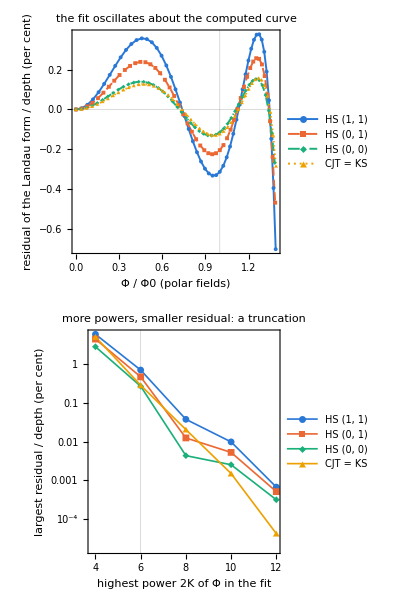

```mathematica
(* the figure: top, the residual of the Landau form along the fitted interval relative to the depth (KS and CJT
   coincide along the polar fields, so one curve is drawn for both); bottom, the largest residual of the fits with
   the powers Phi^2 .. Phi^(2K) against 2K (logarithmic scale); one panel above the other, so that both fit the
   width of a printed page *)
lfColors = {RGBColor["#2a78d6"], RGBColor["#eb6834"], RGBColor["#1baf7a"], RGBColor["#eda100"]};
lfShown = {"HS_1_1", "HS_0_1", "HS_0_0", "CJT"};
lfLegend = {"HS (1, 1)", "HS (0, 1)", "HS (0, 0)", "CJT = KS"};
Column[{
  ListLinePlot[Table[With[{r = lfResults[t]["residuals"]}, Transpose[{r[[All, 1]], 100 r[[All, 3]]}]], {t, lfShown}],
   PlotStyle -> Table[Directive[lfColors[[i]], AbsoluteThickness[1.4], AbsoluteDashing[{{}, {6, 3}, {6, 2, 1, 2}, {1, 2}}[[i]]]], {i, 4}],
   PlotMarkers -> {Automatic, 4}, Frame -> True, FrameLabel -> {"Φ / Φ0 (polar fields)", "residual of the Landau form / depth (per cent)"},
   PlotLegends -> Placed[lfLegend, {Left, Bottom}], GridLines -> {{1.0}, {0}}, ImageSize -> 460,
   PlotLabel -> "the fit oscillates about the computed curve"],
  ListLogPlot[Table[Table[{2 k, 100 lfResults[t]["resK" <> ToString[k]]/Abs[lfE0[t]]}, {k, 2, 6}], {t, lfShown}],
   Joined -> True, PlotStyle -> Table[Directive[lfColors[[i]], AbsoluteThickness[1.2]], {i, 4}], PlotMarkers -> {Automatic, 7},
   Frame -> True, FrameLabel -> {"highest power 2K of Φ in the fit", "largest residual / depth (per cent)"},
   PlotLegends -> Placed[lfLegend, {Left, Bottom}], GridLines -> {{6}, None}, ImageSize -> 460,
   PlotLabel -> "more powers, smaller residual: a truncation"]}, Spacings -> 1.5]
```

## III.L.5 Why no polynomial can be exact: the cause

The pair field enters the quasi-particle energies like a mass. For the applied pair self-energy Φ_a(K_LL^3)^† and a normal self-energy that is a Dirac mass, (M_SF^(X,D)-m_LL)β_LL⊗1_2, the eigenvalues of the matrix of Bogoliubov and de Gennes at the momentum (q⃗)_LL are ±E, each eight times, with

E==((|(q⃗)_LL|)^2+(M_SF^(X,D))^2+Φ_a^2)^(1/2).

The next cell checks this for 20 random momenta, masses and fields with the matrices of Part I (hLL, kLL, betaLL); along the whole polar curve the normal self-energy is such a Dirac mass (the Rust check P3-9 and the Python check YP3-9).

```mathematica
(* the BdG matrix of the eight components with the Dirac mass M (normal self-energy (M - m) beta (x) 1_2) and the applied
   pair self-energy fa (K^3)^dag, at the momentum q; its sorted eigenvalues against -E (eight times) and +E (eight times) *)
lfBdG[q_, mass_, fa_] := Module[{n = (mass - mLL) d8[betaLL], p = fa ConjugateTranspose[kLL[3]], a, d},
   a = hLL[q, mLL] + n; d = hLL[-q, mLL] + n;
   N[ArrayFlatten[{{a, p}, {ConjugateTranspose[p], -Transpose[d]}}]]];
SeedRandom[20261121];
lfQpDev = Max[Table[Module[{q = RandomReal[{-1, 1}, 3], mass = RandomReal[{0.1, 0.5}], fa = RandomReal[{0, 0.6}], ev, e},
     ev = Sort[Re[Eigenvalues[lfBdG[q, mass, fa]]]];
     e = Sqrt[q . q + mass^2 + fa^2];
     Max[Abs[ev - Join[ConstantArray[-e, 8], ConstantArray[e, 8]]]]], {20}]];
check["WP3-8", "the pair field enters the quasi-particle energies like a mass: the BdG matrix with N = (M - m) beta (x) 1_2 and P = Phi_a (K^3)^dag has the eigenvalues -+(q^2 + M^2 + Phi_a^2)^(1/2), eight times each (20 random q, M, Phi_a)", lfQpDev, 10^-13, "P3-8", "YP3-8"];
```

PASS WP3-8  deviation 1.554e-15 (tolerance 1.000e-13): the pair field enters the quasi-particle energies like a mass: the BdG matrix with N = (M - m) beta (x) 1_2 and P = Phi_a (K^3)^dag has the eigenvalues -+(q^2 + M^2 + Phi_a^2)^(1/2), eight times each (20 random q, M, Phi_a)   [the same check: Rust P3-8, Python YP3-8]

A logarithm. The energy per volume is an integral over the momenta q<Λ_LL of functions of (q^2+s)^(1/2) with s==(M_SF^(X,D))^2+Φ_a^2. The next cell integrates the simplest of them exactly and expands the result about s==0: it contains the term 1/16 s^2 ln s, which is not analytic at s==0, that is, at Φ_a^2==-(M_SF^(X,D))^2. Hence 𝒱_SF^X is not a polynomial in (|Φ⃗|)^2, and a series of powers of (|Φ⃗|)^2 about the origin can converge only within a radius of the order of the Dirac mass (m_LL==0.2 at the origin), while Φ_(0,SF)^X==0.31 to 0.40: the superfluid is far from the regime of Landau's theory, where the order parameter is small and the Landau coefficients are Taylor coefficients.

```mathematica
(* the integral of q^2 (q^2 + s)^(1/2) from 0 to the cutoff lam, exactly, and its expansion about s = 0 *)
(* lfq: the modulus of the momentum, lfs: the quantity M^2 + Phi_a^2, lfLam: the cutoff *)
lfInt = Integrate[lfq^2 Sqrt[lfq^2 + lfs], {lfq, 0, lfLam}, Assumptions -> lfs > 0 && lfLam > 0];
lfClosed = lfLam (2 lfLam^2 + lfs) Sqrt[lfLam^2 + lfs]/8 - lfs^2/8 Log[(lfLam + Sqrt[lfLam^2 + lfs])/Sqrt[lfs]];
Print["the integral minus the closed form: ", FullSimplify[lfInt - lfClosed, Assumptions -> lfs > 0 && lfLam > 0]];
lfSeries = Expand[Normal[Series[lfClosed /. lfLam -> 1, {lfs, 0, 2}]]];
Print["the closed form about s = 0 (cutoff 1), to the order s^2: ", lfSeries];
Print["its term with the logarithm: ", Coefficient[lfSeries, Log[lfs]], " Log[s]"];
```

the integral minus the closed form: 0

the closed form about s = 0 (cutoff 1), to the order s^2: 1/4+lfs/4+lfs^2/32-1/8 lfs^2 Log[2]+1/16 lfs^2 Log[lfs]

its term with the logarithm: lfs^2/16 Log[s]

The Taylor coefficient at the origin. The coefficient a_SF^(X,Tay) of (|Φ⃗|)^2 of the Taylor series at the origin is the limit of 𝒱_SF^X/Φ^2 at Φ→0. The Rust and the Python program compute it from three states with small applied fields (0.004, 0.008, 0.016) and the Richardson elimination of the term proportional to Φ^2. The next cell estimates it from the first six points of the computed curve (Φ<0.1, well inside the radius of convergence) by fitting 𝒱_SF^X/Φ^2==a_0+a_1 Φ^2+a_2 Φ^4; the truncation of this local series limits the agreement to about 3×10^-7. The fitted a_SF^X of the Landau form differs from a_SF^(X,Tay) by 0.7 to 2 per cent: it is a property of the fit.

```mathematica
(* lfTaylor[t]: a^Tay estimated from the points 2 to 7 of the curve (the first point is Phi = 0) *)
lfTaylor[t_] := Module[{p = lfCurve[t][[2 ;; 7]]}, LeastSquares[Table[{1, x^2, x^4}, {x, p[[All, 1]]}], p[[All, 2]]/p[[All, 1]]^2][[1]]];
Do[check["WP3-10 " <> t, lfName[t] <> ": the coefficient of Phi^2 of the Taylor series at the origin from the first six points of the curve = the Rust value a^Tay = " <> ToString[rustPart3["p3_a_taylor_" <> t]] <> " (relative)",
   Abs[lfTaylor[t] - rustPart3["p3_a_taylor_" <> t]]/Abs[rustPart3["p3_a_taylor_" <> t]], 10^-6, "P3-10 " <> t, "YP3-10 " <> t], {t, {"HS_1_1", "CJT"}}];
Grid[Prepend[Table[{lfName[t], NumberForm[lfTaylor[t], 10], NumberForm[rustPart3["p3_a_taylor_" <> t], 10], NumberForm[lfResults[t]["a"], 10], NumberForm[100 (lfResults[t]["a"]/rustPart3["p3_a_taylor_" <> t] - 1), 3]}, {t, lfTags}],
   {"method", "a^Tay from the curve", "a^Tay of the Rust program", "a of the Landau form", "a/a^Tay - 1 (per cent)"}], Frame -> All]
```

PASS WP3-10 HS_1_1  deviation 2.646e-7 (tolerance 1.000e-6): HS (1, 1): the coefficient of Phi^2 of the Taylor series at the origin from the first six points of the curve = the Rust value a^Tay = -0.00616243 (relative)   [the same check: Rust P3-10 HS_1_1, Python YP3-10 HS_1_1]

PASS WP3-10 CJT  deviation 2.377e-8 (tolerance 1.000e-6): CJT: the coefficient of Phi^2 of the Taylor series at the origin from the first six points of the curve = the Rust value a^Tay = -0.00429666 (relative)   [the same check: Rust P3-10 CJT, Python YP3-10 CJT]

method | a^Tay from the curve | a^Tay of the Rust program | a of the Landau form | a/a^Tay - 1 (per cent)
HS (1, 1) | -0.006162429464 | -0.006162431094 | -0.006040880441 | -1.97
HS (0, 1) | -0.005353418987 | -0.005353419813 | -0.005281144124 | -1.35
HS (0, 0) | -0.004296658395 | -0.004296658732 | -0.004261967263 | -0.807
KS | -0.004296658653 | -0.004296658755 | -0.00426740334 | -0.681
CJT | -0.004296658653 | -0.004296658755 | -0.00426740334 | -0.681

## III.L.6 Why it matters

It enters no other result. The effective Lagrangians of the solution contain the computed function 𝒱_SF^X, not the Landau form, and no other result uses a_SF^X, b_SF^X, c_SF^X: the mass of the amplitude mode uses the curvature 𝒱''_amp of the computed curve, u_SF^X and the mass of the non-unitary modes use the computed curvature in the non-unitary direction, and the masses of the gauge bosons and the dynamics use Φ_(0,SF)^X, Z_SF^X, Y_SF^X and the susceptibilities.

It matters to whoever replaces $\mathcal V^X_{\rm SF}$ by the Landau form, as in a model of the type of Ginzburg and Landau or of Higgs: the minimum of the polynomial is 0.04 to 0.11 per cent too small, its depth 0.12 to 0.31 per cent too large, its curvature at its minimum 0.86 to 2.3 per cent too large, and the mass of the amplitude mode 0.43 to 1.1 per cent too large (the table above). A derivative enlarges the relative error of the function. Beyond the fitted interval the error grows: fitted on the whole computed curve, the form misses by 1.2 to 1.7 per cent of the depth.

The coefficients are not constants of the theory. a_SF^X differs from the Taylor coefficient at the origin, and b_SF^X, c_SF^X change with the fitted interval and with the number of powers (the last four rows of the table). No physical meaning may be given to b_SF^X or c_SF^X alone. The physical quantities are those that the computed function defines: Φ_(0,SF)^X, the depth, the curvatures at the minimum, and a_SF^(X,Tay).

The qualitative results do not depend on the fit. That 𝒱_SF^X vanishes at the origin, is negative near it, has its minimum at Φ_(0,SF)^X, depends only on the two invariants, and has a stable polar minimum (u_SF^X>0) are properties of the computed function, checked on it directly; the sign of a_SF^X is that of a_SF^(X,Tay) (negative: the normal vacuum is unstable).

The comparison with the Standard Model. The field has a Mexican hat with the symmetry structure of the Higgs sector and of the polar phase of a condensate of spin 1, but its potential is not the quartic potential of the Standard Model: the quartic form misses 𝒱_SF^X by 2.8 to 5.9 per cent of the depth, about ten times more than the Landau form with the sixth power.

Corrections of the first answers. The first answers to the author contained five statements that were not exact; the numbers of this chapter are the corrected ones. (1) The residual changes its sign three times, not five. (2) The fit called a fit on [0,2 Φ_0] used all 61 points of the curve, whose fields reach 1.52 to 1.64 times Φ_(0,SF)^X; the applied field, not the field of the states, reaches 2 Φ_(0,SF)^X. (3) The range of the end of the curve is 1.52 to 1.64 (HS (0,0)), not 1.52 to 1.61. (4) The singularity lies at Φ_a^2==-(M_SF^(X,D))^2 in the applied field; in the field of the states the radius of convergence is of the order of the Dirac mass, not equal to it. (5) The errors of the curvature quoted first, 1.1 to 2.7 per cent, are those of the polynomial at the minimum of the computed curve; at the polynomial's own minimum, where a user evaluates it, they are 0.86 to 2.3 per cent, as the table shows.

## The list of all checks

The last cell lists every check of this notebook with its result and its counterparts in the Rust and the Python programs, and counts the checks that passed.

```mathematica
(* the table of all checks: identifier, result, deviation, tolerance, counterparts *)
Grid[Prepend[Map[{#["id"], If[#["pass"], "PASS", "FAIL"], If[NumericQ[#["deviation"]], sci[#["deviation"]], "--"],
      If[NumericQ[#["tolerance"]], sci[#["tolerance"]], "--"], #["rust"], #["python"]} &, SFNB`Test`$Results],
   Style[#, Bold] & /@ {"check", "result", "deviation", "tolerance", "Rust", "Python"}],
  Frame -> All, Alignment -> Left, BaseStyle -> {FontSize -> 9}]
```

check | result | deviation | tolerance | Rust | Python
WSM-1 | PASS | -- | -- | SM-1 | SM-1
WA-2 | PASS | 0 | 0 | A-2 | A-2
WA-3 | PASS | 0 | 0 | A-3 | A-3
WA-4 | PASS | 0 | 0 | A-4 | A-4
WA-5 | PASS | 0 | 0 | A-5 | A-5
WA-6 | PASS | 0 | 0 | A-6 | A-6
WA-7 | PASS | -- | -- | A-7 | A-7
WA-8 | PASS | 0 | 0 | A-8 | A-8
WA-10b | PASS | 4.885e-15 | 1.000e-10 | A-10b | A-10b
WA-10c | PASS | -- | -- | A-10c | A-10c
WA-10d | PASS | 5.329e-15 | 1.000e-10 | A-10d | A-10d
WA-12 | PASS | 0 | 0 | A-12 | A-12
WF-2 | PASS | 0 | 0 | F-2 | F-2
WF-3a | PASS | 1.777e-14 | 1.000e-10 | F-3a | F-3a
WF-3b | PASS | 8.951e-16 | 1.000e-10 | F-3b | F-3b
WF-3d | PASS | 3.762e-15 | 1.000e-10 | F-3d | F-3d
WF-5a | PASS | 0 | 0 | F-5a | F-5a
WF-5c | PASS | -- | -- | F-5c | F-5c
WC-1 | PASS | 5.551e-16 | 1.000e-9 | C-1 | C-1
WC-3 | PASS | 1.178e-16 | 1.000e-8 | C-3 | C-3
WC-4 | PASS | 5.881e-16 | 1.000e-9 | C-4 | C-4
WC-8 | PASS | 1.256e-15 | 1.000e-9 | C-8 | C-8
WE-2 | PASS | 0 | 0 | E-2 | E-2
WE-3 | PASS | 0 | 0 | E-3 | E-3
WE-4 | PASS | 0 | 0 | E-4 | E-4
WE-14 | PASS | -- | -- | E-14 | E-14
WAS1-3 | PASS | 1.776e-15 | 1.000e-12 | AS1-3 | AS1-3
WAS2-2 | PASS | 4.828e-3 | 1.000e-2 | AS2-2 | AS2-2
WAS2-4 | PASS | 6.450e-5 | 1.000e-3 | AS2-4 | AS2-4
WAS3-1 | PASS | 2.665e-15 | 1.000e-12 | AS3-1 | AS3-1
WAS3-4 | PASS | 3.005e-11 | 1.000e-9 | AS3-4 | AS3-4
WAS4-5a | PASS | -- | -- | AS4-5a | AS4-5a
WAS4-5b | PASS | 1.116e-5 | 1.000e-3 | AS4-5b | AS4-5b
WAS4-3 | PASS | -- | -- | AS4-3 | AS4-3
WP2-0a | PASS | 0 | 1.000e-12 | P2-0e | YP2-0a
WP2-0b | PASS | 0 | 1.000e-12 | P2-0d | YP2-0b
WP2-1 | PASS | 2.988e-12 | 1.000e-8 | P2-1a | YP2-1
WP2-2 | PASS | 2.918e-11 | 3.000e-10 | P2-2a | YP2-2
WP2-6b | PASS | 3.304e-13 | 1.000e-10 | P2-6b | YP2-6b
WP2-6a | PASS | 6.661e-15 | 1.000e-10 | P2-6a | YP2-6a
WP2-6c | PASS | 7.994e-15 | 1.000e-11 | P2-6b, P2-6c | YP2-6c
WP2-6d | PASS | 1.370e-16 | 1.000e-11 | P2-6d | YP2-6d
WP2-6e | PASS | 1.682e-12 | 1.000e-8 | P2-6d | YP2-6e
WP2-6f | PASS | 3.673e-12 | 1.000e-8 | P2-6d | YP2-6f
WP2-6g | PASS | 3.673e-12 | 1.000e-7 | P2-6d | YP2-6g
WP2-7a HS_1_1 | PASS | 1.603e-13 | 1.000e-9 | P2-7a HS_1_1 | YP2-7a HS_1_1
WP2-7b HS_1_1 | PASS | 6.573e-14 | 1.000e-7 | P2-7a HS_1_1 | YP2-7b HS_1_1
WP2-7a KS | PASS | 2.300e-13 | 1.000e-9 | P2-7a KS | YP2-7a KS
WP2-7b KS | PASS | 1.482e-13 | 1.000e-7 | P2-7a KS | YP2-7b KS
WP2-7a CJT | PASS | 2.338e-13 | 1.000e-9 | P2-7a CJT | YP2-7a CJT
WP2-7b CJT | PASS | 1.361e-13 | 1.000e-7 | P2-7a CJT | YP2-7b CJT
WP2-8a HS_1_1 | PASS | 8.289e-14 | 1.000e-8 | P2-8a HS_1_1, P2-8b HS_1_1 | YP2-8a HS_1_1
WP2-8a KS | PASS | 5.794e-14 | 1.000e-8 | P2-8a KS, P2-8b KS | YP2-8a KS
WP2-8a CJT | PASS | 3.145e-14 | 1.000e-8 | P2-8a CJT, P2-8b CJT | YP2-8a CJT
WP2-8b | PASS | 9.437e-16 | 1.000e-12 | P2-3a, P2-3b | YP2-8b
WP2-8c | PASS | 5.919e-12 | 1.000e-9 | P2-8c, P2-8d | YP2-8c
WP2-8d | PASS | 1.492e-8 | 1.000e-7 | P2-8f | YP2-8d
WP3-11 HS_1_1 | PASS | 2.492e-11 | 1.000e-7 | P3-11 HS_1_1 | YP3-11 HS_1_1
WP3-11 HS_0_1 | PASS | 4.409e-11 | 1.000e-7 | P3-11 HS_0_1 | YP3-11 HS_0_1
WP3-11 HS_0_0 | PASS | 4.051e-11 | 1.000e-7 | P3-11 HS_0_0 | YP3-11 HS_0_0
WP3-11 KS | PASS | 3.482e-9 | 1.000e-7 | P3-11 KS | YP3-11 KS
WP3-11 CJT | PASS | 6.816e-9 | 1.000e-7 | P3-11 CJT | YP3-11 CJT
WP3-8 | PASS | 1.554e-15 | 1.000e-13 | P3-8 | YP3-8
WP3-10 HS_1_1 | PASS | 2.646e-7 | 1.000e-6 | P3-10 HS_1_1 | YP3-10 HS_1_1
WP3-10 CJT | PASS | 2.377e-8 | 1.000e-6 | P3-10 CJT | YP3-10 CJT

```mathematica
(* the count of the checks that passed *)
Print["checks of this notebook: ", Length[SFNB`Test`$Results], "; passed: ", Count[SFNB`Test`$Results, r_ /; r["pass"]],
  "; failed: ", Select[SFNB`Test`$Results, ! #["pass"] &][[All, "id"]]]
```

checks of this notebook: 65; passed: 65; failed: {}